# Control Network for Ganymede Images from JunoCam Perijove 34

DOI: 10.5281/zenodo.6377927

Brian Swift, JunoCam Community Science, Twitter: @b_swift

#### Setup

```mathematica
networksTable=TextGrid[{{"Network","Control Points","Control Measures","File Name"},{"Initial",184659,369318,"bs_PJ34-2022-03-17T09:40:43.pvl"},{"Merged Points",83096,233598,"ccp_bs_PJ34-2022-03-17T09:40:43.net"},{"Measures pre Point≥4",16709,75197,"cneMGE4_ccp_bs_PJ34-2022-03-17T09:40:43.net"}}
,Frame->All];
```

```mathematica
additionalFilesTable=TextGrid[{{"File Name","Description"},
{"ISIS Command Notes.txt","ISIS commands to produced reduced control networks and images"},
{"Terminal Saved Output","Log of ISIS commands producing reduced networks and maps"},
{"eqr5.map","ISIS map definition file"},
{"bsblob.patch","Patch that modifies SPICE routine spkpvn.c"},
{"ControlNetworkJunoCamV16j.nb","Mathematica Notebook that produces and evaluates initial control network"},
{"Juno3Dpj34ganyC.nb","Contains support routines used by ControlNetworkJunoCamV16j.nb"},
{"i2s_bs24_PJ34_0{1,2,3,4}.tif","Ganymede map images produced in ISIS"}
}
,Frame->All];
```

```mathematica
primaryRegionsExampleGraphic=-Graphics-;
```

```mathematica
chipExample(* from chipReviewsUnsquareness⟦1⟧ *)={{-Graphics--Graphics-}, {-Graphics--Graphics-}, {-Graphics--Graphics-}, {{{"cPts shifts"}, {"  "{{"idx"}, {1}, {2}, {3}, {4}, {5}, {6}}{{".norm"}, {0.41785542300363016}, {0.2867729348214259}, {0.5263596894808593}, {1.853784283418034}, {0.3864892519782886}, {0.6451645583256523}}{{".dx"}, {-0.35420989990234375}, {-0.01094818115234375}, {-0.43082427978515625}, {0.4599113464355469}, {0.3655052185058594}, {0.3884925842285156}}{{".dy"}, {0.22167205810546875}, {0.2865638732910156}, {0.302398681640625}, {-1.795827865600586}, {-0.12561798095703125}, {-0.5150833129882812}}}}" "{{"Residuals"}, {"  "{{"idx"}, {1}, {2}, {3}, {4}, {5}, {6}}{{".pix"}, {"."}, {1.4200376365390108}, {"."}, {2.418986154914592}, {1.652202288448571}, {1.584410556934996}}{{".km"}, {"."}, {2.3962351879683252}, {"."}, {4.148013300775738}, {2.8250864438161662}, {2.686125073873945}}}}" "{{"Emission Angles"}, {"  "{{"idx"}, {1}, {2}, {3}, {4}, {5}, {6}}{{".primar"}, {"."}, {76.36000725797149}, {"."}, {78.14653697875816}, {77.76982928943458}, {76.96843504451076}}{{".secon"}, {"."}, {39.430823399690425}, {"."}, {40.63255540389811}, {40.5506540033374}, {39.60636330639531}}}}}};
```

## Description

## Control Network

Delivered is a photogrammetric control network for four images of Ganymede collected by the JunoCam instrument [Hansen et al. 2017] during the Juno mission’s [ Bolton et al. 2017 ] perijove 34 encounter on 2021-06-07. The network has 184,659 control points and 369,318 control measures (2 measures per control point). The network is a  PVL formatted text file  for use in ISIS (Integrated Software for Imagers and Spectrometers), [ Laura et al. 2022 ]. When control points are merged with an image distance tolerance of 1.0 pixel (using ISIS tool  cnetcombinept ) the resulting network has 83,096 control points and 233,598 control measures. Extracting control points with 4 or more measures yields a network with 16,709 control points and 75,197 control measures. The motivation for requiring four or more measures is to ensure each control point is linked to at least two datatakes, since three separate framelet images typically exist of any surface feature due to JunoCam being a “pushframe” imager.

```mathematica
networksTable
```

Network | Control Points | Control Measures | File Name
Initial | 184659 | 369318 | bs_PJ34-2022-03-17T09:40:43.pvl
Merged Points | 83096 | 233598 | ccp_bs_PJ34-2022-03-17T09:40:43.net
Measures pre Point≥4 | 16709 | 75197 | cneMGE4_ccp_bs_PJ34-2022-03-17T09:40:43.net

The initial network is produced with novel code (ControlNetworkJunoCamV16j.nb) implemented in Mathematica. This code uses a slightly modified version of the SPICE [ Acton et al., 2017 ] toolkit that enables parametric adjustment to spacecraft positions. Optimization of the spacecraft position adjustments was performed outside this work.

In the “Initial Network” 98% of residuals are less than 1.72 pixels. Median residual is .40 pixels. There are 54 control points with residuals greater than 3 pixels, and 1544 with greater than 2. ControlNetworkJunoCamV16j.nb contains additional graphs of residual distribution.

## Corresponding Points Generation Concept of Operations

Conceptually, the process of producing the corresponding points is as follows:

Each image framelet is divided into a set of roughly square overlapping primary regions.

```mathematica
primaryRegionsExampleGraphic (* Less than 1/2 of total width is displayed below *)
```

-Graphics-

Points on the perimeter of each primary region (yellow) are projected out of the camera.

If all the points on the perimeter of a primary region project onto the surface of Ganymede, these surface points are retained.

The surface points are projected back into all the framelets.

If all the surface points projected from a primary region onto the surface are visible within a framelet, they from a secondary region.

A primary image chip is produced by copying out and scaling up by 2.5x the portion of the image framelet corresponding to the primary region.

A perspective transform is determined to align the secondary region perimeter points to the primary region perimeter points.

A secondary image chip is produced by applying the perspective transform to the framelet image containing the secondary region.

Mathematica ImageCorrespondingPoints using computer vision “SURF” method identifies corresponding points between the primary and secondary chip images that have a KeypointStrength > 0.0005 (keypointStrengthThreshold)

If fewer than 5 corresponding points (correspondingPointCountThreshold) are found between the primary and secondary chips, they are discarded. This reduces the likelihood of incorrect matching.

Corresponding points identified in chips are regrouped by framelet.

Points closer than 3.5 pixels (correspondingPointDistanceThreshold) in a framelet are discarded.

Below is an illustration of two framelets with primary and secondary regions outlined (in cyan), extracted chips, and corresponding points. (Note: when viewed in Mathematica, the center image is a click-to-flip view that alternates between the primary and perspective-transformed secondary chips.)

```mathematica
chipExample
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2
3
4
5
6.norm
0.417855
0.286773
0.52636
1.85378
0.386489
0.645165.dx
-0.35421
-0.0109482
-0.430824
0.459911
0.365505
0.388493.dy
0.221672
0.286564
0.302399
-1.79583
-0.125618
-0.515083 Residuals
    idx
1
2
3
4
5
6.pix
.
1.42004
.
2.41899
1.6522
1.58441.km
.
2.39624
.
4.14801
2.82509
2.68613 Emission Angles
    idx
1
2
3
4
5
6.primar
.
76.36
.
78.1465
77.7698
76.9684.secon
.
39.4308
.
40.6326
40.5507
39.6064

## Additional Files

```mathematica
additionalFilesTable
```

File Name | Description
ISIS Command Notes.txt | ISIS commands to produced reduced control networks and images
Terminal Saved Output | Log of ISIS commands producing reduced networks and maps
eqr5.map | ISIS map definition file
bsblob.patch | Patch that modifies SPICE routine spkpvn.c
ControlNetworkJunoCamV16j.nb | Mathematica Notebook that produces and evaluates initial control network
Juno3Dpj34ganyC.nb | Contains support routines used by ControlNetworkJunoCamV16j.nb
i2s_bs24_PJ34_0{1,2,3,4}.tif | Ganymede map images produced in ISIS

## Code

## Documentation and Configuration

### What it does

Produce ISIS text control network for JunoCam PJ34 Ganymede Images

### Setup

Setup SPICE per instructions in Juno3Dpj34ganyC.nb

Perform SPICE modification (allows low-level adjustments to spacecraft position)

: Setup for mod in new N0067 spice
cd /Users/bswift/Downloads/cspice/src
mkdir bsspice
cd bsspice 
cp ../cspice/spkpvn.c .

: Apply patch to copy of spkpvn.c
patch -N <bsblob.patch

: link in alll cspice .h files and build script
ln ../cspice/*.h .
ln ../cspice/mkprodct.csh .

: create library bsspice.a in /Users/bswift/Downloads/cspice/lib
: This library only contains modified spkpvn object.
: When SPICE interface is built in Mathematica, this library preceedes the standard SPICE library (cspice.a) in the list of static libraries. This allows the customized version of spkpvn_ to override the untouched distribution version in cspice.a

./mkprodct.csh

Download SPICE data appropriate for PJ34 from NAIF

Download PJ34 Ganymede raw data from PDS

Set controlNetworkOutputDirectory (below line) to directory where final control network should be written

```mathematica
controlNetworkOutputDirectory="/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io" (* Directory where ISIS control network is written *)
```

/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io

```mathematica
DirectoryQ[controlNetworkOutputDirectory]
```

True

### Execution Recipe

Evaluate “Setup, Prompt, Load Metadata” in Juno3Dpj34ganyC.nb
When file chooser opens select the 4 PDS raw image files (JNCE_2021158_34C00001_V01.IMG, JNCE_2021158_34C00002_V01.IMG, JNCE_2021158_34C00003_V01.IMG, JNCE_2021158_34C00004_V01.IMG)
Evaluate “Setup” under “Process and Export Files” in Juno3Dpj34gany.nb
Evaluate this notebook
Head to lunch...

### Change History

ControlNetworkJunoCamV4.nb	updated chip layout and only using strongest points in preliminary optimization
ControlNetworkJunoCamV4.nb	don’t use limb fit when optimizing
ControlNetworkJunoCamV5.nb	increase chip selection limit from 6 to 9
ControlNetworkJunoCamV6.nb	limit emission angle of control points used for optimization to <45 Deg
ControlNetworkJunoCamV7.nb	stricter implementation of emission angle limit and self exclusion, also fix limb fit ignoring worst datatake, best of 2 optimizations for 2nd phase
ControlNetworkJunoCamV8.nb	increase debias sampling grid density to provide more points to optimization
ControlNetworkJunoCamV12.nb	Add KeypointStrength limit
ControlNetworkJunoCamV13.nb	Just PJ34_2,3,4
ControlNetworkJunoCamV14.nb	Add limit to exclude measures near 150 edge of CCD (this area was generating outliers)
ControlNetworkJunoCamV15.nb	Add limit to exclude measures near 250 edge of CCD, only PJ341..3 because won’t have much left of PJ34
ControlNetworkJunoCamV16b.nb	Remove optimization code and only produce final network using previously derived tunedPositionShifts
ControlNetworkJunoCamV16h.nb	fixed chipFirstEdge
ControlNetworkJunoCamV16i.nb	minor changes to offset solution from ControlNetworkJunoCamV15c.nb
ControlNetworkJunoCamV16j.nb	add correspondingPointDistanceFilter, lower correspondingPointCountThreshold to 5, work on graph presentation

## Definitions and Functions

```mathematica
$Version
```

12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019)

### Configuration Parameters

```mathematica
keypointStrengthThreshold=2.5 .0002 (* sets ImageCorrespondingPoints[] KeypointStrength parameter *)
```

0.0005

```mathematica
keypointStrengthThreshold=.01 2.5 .0002 (* super low value used initially for PJ41 Io *)
```

5.×10^-6

```mathematica
keypointStrengthThreshold=0.0001(* 0.00005 79 control points with 8 outliers > 1px
0.0001 gives 65 control points with 6 outliers > 1px
0.0002 gives 47 control points with 4 outliers > 1px
0.00043 reduced matches to 21 control points in MM12.  MM13.1 0.00004 Determined in "PJ41 Io keypointStrengthThreshold Investigation.nb"  *)
```

0.0001

```mathematica
1.{4/47,6/65,8/79}
```

{0.0851064,0.0923077,0.101266}

```mathematica
outlierRejectionCount=6
```

6

```mathematica
correspondingPointCountThreshold=1 (* 1 PJ41 Io *) (*5 PJ34 Ganymede *) (* Require at least this many corresponding points in a chip. Used in "Select Chip Pairs". Larger values reduce likelyhood of bogus corresponding points. Reduced from 6 to 5 after ImageCorrespondingPoints[] TransformationClass parameter changed from "Perspective" to "Rigid"   *)
```

1

```mathematica
maxCorrespondingPointsPerChip=15(* sets ImageCorrespondingPoints[] MaxFeatures parameter *)
```

15

```mathematica
Assert[correspondingPointCountThreshold≤ maxCorrespondingPointsPerChip]
```

```mathematica
correspondingPointDistanceThreshold=2.(*3.5 (* Ganymede*)*)(* corresponding points closer to neighbor than this many pixels are removed *)
```

2.

```mathematica
(*samplingSpherePointCount=3 3 3 400*)(* only used durring optimzation *)
```

```mathematica
(*emissionAngleLimitForThinning=55. Degree;*)(* only used durring optimzation *)
```

### Load Datatake Info

```mathematica
loadDatatake=Function[{fileName,index},
Block[{jx},
jx=junocamToQuads[fileName];
allChipInfo=Cases[jx⟦"g3d"⟧,HoldPattern["chipInfo"->_],Infinity]⟦All,2⟧; (* Pull out all the chipInfo Associations *)
(* XXX should not be relying on junocamToQuads setting globals to pick up below parameters *)
datatakeKey=imageId;
datatakeKey-><|
"selfId"->datatakeKey (* Added, looks like not being used nor propogated through matching/debias *)
,"datatakeIndex"->First@index
,"fileName"->fileName
,"imageId"->imageId
,"platform"->"JUNO" (* Spice body name *)
,"platformNAIFIntegerCode"->bodn2c["JUNO"]⟦"code"⟧  (* XXX should have check of "found" flag *)
,"instrument"->"JunoCam"
,"target"->target
,"starTimeShift"->starTimeShift (* Used durring setup. Overridden durring optimization. *)
,"adjustedStartTime"->adjustedStartTime
,"adjustedInterframeDelay"->adjustedInterframeDelay
,"blobSPKAdjustment"->blobSPKAdjustment
,"segs"->segs
,"cbSegs"->cbSegs
,"cbtnSegs"->(cbtnSegs=colorBalanceTDINormalizeSegs[imageObj])
,"cbtnUncorrectedSegs"->(cbtnUncorrectedSegs=colorBalanceTDINormalizeUncorrectedSegs[imageObj])
(*,"segsLimbFiltered"->MapIndexed[GradientFilter[#,2]&,cbtnUncorrectedSegs,{3}]*)
,"segsLimbFiltered"->MapIndexed[limbFilt4,cbtnUncorrectedSegs,{3}] 
(*MapIndexed[limbFilt3,segs,{3}] *)(*YYY configurable *)(*XXX enable for limb fitting optimization in ganymedeOptDevF. Commented out because slow and uses memory. *)

,"allChipInfo"->allChipInfo
,"allCoordsOnTarget"->(allCoordsOnTarget=Flatten[allChipInfo⟦All,"coordsOnTarget"⟧,1])
,"sunDir"->Block[{targetFrame=targetFrame,target=target},sunDirectionAtTime[adjustedStartTime]]

,"backstopSphereMin"->backstopSphereMin
,"backstopSurface1"->ReplacePart[backstopSphereMin,2->backstopSphereMin[[2]]+100000.]
,"backstopSurface2"->ReplacePart[backstopSphereMin,2->backstopSphereMin[[2]]+300000.]


(* debugging only *)
,"rawByteSaturationCountByChannel"->imageObj["rawByteSaturationCountByChannel"]
,"rawLevelsByChannel"->imageObj["rawLevelsByChannel"]
,"unCorrectedSegments"->imageObj["unCorrectedSegments"] 
,"metaData"->imageObj["metaData"]
|>
]
];
```

### junocamToQuads to create primary chip polygons

#### Dev (Developed in ChipTangulateDev.nb)

```mathematica
(* Create rectangular polygon with with multiple points along each edge *)
edgesToPoly=Function[{xMin,xMax,yMin,yMax,xDivisions,yDivision},
Polygon[
DeleteDuplicates[
Flatten[
{Subdivide[{xMin,yMin},{xMax,yMin},xDivisions] (* bottom edge *)
,Subdivide[{xMax,yMin},{xMax,yMax},yDivision] (* right edge *)
,Subdivide[{xMax,yMax},{xMin,yMax},xDivisions](* top edge *)
,Subdivide[{xMin,yMax},{xMin,yMin},yDivision](* left edge *)
}
,1]
]
]
];
```

```mathematica
(*chipFirstEdge=Function[{minMax,count},Round[minMax⟦1⟧,1/2]+Floor[(minMax⟦2⟧-minMax⟦1⟧)/count(Range[count]-1)]]; *)(* hasn't been throughly tested *)
```

```mathematica
(* Subdivide minMax range into count size-ed pieces. Returns value of leading edge of each divison. XXX Should return leading and trailing edge. *)
chipFirstEdge=Function[{minMax,size,count},
Assert[(minMax[[2]]-minMax[[1]])>size&&size>0&&count>=1&&minMax[[2]]>minMax[[1]]];
If[count>1
,Subdivide[minMax⟦1⟧+size/2,minMax⟦2⟧-size/2,count-1]-size/2
,{Mean[minMax]-size/2}]
];
```

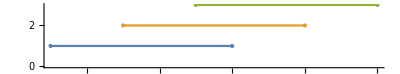

```mathematica
NumberLinePlot[Interval/@(({#,#+5}&@chipFirstEdge[{1,10},5,3])ᵀ)]
```

```mathematica
(* Convert list of Polygons with explicit points to GraphicsComplex*)
polysToGraphicsComplex=Function[polyList,
Block[{points
,pointsAssoc
,indexedPolys
},
points=DeleteDuplicates[Cases[chipPolys,{_?NumberQ,_?NumberQ},Infinity]];
pointsAssoc=<|MapIndexed[{#1->First[#2]}&,points]|>; (* points to index mapping *)
indexedPolys=ReplaceAll[polyList,pt:{_?NumberQ,_?NumberQ}:>pointsAssoc[pt]]; (* Replace explicit points with index to point's location in points list *)
GraphicsComplex[points,indexedPolys]
]
];
```

```mathematica
(* Produce GraphicsComplex of rectangular polygons with integer length sides that cover the given filterRegion. Chips may have small overlaps needed span region with chips with integer length edges. An additional set of Polygons reduced by one row and one colum, shifted by half the edge size of the first chip. These chipShiftedPolys have centers that cover the interior corners of primary grid.

A GraphicsComplex is returned because the Mathematica geometric region operations end up colapsing the overlapping rectangles, which didn't occur with earlier clasical tiling.
 *)
(* with chipsPerNarrowAxis=3 -> chipLongCount=32 
with chipsPerNarrowAxis=2 -> chipLongCount=21
with chipsPerNarrowAxis=4 -> chipLongCount=42
*)
chipTangulateGC=Function[{filterRegion,chipsPerNarrowAxis,xDiv,yDiv},
Block[{
regionWidthHeight
,narrowAxisIndex,longAxisIndex
,chipNarrowSize
(*,chipLongCount*)
,chipLongSize
,chipFirstEdgeLong
,chipSecondEdgeLong
,chipFirstEdgeNarrow
,chipSecondEdgeNarrow

,xRanges,yRanges

,chipPrimaryPolys
,chipShiftedPolys
,chipPolys
,gc
,overlap=1/6 (* Based on testing with chipsPerNarrowAxis=3 to reduce grid of reduced control points near chip edges *)
},
regionWidthHeight=Round[Flatten[Differences/@RegionBounds[filterRegion]],1/256] ;(* Rounding so end up with rational for chipLongStride at end. Expect to be whole number, but rounding to 1/256 to make unexpected detectable *)
{narrowAxisIndex,longAxisIndex}=Ordering[regionWidthHeight];
chipNarrowSize=Ceiling[(1+overlap)regionWidthHeight⟦narrowAxisIndex⟧/chipsPerNarrowAxis];
chipLongCount=Floor[regionWidthHeight⟦longAxisIndex⟧/chipNarrowSize];
chipLongSize=Ceiling[(1+overlap)regionWidthHeight⟦longAxisIndex⟧/chipLongCount];

(* First/leading and Second/trailing edges of chips. Will be left and right or bottom and top depending on which axis is the long axis. *)
chipFirstEdgeLong=chipFirstEdge[RegionBounds[filterRegion]⟦longAxisIndex⟧,chipLongSize,chipLongCount];
chipSecondEdgeLong=chipFirstEdgeLong+chipLongSize;
chipFirstEdgeNarrow=chipFirstEdge[RegionBounds[filterRegion]⟦narrowAxisIndex⟧,chipNarrowSize,chipsPerNarrowAxis];
chipSecondEdgeNarrow=chipFirstEdgeNarrow+chipNarrowSize;

(* Polygons formaing primary grid with small overlap needed span region with chips with integer length edges. *)
{xRanges,yRanges}={{chipFirstEdgeNarrow,chipSecondEdgeNarrow}ᵀ,{chipFirstEdgeLong,chipSecondEdgeLong}ᵀ}⟦{narrowAxisIndex,longAxisIndex}⟧; (* Assign Narrow/Long to x/y or y/x as appropriate *)

chipPrimaryPolys=Flatten[Table[edgesToPoly[xRange⟦1⟧,xRange⟦2⟧,yRange⟦1⟧,yRange⟦2⟧,xDiv,yDiv],{xRange,xRanges},{yRange,yRanges}]
];

(*(* chipPrimaryPolys reduced by one row and one colum, shifted by half the edge size of the first chip. Polys shifted so centers are at interior corners of primary grid.*)
{xRanges,yRanges}={(Round[(chipSecondEdgeNarrow-chipFirstEdgeNarrow)(1/2-overlap/2)]+{chipFirstEdgeNarrow,chipSecondEdgeNarrow}ᵀ)⟦1;;-2⟧,(Round[(chipSecondEdgeLong-chipFirstEdgeLong)(1/2-overlap/2)]+{chipFirstEdgeLong,chipSecondEdgeLong}ᵀ)⟦1;;-2⟧}⟦{narrowAxisIndex,longAxisIndex}⟧;

chipShiftedPolys=Flatten[Table[edgesToPoly[xRange⟦1⟧,xRange⟦2⟧,yRange⟦1⟧,yRange⟦2⟧,xDiv,yDiv],{xRange,xRanges},{yRange,yRanges}]
];
chipPolys=Join[chipPrimaryPolys,{},chipShiftedPolys];
*)
chipPolys=chipPrimaryPolys;
gc=polysToGraphicsComplex[chipPolys];
gc
]
];
```

```mathematica
(* Visualize chips and and edge points *)
(*tgc=chipTangulateGC[filterRegion,3,3,3];Graphics[{EdgeForm[Green],FaceForm[Opacity[0.6]],tgc,Yellow,Point[First[tgc]]},Frame->True,ImageSize->Full]*)
```

```mathematica
(*Produce Regions Example Graphic*)
(* Need to define filterRegion with preliminary run first *)
(*tgc=chipTangulateGC[filterRegion,7,3,3];
Graphics[
Rotate[
{EdgeForm[Black],FaceForm[Opacity[0.6]],tgc,Yellow,Point[First[tgc]]}
,90 Degree]
(*,Frame->True*)
,ImageSize->Scaled[2.5]
]*)
```

```mathematica
(*observationAngleLimitDeg=89. *)(* Maximum angle between observing ray and surface. 90 would be along limb, values >90 would be around beyond limb. *)
```

```mathematica
(* Much of below not needed for chip matching, just leftover from cut/past of junocamTo3D[] *)
(* process junocam file into an associoation containing Mathematica Graphics3D object (that contains extended information in rules that are used in export but ignored by Mathematica) *)
Clear[junocamToQuads];
junocamToQuads[fileName_]:= Block[
{
(*imageObj
,segs
,imageMetadata
,*)(*cbScale
,target

,startTimeClockStr
,starTimeShift  (* should be named startTimeShift *)
,maybeStarTime

,frameTimeForAVEstimate
,avRates
,spiceYawRate

,startTime2
,adjustedStartTime
,interframeDelay
,adjustedInterframeDelay

,cameraFrameNumber

,limbBasedBackstopSpheres
,backstopSphereMin
,meshTriRefinementThreshold
,refineLimbPixelAreaLimit
,refineMaxPixelAreaPerTri
,meshRefinement7

,refineMaxTargetAreaPerTri4Squared

,datatakeId
,imageId

,frameNumberSpan
,frameNumbers
,frameSpanLength

,bsRegionIntersectionFallbacks

,g12d

,filterRegion
,filterRange
,frameNumber

,gcFrameTime
,scPosition
,scToTargetMat
,backstopSurface
,filterMesh
,textureCoordinates

,boresightIntercept
,boresighResolution
,ccdTopCenterIntercept
,spinAVVec
,scXYZAv

,surfaceIntercept
*)
},

(* setup *)

imageObj=loadChannelsFn[fileName];
(*shiftGuessSetup[fileName];*) (* Just to set interframeDelay? *)

segs=rgbPadded[imageObj];

imageMetadata=metaDataByRawFilename⟦fileName⟧;



If[targetOverride==""
,target=imageMetadata⟦"TARGET_NAME"⟧
,target=targetOverride
];
(* set targetFrame based on target *)
If[target≠"J2000"
,targetFrame="IAU_"<>target
,targetFrame="J2000"
];

datatakeId="P"<>imageObj⟦"fnOrbit"⟧<>"_"<>zeroPadLeft[StringDelete[imageObj⟦"fnIndex"⟧,StartOfString~~"0"..] ,2];
(* P{perijove}_{image number} short source image identifiation *)
imageId=datatakeId<>colorTag <> variantTag ;(* P{perijove}_{image number}{colorTag}{variantTag} short outputs identifiation *)


(*gcbScale=cbScale=metadataValueToNumber[imageMetadata⟦"JNO:TDI_STAGES_COUNT"⟧] findBrightnessScale[segs];*)(* old, used when findBrightnessScale[segs] was constant 1.2 *)
gcbScale=cbScale= findBrightnessScale[segs,imageMetadata];

cbSegs=1./(cbScale colorBalance)segs;

cbStats=cbScaledStats[imageObj,cbScale (*findBrightnessScale[{},imageMetadata]*)];

fullWellRendered=lut⟦(*240*)fullWellRawValue(*220*)⟧{1,1,1} /(colorBalance cbScale); (* raw full well / saturated value 224 converted cbScaled (rendered) values *)

Print[datatakeId,": cbScale = ",cbScale
, " cbScaledSaturatedByChannel = ",cbStats⟦"cbScaledSaturatedByChannel"⟧ (* Absolute saturation (255) count after color balance. Expected saturation counts after rendering. *)
," rawByteSaturationCountByChannel (#>",fullWellRawValue,") = ",imageObj⟦"rawByteSaturationCountByChannel"⟧
," TDI = ",metadataValueToNumber[imageMetadata⟦"JNO:TDI_STAGES_COUNT"⟧]," target = ",target
]; (* Saturation counts in raw data. Raw data values > 224 where saturation might start *)

startTimeClockStr=imageMetadata⟦"SPACECRAFT_CLOCK_START_COUNT"⟧;
startTime2=scs2e[junoNacid,startTimeClockStr];

(*zzImageTime=imageMetadata⟦"IMAGE_TIME"⟧; (* Ganymede flyby planning *)
startTime2=str2et[zzImageTime];
*)

adjustedStartTime=startTime2+selectedCameraParams⟦"startTimeBias"⟧;
interframeDelay=metadataValueToNumber[imageMetadata⟦"INTERFRAME_DELAY"⟧];
adjustedInterframeDelay=interframeDelay+selectedCameraParams⟦"ifdAdjustment"⟧;

(*starTimeShift=perImageTuning⟦datatakeId,"startTime"⟧/.Missing["KeyAbsent",_]-> 0.; XX old *)(* use manual tuning value if available *)

starTimeShift=0.;  (* frameTimeForFrameNumber needs a value for starTimeShift *)

frameTimeForAVEstimate=frameTimeForFrameNumber[1];
Assert[!MemberQ[(avRates=xf2rav[sxform["JUNO_SPACECRAFT","J2000",frameTimeForAVEstimate]]⟦2⟧), "LIBRARY_FUNCTION_ERROR",Infinity]]; (* Can't Justify using J2000 vs targetFrame for avRates *)
spiceYawRate = Norm[avRates]/Degree; (* needed by calcQuickStartTimeShift *)

(*starTimeShift=If[starTimeShift≠ 0.|| target == "J2000"
,starTimeShift
,calcQuickStartTimeShift[segs]];
XX old *)

blobSPKAdjustment=Join[{1. junoNacid (*-61.*)},0.Range[6]];(* position adjustments controls. Default to 0s unless values for datatake found in lookup below *)
If[!MissingQ[tunedParams=tunedPositionShifts[datatakeId]],
starTimeShift=tunedParams["dt"];
blobSPKAdjustment=Join[{1. junoNacid (*-61.*)},{"dx","dy","dz",0.,0.,0.}/.tunedParams];
Print[datatakeId,": using tunedParams ",tunedParams]
,
(* Else, no tunedParams for datatake *)
(* If perImageTuning starTimeShift present use it
if not preset and target J2000 use 0
if not present and not J2000 calc
*)
starTimeShift=If[!MatchQ[maybeStarTime=perImageTuning⟦datatakeId,"startTime"⟧,  Missing["KeyAbsent",_]]
,Print[imageId," using perImageTuning startTime adjustment ",maybeStarTime];maybeStarTime  (* have perImage starTime so use it *)
,If[target == "J2000"
,Print[imageId," using J2000 starTimeShift=0."];0. (* use 0 for J2000 because there won't be any limb star field images to base start time on *)
, calcQuickStartTimeShift[segs]
]
]
];
lastBlob=blobrw[blobSPKAdjustment];

(*starTimeShift=0.;*) (* XXX testing position optmization *)

frameNumberSpan=frameRangeToProcess;
frameNumbers=Range[Length@First@segs]⟦frameNumberSpan⟧;
frameSpanLength=Length[frameNumbers];
totalFrames+=frameSpanLength;

cameraFrameNumber=First@MinimalBy[frameNumbers,boresightTargetAngle];(*frame with smallest separation between boresight and target center. *)

blenderCameraIndex=cameraFrameNumber; (* XX hack, select camera used for rasterization *)
blenderCameraIndex=First@First@Position[frameNumbers,cameraFrameNumber]; (* XX testing fix *)
(* sets scPosition/(synthetic camera position) for backstopSphere *)
If[target≠"J2000"
,backstopSphereMin=First@findBackstopMinSphereAtFrame[cameraFrameNumber,Length@segs⟦1⟧ ,target,"radiusAdjustmentFunction"->(backstopRadiusFactor#&)] (* Sphere will be through planet center if no limb points in frames. *)
,backstopSphereMin=Sphere[{0,0,0},50000.] (* arbitrary backstop size for J2000 star images. *)
];

(*backstopSphereMin=Sphere[{-73386.56817377128,22993.31138283214,2137.857871404656},600000.]; (* xx PJ23_28 io testing *)*) (* motion relative to small radius backstop sphere can produce alignment errors for moon imagery. *)

meshTriRefinementThreshold=Area[(*First@*)backstopSphereMin]/60000;

(*refineMaxTargetAreaPerTri=meshTriRefinementThreshold /geometryDetail ;*)(* Maximum target (projected) area (km^2) of a mesh triangle *)
refineMaxTargetAreaPerTri4Squared=4(meshTriRefinementThreshold /geometryDetail )^2;
(* 4 times the Square of the area on planet in km^2 *)

refineLimbPixelAreaLimit=4./geometryDetail ;(* Triangles that cross limb but have pixel area smaller than this will not be further reduced. *)

refineMaxPixelAreaPerTri=517./geometryDetail ;(* Maximum pixel area of a mesh triangle. 517 is just above max area for a filter triangulated without mesh refinement. *)

meshRefinement7=makeMeshRefinement7 ;(* need to recompile whenever controling parameters are updated, due to using CompilationOptions  *)



bsRegionIntersectionFallbacks={};

(* produce texture mapped 3D object representation of JunoCam image *)
(*markedSegs=markSegsFilter[segs];  ZZZ*)

g12d= 
Graphics3D[
{
(*"groupID"-> imageId
,*)
Table[{ (* by colorIndex *)
"objectName"-> imageId<>{"r","g","b"}⟦colorIndex⟧
,"groupID"-> StringRiffle[{
imageId<>{"r","g","b"}⟦colorIndex⟧
,imageId
, target
}
]
,"textureID"-> imageId<>{"r","g","b"}⟦colorIndex⟧
(*,(*Texture[
pngExportFilter@
ImageAdjust[
ImageAssemble[Map[texFilter,markedSegs(*segs*)⟦colorIndex,frameNumberSpan⟧,{-1}]]
,{0,0,1},{0,cbScale colorBalance⟦colorIndex⟧}
]
]*)
Texture[
addBiasFor16BitImage[ (* add textureColorBias to active pixels, 0s edge pixels *)
toColorImg[ (* moves single gray scale channel into appropriate channel of a color image *)
pngExportFilter@ (* linear to sRGB conversion *)
ImageAdjust[
ImageAssemble[Map[texFilter,markedSegs(*segs*)⟦colorIndex,frameNumberSpan⟧,{-1}]]
,{0,0,1},{0,cbScale colorBalance⟦colorIndex⟧}
]
,colorIndex]
]
] ZZZ *)
,

filterRegion=ConvexHullMesh[Flatten[filterActivePixelCenterCorners⟦colorIndex⟧,1]]; (* Region of CCD for which image geometry is produced. Pulled in from edges of active area by 1/2 pixel. In CCD fullframe pixel coordinates. *)
 
filterRange=MinMax/@Transpose[Flatten[filterCorners⟦colorIndex⟧,1]];
 (* texture coords *)
Map[(* by frameNumber *)
{
frameNumber=#;
Antialiasing->False
(* per frame groupID causes many entries in SceneKit materials list, even though no additional usemtl commands generated. *)
(*,"groupID"-> StringJoin[
imageId
," "
,imageId<>{"r","g","b"}⟦colorIndex⟧
," "
,imageId<>{"r","g","b"}⟦colorIndex⟧<>ToString[frameNumber]
]*)
,EdgeForm[{Green}(*ZZZ*)]
,
gcFrameTime=frameTimeForFrameNumber[frameNumber];
If[target≠"J2000",
scPosition=(spkezra["JUNO_SPACECRAFT",gcFrameTime,"IAU_"<>target,"NONE"(*"CN+S"*),target])⟦1;;3⟧;
,scPosition={0,0,0}
];
scToTargetMat=sxform["JUNO_SPACECRAFT",targetFrame,gcFrameTime];
(*(* Tight backstop surface on limb.
Untested in production environment. *)
backstopSCAdj=0;
backstopSurface=Flatten@Join[{
backstopSphereMax
,
findBackstopSphere3[gcFrameTime,target]
},findLimbHyperplanes2[gcFrameTime,target]];*)
backstopSurface={backstopSphereMin};

sunDir=sunDirectionAtTime[gcFrameTime];
sunDirNormalized=Normalize[sunDir];
cosθ2=Cos[ 85.  Degree]^2; (* Sun illumination angle threshold *)

(* memoization for significant (16x in dev) performance improvement *)
(*ClearAll[pix2TargetMem2];
mem:pix2TargetMem2[{xPix_,yPix_}]:=mem=pix2Target3[{xPix,yPix},gcFrameTime,target,scPosition,scToTargetMat,backstopSurface];
*)

chipPolygonsGC=chipTangulateGC[filterRegion,14,3,3];(* 3,3,3 PJ34 Ganymede *)
(* 13,3,3 -> <|1->26,2->3|> 8,3,3 and 4,3,3 PJ41 Io didn't work *)
(* earlier work used chipTangulateGC[filterRegion,3,3,3] *)
(* XXX Note: if 3,3 subdivisions changed, also need to change setting groupsWith4Points of in chipMatching[] function *)

frameRayIntercepts=Map[
pix2frameRayIntercept[#,gcFrameTime,target,scPosition,scToTargetMat]&,chipPolygonsGC⟦1⟧
];
keptCoordsMask=Map[#⟦2,"found"⟧
&&(observedAngleForTargetPoint[#]<observationAngleLimitDeg Degree)
&&(vectorAngleLessThanF[sunDirNormalized,#⟦2,"spoint"⟧,cosθ2])&,frameRayIntercepts];

targetPoints=frameRayIntercepts⟦All,2,"spoint"⟧; (* earlier targetPoints were 4 components from pix2TargetMem2, where 4th compoent was the intercepted surface ID. So various code that uses it, includeds ⟦1;;3⟧ to discard the surfaec ID, which is no longer there. *)


(*targetPoints=Map[
pix2TargetMem2[#](*⟦{1,2,3}⟧*)&,chipPolygonsGC⟦1⟧
];(* pix2TargetMem2 retunrs 4-tuples of {x,y,z,surface id}.
SurfaceID==1 indicates ray from pixel location intersected target *)
keptCoordsMask=Map[(#⟦4⟧==1)(*&&(observedAngleForTargetPoint[#]<82. Degree)*)&,targetPoints]; 

*)
polys=chipPolygonsGC⟦2⟧;
keptPolys=Select[polys,AllTrue[Extract[keptCoordsMask,List/@#⟦1⟧],#&]&];

gc3dculled=GraphicsComplex[
(*radiusRescale*) targetPoints⟦All,{1,2,3}⟧ (* 3d points on target/planet *)
,keptPolys
];

coordsOnTarget=Pick[targetPoints⟦All,{1,2,3}⟧,keptCoordsMask];




(*textureCoordinates=Map[pix2uv[#,filterRange]&,MeshCoordinates[filterMesh]];*)

(* Potentially useful spacecraft and imaging information that is passed through to the export routnes to be included in comments, but otherwise unnecessary. *)
(*boresightIntercept=pix2TargetMem2[ccdSize/2]⟦{1,2,3}⟧;*)
(*boresighResolution=distanceOnTarget[ccdSize/2,ccdSize/2+{1,1}1/Sqrt[2.]]; *)(* km/pixel resolution on target at boresight *)
(*ccdTopCenterIntercept=pix2TargetMem2[ccdSize{1/2,1}]⟦{1,2,3}⟧;*)
(* NOTE: boresightIntercept,boresighResolution,ccdTopCenterIntercept may be bogus when vectors are not intetsecting target. Values in this case will be from intersection with backstop sphere*)
spinAVVec=xf2rav[sxform["JUNO_SPACECRAFT",targetFrame,gcFrameTime]]⟦2⟧; (* xf2rav AV is in "JUNO_SPACECRAFT" frame. Values radian/sec. *)
surfaceIntercept=sincpt["Ellipsoid",target,gcFrameTime,targetFrame,"CN+S","JUNO",targetFrame,-scPosition]; (* approximate subobserver/nadir point. XX light time correction here probably wrong due to DREF is same as FIXREF, see sincpt caution at end. *)
"info"->Join[ <|
"imageId"-> imageId
,"fnBaseName"->imageObj⟦"fnBaseName"⟧
,"frameNumber"-> frameNumber
,"colorIndex"-> colorIndex
,"cbScale"-> cbScale (* brightness scale *)
,"colorBalance"-> colorBalance
,"textureColorBias"-> textureColorBias
,"fullWellRendered"-> fullWellRendered
,"TDI_STAGES_COUNT"-> imageMetadata⟦"JNO:TDI_STAGES_COUNT"⟧
,"EXPOSURE_DURATION"-> imageMetadata⟦"EXPOSURE_DURATION"⟧
,"SOLAR_DISTANCE"-> imageMetadata⟦"SOLAR_DISTANCE"⟧
,"INTERFRAME_DELAY"-> imageMetadata⟦"INTERFRAME_DELAY"⟧
,"frameTimeUTC"->et2utc[gcFrameTime,"ISOC",4]
,"gcFrameTime"-> gcFrameTime (* adjusted frame time *)
,"starTimeShift"-> starTimeShift
,"avRates"-> avRates
,"spiceYawRate"-> spiceYawRate
,"starTimeShift"-> starTimeShift
,"target"-> target
,"targetFrame"-> targetFrame
,"boresightIntercept"-> boresightIntercept
,"boresightTargetAngle"-> boresightTargetAngle[frameNumber]
,"ccdTopCenterIntercept"-> ccdTopCenterIntercept
,"sunAngles"-> sunAngles[frameNumber]
,"geometryDetail"-> geometryDetail
(*,"boresighResolution"->boresighResolution*)
,"spinAVVec"-> spinAVVec (* angular velocities in targetFrame *)
,"scToTargetMat"-> scToTargetMat
,"backstopSurface"-> backstopSurface
,"scPosition"-> scPosition (* can be entered directly into Blender *)
,"surfaceIntercept"-> surfaceIntercept
,"cameraFrameNumber"-> cameraFrameNumber
|>
,blenderCameraOrientations[scToTargetMat]
]
,"info"-> <|"o"-> target<>"_"<>imageId<>{"r","g","b"}⟦colorIndex⟧<>ToString[frameNumber]|> (* comment that could be turned into a per-frame object_name *)
,"chipInfo"-><|
"imageId"-> imageId
,"fnBaseName"->imageObj⟦"fnBaseName"⟧
,"colorIndex"-> colorIndex
,"frameNumber"-> frameNumber
,"chipPolygonsGC"->chipPolygonsGC (* replaced filterMesh. GraphicsComplex of Polygons with 2d- coordinaes within filter. Has all primary chip polygons including those off target *)
,"frameRayIntercepts"->frameRayIntercepts
,"coordsOnTarget"->coordsOnTarget
,"keptPolys"->keptPolys
,"targetPoints"->targetPoints (* All spoint from pix2frameRayIntercept, even those that don't intercept target (found==False) *)
(*,"filterMesh"->filterMesh*)
,"note"->"targetPoints: All spoint from pix2frameRayIntercept, even those that don't intercept target (found==False).
keptPolys: polygons with all points on target and observedAngleForTargetPoint<threshold. Poly coordinates are indicies into targetPoints.  Would be better if indicies were renumbered to point to coordsOnTarget
coordsOnTarget: targetXYZ values for mesh points that intersected target
"
|>
,
(*GraphicsComplex[
Map[
pix2TargetMem2[#]⟦{1,2,3}⟧&,MeshCoordinates[filterMesh]
] (* conversion of 2d pixel locations in filterMesh to 3D coordinates in targetFrame *)
,MeshCells[filterMesh,2] (* Triangles *)
(*,VertexTextureCoordinates->Map[{1,1/frameSpanLength}#+{0,1/frameSpanLength (-1+Position[Reverse[frameNumbers],frameNumber]⟦1,1⟧)}&,textureCoordinates] ZZZ *)(* shift textureCoordinates to proper location in ImageAssembled texture,
Reverse[] because ImageAssemble packs from top to bottom but texture y indexes from bottom to top. *)
]*)
gc3dculled
}&
,frameNumbers
]
}
,{colorIndex,filtersToProcess}
]
}
,ViewVector->{scPosition,boresightIntercept}
,ViewVertical->spinAVVec
,ViewAngle->60 Degree
,Method->{"RotationControl"->(*"Globe"*)"ArcBall"}
,ImageSize->Large
];
If[bsRegionIntersectionFallbacks≠{},Print["WARNING: bsRegionIntersection fallback occurred, slowing performance. ",bsRegionIntersectionFallbacks]
];
 
(*Print[FileNameTake[fileName], " → ", FileNameTake[exportFilename], " segs: ",Dimensions[segs]," ",{interframeDelay,spiceYawRate,adjustedShiftGuess}," ", DateString[]];*)

<|"g3d"-> g12d,"imageId"->imageId |>
]
```

### targetPointOnCCD

Given a list of targetPoints (x,y,z values on surface of target), identify their locations in acquired image (if imaged). Location is a {color index, frame #,1, seg x, seg y, (plus target input x,y,z)}. (* XXX could get rid of 1. Which is effectively a horizontal tiling index related to ImagePartition structure. However, JunoCam image is only partitioned in one dimension, so this index level is always 1. *)

```mathematica
(* Comments about "limb" are becauase code lifted from limb marking, which needs to maps target points back to raw data image locations. *)
(* High performance, no extra features limbCCD used for limb fit optimization *)
(* Not called directly. Build target specific compiled version with limbCCD3CforTarget further down. *)
(* Developed in FunctionCompiletesting.nb *)
(* This was developed for Compile *)
(* TF prefix for Typed Function, used when trying FunctionCompile *)
targetPointOnCCD3FforTarget[targetName_,targetPoints_,sunDirIn_]:=
With[{xfCCDtoSCTransposed=Transpose[xfCCDtoSC]

,λϕNearFiltersTF=λϕNearFiltersF
,xyInFiltersTF=xyInFiltersReal
,deNormFastReverseTransformVSymTF=deNormFastReverseTransformVSymF
,toColorSegCoordsTF=toColorSegCoordsF
,fixref="IAU_"<>targetName
,cosθ2=Cos[ 85.(* 90.*) Degree]^2
,vectorAngleLessThanTF=vectorAngleLessThanF
,sunDir=Normalize[sunDirIn]

},
(*limbCCD3F=*)Function[{Typed[frameNumber,"Integer32"],Typed[frameTime,"Real64"],Typed[nCuts,"Integer32"](*,Typed[targetName,"String"]*)},
Module[{
}
,
Block[
{
pointsTangts
,limbPointXYZall
,limbPointXYZ
,stateVectLt
,scPosition
,limbToSCMat

,limbBSTanXYZ
,limbPointsCCD
,limbPointsCCDNearFilters
,allLimbFullFramePix
,limbFullFramePix
,limbSegIDXPix
},
(*Print["experimental"];*)
(* limb points in fixref (target planet/moon) frame *)

(*pointsTangts=limbptLF[{frameTime,1.nCuts,0.},"JUNO_SPACECRAFT",targetName,fixref];
 (* 
Calling limbpt LibraryFunction directly, bypassing limbptc wrapper that unpacks the results into two lists. So, extract the limbpoints (first half of list) below.

Compile doesn't support Integer division, and use BitShiftRight uses MainEvaluate so do Floor[0.5 Len...].
 *)

limbPointXYZall=pointsTangts⟦1;;Floor[0.5 Length[pointsTangts]]⟧;*)


(*limbPointXYZ=Select[limbPointXYZall,vectorAngleLessThanTF[sunDir,#,cosθ2] &];*)

limbPointXYZAll=targetPoints;

(* get spacecraft position in fixref frame *)
stateVectLt=spkezra["JUNO_SPACECRAFT",frameTime,fixref,"NONE"(*"CN+S"*),targetName]; (* state vector and light time value returned as one vector *)
scPosition=stateVectLt⟦1;;3⟧;

(* Transform limb pointing vectors from fixref to CCD frame *)
(* vectors from SC to target, in target frame, transformed to SC frame and then to CCDframe *)
limbToSCMat=sxform[fixref,"JUNO_SPACECRAFT",frameTime];
limbBSTanXYZAll=Map[(#-scPosition)&, limbPointXYZAll];

pickVec=MapThread[VectorAngle[#1,#2]>((90-observationAngleLimitDeg )+90.) Degree&,{limbPointXYZAll,limbBSTanXYZAll}]; (* wierd angle because limbPointXYZAll is vector from target center to surface and limbBSTanXYZAll is vector from spacecraft to surface, so same hemisphere implies VectorAngle>90 *)(* lifted from terminatorFilter. Could also add threshold for illumination. *)
limbBSTanXYZ=Pick[limbBSTanXYZAll,pickVec];
limbPointXYZ=Pick[limbPointXYZAll,pickVec];


limbPointsCCD=Map[xfCCDtoSCTransposed.limbToSCMat⟦1;;3,1;;3⟧.(#)&, limbBSTanXYZ]; (* direction vectors in CCD frame. *)

limbPointsCCDPairs=Transpose[{limbPointsCCD,limbPointXYZ}]; (* pairs {transformed point,targetPoint} *)

limbPointsCCDNearFiltersPairs=Select[limbPointsCCDPairs,
λϕNearFiltersTF[(reclat[First@#]⟦{2,3}⟧)]&]; (* Quick cull of ponints not in bounding box around project filter foundaries via conversion to gnomic/latitudinal coordinates. Cull needed because below ReverseTransform is relatively slow. *) 

allLimbFullFramePixPairs=Map[{deNormFastReverseTransformVSymTF[#⟦1⟧],#⟦2⟧}&,limbPointsCCDNearFiltersPairs]; (* Only compute full frame pix locations for limb points probably visible in a filter, because reverseTransformV is slow and not valid for points significantly off filters. *)

limbFullFramePixPairs=Select[allLimbFullFramePixPairs,xyInFiltersTF[First[#]]&]; (* Cull out points that don't land on a CCD filter. XXX Should mod xyInFiltersTF to exclude inactive areas on filter edges *)

limbSegIDXPix=Map[({#⟦1,1⟧,1.frameNumber,1.,#⟦1,2⟧,#⟦1,3⟧
,#⟦2,1⟧,#⟦2,2⟧,#⟦2,3⟧ (* copying over 2nd part of pair *)
}&@{toColorSegCoordsTF[First@#],#⟦2⟧})&,limbFullFramePixPairs];

(* Produces pixel location in format of segment index (to segs or segsFiltered) that can be used as parameter to Extract, and image location within segment that can be used by ImageValue followed by input targetPoint. {{color index,frameNumber,1, seg x, seg y, target x, target y, target z}} *)
(* "1." so all values are Real which is requirement of Compile *)

limbSegIDXPix
]
]
]
]
```

```mathematica
(* Identify CCD locations in secondary frames that see primary on-target points.
Create Association mapping on-target points to secondary segment locations *)
crossVisibilitySingle=Function[{targetPointOnCCD3F,infoForSecondaryDatatake},
Block[{
starTimeShift, adjustedStartTime,adjustedInterframeDelay
,frameTime
,targetPointsSegIDXPixReals
,targetPointsSegIDXPix
,colorTargetPointToSegLocAss
,targetPointToSegLocAss
},

{starTimeShift, adjustedStartTime,adjustedInterframeDelay}=Values[infoForSecondaryDatatake⟦{"starTimeShift","adjustedStartTime","adjustedInterframeDelay"}⟧];

lastBlob=blobrw[infoForSecondaryDatatake["blobSPKAdjustment"]];

targetPointsSegIDXPixReals=Table[(
frameTime= starTimeShift+ adjustedStartTime+adjustedInterframeDelay*(-1+frameNumber);targetPointOnCCD3F[frameNumber,frameTime,0]
)
,{frameNumber,(*{1}*)Length@infoForSecondaryDatatake⟦"segs",1⟧}];
(* {color index, frameNumber, 1, seg x, seg y, target x, target y, target z} *)

 targetPointsSegIDXPix=Map[{Floor[#⟦1;;3⟧],#⟦4;;5⟧,#⟦6;;-1⟧}&,Flatten[targetPointsSegIDXPixReals,1]];
(* convert indicies back to Ingegers and group *) 
(* {{color index, frameNumber, 1}, {seg x, seg y}, {target x, target y, target z}}} *)

colorTargetPointToSegLocAss=GroupBy[targetPointsSegIDXPix,Flatten[{-99(* set all color index for key to same value to enable cross-color matching, also needs to be changed in "chipMatching" function *)(*#⟦1,1⟧(*color index*)*),#⟦3⟧}]&]; (* key is {colorIndex, target x, target y, target z} , value is  *)
(* Note: key could still have more than one entry because target point could appear in two different frames for one color if it is in overlap region *)

(* Alternate that doesn't include color in key *)  (*targetPointToSegLocAss=GroupBy[targetPointsSegIDXPix,#⟦3⟧&]; *)(* Enabled for cross color matching *)

colorTargetPointToSegLocAss 
(*targetPointToSegLocAss*)
]
];
```

```mathematica
crossVisibilityMulti=Function[{infoForPrimaryDatatakeIn,infoForSecondaryDatatakesIn},
Block[{
infoForPrimaryDatatake
,infoForSecondaryDatatakes
,targetPointOnCCD3F
,target
,sunDir
,targetPointsSegIDXPixRealsBySecondary
,colorTargetPointToSegLocAssBySecondaryAss
},
Print["note: primary secondaries ",infoForPrimaryDatatakeIn⟦"selfId"⟧," >> ",infoForSecondaryDatatakesIn//Keys];

infoForPrimaryDatatake=infoForPrimaryDatatakeIn;
infoForSecondaryDatatakes=infoForSecondaryDatatakesIn;
targetPointOnCCD3F=targetPointOnCCD3FforTarget@@Values[infoForPrimaryDatatake⟦{"target","allCoordsOnTarget","sunDir"}⟧]; (* XXX could compile this here if performance win. *)
(* Above is creating a function which is being used below. *)
(*targetPointsSegIDXPixRealsBySecondary=Map[crossVisibilitySingle[targetPointOnCCD3F,#]&,infoForSecondaryDatatakes];(* enabled for cross color *)*)
colorTargetPointToSegLocAssBySecondaryAss=Map[crossVisibilitySingle[targetPointOnCCD3F,#]&,infoForSecondaryDatatakes] ;(* for each secondary datatake, create the colorTargetPointToSegLocAss Association, and save it in an association keyed by the secondary datatake's selfID (which for now is just going to be its index in the infoByDatatake table *)
(*Print[infoForPrimaryDatatake//Keys,infoForSecondaryDatatakes//Keys,targetPointsSegIDXPixRealsBySecondaryAss//Keys];*)
Join[infoForPrimaryDatatake,<|"colorTargetPointToSegLocAssBySecondaryAss"->colorTargetPointToSegLocAssBySecondaryAss(*,
"targetPointsSegIDXPixRealsBySecondary"-> targetPointsSegIDXPixRealsBySecondary*)
|>]
]
];
```

### Chip Matching

Determine if chip from primary datatake appears within segment of secondary datatake by checking if primary chip corner points all fall within one segment (of matching color) in secondary datatake.

#### Dev

```mathematica
takeChip=Function[{seg,corners (* actulaly all points around chip polygon *)},
Block[{rowRange,columnRange
,unadjustedImage
,imgLowHigh},
{rowRange,columnRange}={
{Max[1,1+Floor[Min[128-#⟦2⟧]]]
,Min[128,Ceiling[Max[128-#⟦2⟧]]]} (* needs 128- flip because using ImageTake *)
,{Max[23,1+Floor[Min[#⟦1⟧]]]
,Min[1648-17,Ceiling[Max[#⟦1⟧]]]}
}&@(cornersᵀ);
unadjustedImage=ImageTake[seg,rowRange,columnRange];
imgLowHigh=Sort[Flatten[ImageData[unadjustedImage]]]⟦{4,-4}⟧;
<|"img"->ImageAdjust[unadjustedImage,{0,0,1},imgLowHigh]
,"rowRange"->rowRange
,"columnRange"->columnRange
,"chipTakeCorners"->corners
,"chip2segTF"->TranslationTransform[{columnRange⟦1⟧-1,128-rowRange⟦2⟧}] (* translation that will map coordinates of point found in chip image back out to seg coordinates *)
,"imgLowHigh"->imgLowHigh
|>
]
];
```

#### Dev

```mathematica
(* Scale up polygonal shape around RegionCentroid *)
padCorners=Function[{scale,corners},
Normal[
TransformedRegion[
Polygon[corners]
,ScalingTransform[scale{1,1},RegionCentroid[Polygon[corners]]]
]
]⟦1⟧
];
```

#### Dev

```mathematica
(* Transform morfableImg to refImg based on 
FindGeometricTransform[] between corresponding points morfPts and refPts.
Returns scaled, and morfed images, and TransformationFunctions[] in Association.
Developed in ChipImageTransformDev.nb
*)
xfChip=Function[{refImg,refPts,morfableImg,morfPts,scaleFactor},
Block[{
err,geometricTF
(*,scaleFactor=3*)
,imageScaleTF
,refTF
,morfTF
,refTFImg
,morfTFImg
},
{err,geometricTF}=FindGeometricTransform[refPts,morfPts
,TransformationClass->"Perspective"
,Method->"RANSAC"
];
imageScaleTF=ScalingTransform[{scaleFactor,scaleFactor}];

refTF=imageScaleTF;
refTFImg=ImagePerspectiveTransformation[refImg
,refTF
,DataRange->Full,
PlotRange->(refTF/@{{0,0},ImageDimensions[refImg]})ᵀ];

morfTF=Composition[imageScaleTF,geometricTF];
morfTFImg=ImagePerspectiveTransformation[morfableImg
,morfTF
,DataRange->Full,
PlotRange->{{0,0},ImageDimensions[refTFImg]}ᵀ];
<|"refTFImg"->refTFImg
,"morfTFImg"->morfTFImg
,"refTF"->refTF
,"morfTF"->morfTF
|>
]
];
```

```mathematica
chipCorrespondingPoints=Function[{chip1,chip2(*,myIndex*)},
Block[{
imageScale=4.5(* 2.5 PJ34 Ganymede *)
,ref1morf2Imgs
,cPts
,correspondingPoints
,segCorrespondingPoints
},
If[chip1⟦{"imageId","segIndex"}⟧==chip2⟦{"imageId","segIndex"}⟧
,
(* If matching against self (same image/frame/color), return no CorrespondingPoints. Currently non-trivial to exclude at higher level. XXX try moving above xfChip. *)
cPts={{},{}};
correspondingPoints=cPts;
,
(* Transform/Morf chip2 image to align with chip1 based on FindGeometricTransform between outline points "primaryCorners" and "secondaryCorners".
imageScale applied to as part of transfrom (so single resampling) *)
ref1morf2Imgs=xfChip[
chip1["img"]
,InverseFunction[chip1["chip2segTF"]][chip1["primaryCorners"]]
,chip2["img"]
,InverseFunction[chip2["chip2segTF"]][chip2["secondaryCorners"]]
,imageScale  
];

(* Identify correspondingPoints between chip1 reference image and chip2 morfed image *)
cPts=ImageCorrespondingPoints[#⟦1⟧,#⟦2⟧
,TransformationClass->(*"Epipolar"*)(*"Perspective"*) "Rigid"(* Trying ridigid to see if it reduces outliers *)
(* Epipolar used for movie and keypointToCeresBA dev, however, produced outlier for chipCorrespondingPoints[matchedPairsGatheredBySegIDsMulti⟦"P34_04","P34_02",3,1,"chip1"⟧,matchedPairsGatheredBySegIDsMulti⟦"P34_04","P34_02",3,1,"chip2"⟧
]
Trying with Perspective didn't produce outlier but only got 4 instead of 8 matches. 
Perspective also susectible to outlier creation. *)
(* Need Constraint or can get bad matches. Discovered with 
matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat⟦1,1,73⟧
"imageId"->"P34_01","segIndex"->{1,6,1}
"imageId"->"P34_02","segIndex"->{1,5,1}
*)
,Method->"SURF"
,KeypointStrength->keypointStrengthThreshold
,MaxFeatures->maxCorrespondingPointsPerChip]&@(Values@ref1morf2Imgs⟦{"refTFImg","morfTFImg"}⟧);
(* Convert correspondingPoints found between Transform/Morfed images back to original chip coordinates by applying InverseFunction of transform applied to chip images *)
correspondingPoints={InverseFunction[ref1morf2Imgs["refTF"]][cPts⟦1⟧]
,InverseFunction[ref1morf2Imgs["morfTF"]][cPts⟦2⟧]};
];
<|"chip1"->chip1
,"chip2"->chip2
,"correspondingPointsImageScale1"->imageScale  (* ImageResize Scale used for ImageCorrespondingPoints, currently not used anywhere *)
,"correspondingPoints"->correspondingPoints
(*,"ref1morf2Imgs"->ref1morf2Imgs *)(* XXX memory waste(?). Used for debugging. *)
,"cPts"->cPts (* correspondingPoints in morphed chip coordinates *)
(*,"correspondingPointsIndexes"->MapIndexed[Append[myIndex,#2⟦1⟧]&,correspondingPoints] (* Copy of this chip's index for each correspondingPoints *)
,"myIndex"-> myIndex*)
|>
]
];
```

```mathematica
(*
(* Used for determining KeypointStrength cutoff.
Varied index to matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat to select different sets of pairings and adjusted KeypointStrength so some are being reduced. 
Would prefer ImageCorrespondingPoints to return strenght value, which could be used for thinning. *)
someMaxCorrespondingPointCount=MaximalBy[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat⟦3,2,All⟧,#["correspondingPointCount"]&,50];
testChipCorrespondingPoints=Map[chipCorrespondingPoints[#["chip1"],#["chip2"]]&,someMaxCorrespondingPointCount];
Counts[Map[Length,testChipCorrespondingPoints[[All,"correspondingPoints",1]]]]
<|10->45,8->2,9->3|>

*)
```

```mathematica
(* Add segCorrespondingPoints, ffCorrespondingPoints to matchedPair *)
updatePair=Function[{matchedPair},
Block[{
segCorrespondingPoints
,chip1Color,chip2Color
,ffCorrespondingPoints
},
(* convert chip-relative locations to segment-relative *)
segCorrespondingPoints={matchedPair⟦"chip1","chip2segTF"⟧[matchedPair["correspondingPoints"]⟦1⟧]
,matchedPair⟦"chip2","chip2segTF"⟧[matchedPair["correspondingPoints"]⟦2⟧]
};
(* convert segment-relative locations to full-frame-relative *)
chip1Color=matchedPair⟦"chip1","segIndex",1⟧;
chip2Color=matchedPair⟦"chip2","segIndex",1⟧;
ffCorrespondingPoints={Map[toFullFrame[chip1Color,#]&,segCorrespondingPoints⟦1⟧]
,Map[toFullFrame[chip2Color,#]&,segCorrespondingPoints⟦2⟧]
};
(* XXX the above pairs of Maps could be restructed to be more compact single Map/MapThread, but with loss of clarity *)
Join[matchedPair,
<|
"correspondingPointCount"->Length[matchedPair["correspondingPoints"]⟦1⟧]
,"segCorrespondingPoints"->segCorrespondingPoints
,"ffCorrespondingPoints"->ffCorrespondingPoints
|>
]
]
];
```

### chipMatching function

```mathematica
(* Using values from external scope:
	colorTargetPointToSegLocAss
	primarySegs
	secondarySegs
*)
chipMatching=Function[{chipInfo},
Catch[
Block[{
frameNumber=chipInfo["frameNumber"]
,colorIndex=chipInfo["colorIndex"]
,targetPoints=chipInfo["targetPoints"]
,keptPolys=chipInfo["keptPolys"]
,chipPolygonsGC=chipInfo["chipPolygonsGC"]
(*,filterMesh=Normal[chipInfo["filterMesh"]]*) (* replaced with chipPolygonsGC *)

,targetPointsForPolys
,meshPointsForPolys
,colorTargetPointsForPolys
,segLocsForPolys
,listOfGroupings
,groupsWith4Points

,primaryChips
,primaryCorners
,primaryIndex
,seg

,secondaryChips
,secondaryIndex
,secondaryCorners

,matchedPairs
},
targetPointsForPolys=Map[Extract[targetPoints,List/@#⟦1⟧]⟦All,1;;3⟧&,keptPolys] (* targetPoints includes intersected object ID (which should all be 1 for target, not >=2 for backstop) which is removed with ⟦All,1;;3⟧ *);
meshPointsForPolys=Map[
Map[
{{colorIndex,frameNumber,1},toColorSegCoordsF[#]⟦2;;3⟧}&
,Extract[chipPolygonsGC⟦1⟧(*point in filter coords*),List/@#⟦1⟧]
]&
,keptPolys]  (* segment id and locations of corners of primary polys *);
colorTargetPointsForPolys=Map[Flatten[{-99(* fixed value for cross color matching, needs to match value in "crossVisibilitySingle" function *)(*colorIndex*),#}]&,targetPointsForPolys,{2}] (* Add colorIndex to key, for Association lookup *);

If[!AllTrue[{colorTargetPointsForPolys,meshPointsForPolys},Depth[#]>2&],Throw[{}]]; (* Early exit needed because MapThread at level 2 doesn't evaluate if lists don't have Depth>=3, which is case when there are no keptPolys. Can't just Return, because executing within a Block. *)

segLocsForPolys=MapThread[
Function[{ctpfp,mpfp},
Map[Append[#,mpfp]&,colorTargetPointToSegLocAss[ctpfp]/.Missing[__]->{}]
]
,{colorTargetPointsForPolys,meshPointsForPolys},2]
(* Convert primary target points with color index to secondary segment location(s) via lookup in colorTargetPointToSegLocAss and then append primary segment locations *);

listOfGroupings=Map[GroupBy[Flatten[#,1],#⟦1⟧&]&,segLocsForPolys] (* group by secondary segment id *);

groupsWith4Points=DeleteCases[Map[Select[#,Length[#]==12 &]&,listOfGroupings],<||>]
(* XXX 12 depends on number of points along edges of polygon which are function of chipTangulate parameters. Value should probably be included in chipInfo. 

Select groupings with 4 points on a secondary segment. Could, in theory, change to >=3 if only requiring part of primary chip to fall within secondary segment *)
(* And, clean out incomplete groups.
Note: Associations in list could have more than one key. Probably unlikely when requiring all four points from primary chip to be in secondary of same color (though could occurr if entire primary chip projected to small secondary chip that fit inisde filter overlap region). However, would expect to have three entries per Association if not restrintcing matches to be of same color. *);

If[Length[groupsWith4Points]>0,
If[!First@Union[Flatten[Map[Map[1==Length[Union[#⟦All,4,1⟧]]&,Values[#]]&,groupsWith4Points]]]
,Print[Style["Error in Grouping. Primary segment IDs differ in a group in ",Red],groupsWith4Points]
] (* consistency check *)
(*,(* Not sure if this was in correct position before commenting out.*)Print["In chipMatching[], Length[groupsWith4Points] ",Length[groupsWith4Points],"  ", chipInfo⟦{"imageId","colorIndex","frameNumber"}⟧," Length[chipInfo⟦\"keptPolys\"⟧] ",Length[chipInfo⟦"keptPolys"⟧]];*)
];

primaryChips=Map[Map[(primaryIndex=Union[#⟦All,4,1⟧]⟦1⟧;
primaryCorners=#⟦All,4,2⟧
;seg=(*2*) Extract[primarySegs,primaryIndex]
;Join[<|
"imageId"->primaryImageId
,"segIndex"->primaryIndex
,"primaryCorners"->primaryCorners|>
,takeChip[seg,(*{0,128}+{1,-1}#&/@*)primaryCorners]
]
)&,Values[#]]&,groupsWith4Points];

secondaryChips=Map[Map[(secondaryIndex=Union[#⟦All,1⟧]⟦1⟧;
secondaryCorners=#⟦All,2⟧ (* same values used by make limb with ReplaceImageValue. In Image orientation. Need to flip for ImageTake. *)
;seg=Extract[secondarySegs,secondaryIndex]
;Join[<|
"imageId"->secondaryImageId
,"segIndex"->secondaryIndex
,"secondaryCorners"->secondaryCorners|>
,takeChip[(*1.3 2*) seg,padCorners[1.25,secondaryCorners]]
]
)&,Values[#]]&,groupsWith4Points];

(*matchedPairs=MapThread[chipCorrespondingPoints,Flatten/@{primaryChips,secondaryChips}];*)
matchedPairs=MapThread[updatePair[chipCorrespondingPoints[#1,#2]]&,Flatten/@{primaryChips,secondaryChips}];
(*matchedPairs=MapThread[updatePair[chipCorrespondingPoints[#1,#2,#3]]&,Flatten/@{primaryChips,secondaryChips,Range[Length[Flatten[primaryChips]]]}];*)
matchedPairs
]
]
];
```

```mathematica
chipMatchingMulti=Function[infoWithCrossVisibility,
Block[{
primarySegs=infoWithCrossVisibility["cbSegs"(*"segs"*)] (* infoWithCrossVisibility is for primary, so can directly access segs *) 
,primaryImageId=infoWithCrossVisibility["imageId"] (* hacky, to make visible in chipMatching, datatakeIds should have been part of segIndex. Idea for heirarichal region coordinates as keys. *)
},
MapIndexed[
Block[{
colorTargetPointToSegLocAss=#1
,secondarySegs=infoByDatatake⟦First@#2 (*eg Key["P34_01"] *),"cbSegs"(*"segs"*)⟧ (* need to lookup seconday segs using key *)
,secondaryImageId=#2⟦1,1⟧ (*eg "P34_01" *)(* hacky, to make visible in chipMatching *)
},
(*matchedPairsByPrimarySegment=*)Map[chipMatching,infoWithCrossVisibility["allChipInfo"]]
]&,infoWithCrossVisibility[(*"targetPointsSegIDXPixRealsBySecondary"*)"colorTargetPointToSegLocAssBySecondaryAss"]
]
]
];
```

### Debias Chip Pairs

```mathematica
(* Currently not used *)
debiasChipPairCorrespondingPoints=Function[chipPair,
Block[{
chipDebiasThreshold=8
,debiasSamplesTarget=5
,correspondingPointsLength=Length[chipPair⟦"correspondingPoints",1⟧]
,debiasVector
},
If[correspondingPointsLength>chipDebiasThreshold
,debiasVector=Sort[RandomSample[Range[correspondingPointsLength],UpTo[debiasSamplesTarget]]];
Join[chipPair
,chipPair⟦{"correspondingPoints","segCorrespondingPoints","ffCorrespondingPoints"},All,debiasVector⟧
,<|"correspondingPointCount"->Length[debiasVector]|>
]
,chipPair
]
]
];
```

```mathematica
(* Keep the first countToKeepTarget correspondingPoints. ImageCorrespondingPoints returns points sorted with largest strength first. 
Code a little bloated because derrived from debiasChipPairCorrespondingPoints which would select RandomSample of points *)
keepStrongestChipPairCorrespondingPoints=Function[{chipPair,countToKeepTarget},
Block[{
correspondingPointsLength=Length[chipPair⟦"correspondingPoints",1⟧]
,debiasVector
},
If[correspondingPointsLength>countToKeepTarget
,debiasVector=Range[countToKeepTarget];
Join[chipPair
,chipPair⟦{"correspondingPoints","segCorrespondingPoints","ffCorrespondingPoints"},All,debiasVector⟧
,<|"correspondingPointCount"->Length[debiasVector]|>
]
,chipPair
]
]
];
```

### Merge Matched Pairs with common Segment Indices

```mathematica
(* combining list of corresponding point lists (which are parallel lists of points for chip1 and points for chip2. Is parallel list because that is what ImageCorrespondingPoints produces.)
*)
(* XXX could merge reverse of primary/secondary segments *)
mergeCorrespondingPointsForKey=Function[{key,matchedPairsWithCommonID},
<|key->Transpose[Flatten[Map[Transpose,matchedPairsWithCommonID⟦All,key⟧],1]]
|>
] ;
```

```mathematica
mergeMatchedPairsWithCommonSegIndices=
Function[matchedPairsWithCommonSegIndices,
<|"segIndicies"->Values[matchedPairsWithCommonSegIndices⟦1,{"chip1","chip2"},"segIndex"⟧]
,Map[
mergeCorrespondingPointsForKey[#,matchedPairsWithCommonSegIndices]&
,{"segCorrespondingPoints","ffCorrespondingPoints"(*,"mpbdbdbpsfIndex"*)}
]
,"mpbdbdbpsfIndex"->Flatten[matchedPairsWithCommonSegIndices⟦All,"mpbdbdbpsfIndex"⟧,1]
(*,"mergedIndex"->matchedPairsWithCommonSegIndices⟦All,"index"⟧*)(* currently de-implemented *)
|>
];
```

### Error Metric for optimization

```mathematica
(* Limb fit error by datatake in pixels *)
errorMetricLimbFit=Function[{ 
keys(* datatakeID/imageId From MapIndex*),paramsByFile}
,
Block[{
starTimeShift,adjustedStartTime,adjustedInterframeDelay
,params1

,gcFrameTime,scPosition,scToTargetMat,primaryTargetXYZ

},

{starTimeShift,adjustedStartTime,adjustedInterframeDelay}=Values[infoByDatatake⟦keys⟦1⟧,{"starTimeShift","adjustedStartTime","adjustedInterframeDelay"}⟧];

params1=paramsByFile⟦infoByDatatake⟦keys⟦1⟧,"datatakeIndex"⟧⟧; 

starTimeShift=params1⟦"sa"⟧;
blobrw[Join[{-61.},{params1⟦"dx"⟧,params1⟦"dy"⟧,params1⟦"dz"⟧,0.,0.,0.}]];
olpo=optLimbPixelOffsetFS[infoByDatatake⟦keys⟦1⟧,"segsLimbFiltered"⟧]
]
];
```

```mathematica
(* Returns locations on surface for projected control points. debiasedSegmentPairsCorrespondingPointsMulti *)
XerrorMetricForPair4=Function[{matchedPair, (*matched pair of chips or merged segments*)
keys,paramsByFile}
,
Block[{
primaryFrameNumber
,secondaryFrameNumber
,starTimeShift,adjustedStartTime,adjustedInterframeDelay
,params1

,gcFrameTime,scPosition,scToTargetMat,primaryTargetXYZ

,params2
,secondaryTargetXYZ
},
primaryFrameNumber=matchedPair⟦"segIndicies",1,2⟧;
secondaryFrameNumber=matchedPair⟦"segIndicies",2,2⟧;

(* Primary *)
{starTimeShift,adjustedStartTime,adjustedInterframeDelay}=Values[infoByDatatake⟦keys⟦1⟧,{"starTimeShift","adjustedStartTime","adjustedInterframeDelay"}⟧];

(*params1=paramsByFile⟦1⟧;*)
params1=paramsByFile⟦infoByDatatake⟦keys⟦1⟧,"datatakeIndex"⟧⟧; (* XXX need to lookup datatakeIndex because it isn't part of matchedPair *)

starTimeShift=params1⟦"sa"⟧;
blobrw[Join[{-61.},{params1⟦"dx"⟧,params1⟦"dy"⟧,params1⟦"dz"⟧,0.,0.,0.}]];


gcFrameTime=frameTimeForFrameNumber[primaryFrameNumber];
scPosition=(spkezra["JUNO_SPACECRAFT",gcFrameTime,"IAU_"<>target,"NONE"(*"CN+S"*),target])⟦1;;3⟧;
scToTargetMat=sxform["JUNO_SPACECRAFT",targetFrame,gcFrameTime];
primaryTargetXYZ=Map[
pix2Target3[#,gcFrameTime,target,scPosition,scToTargetMat,backstopSurface1]&
,matchedPair⟦"ffCorrespondingPoints",1⟧
];

(*scPrimaryDistances=Norm/@Map[#-scPosition&,primaryTargetXYZ⟦All,1;;3⟧];*)

(* Secondary *)

{starTimeShift,adjustedStartTime,adjustedInterframeDelay}=Values[infoByDatatake⟦keys⟦2⟧,{"starTimeShift","adjustedStartTime","adjustedInterframeDelay"}⟧];

(*params2=paramsByFile⟦2⟧;*)
params2=paramsByFile⟦infoByDatatake⟦keys⟦2⟧,"datatakeIndex"⟧⟧;

starTimeShift=params2⟦"sa"⟧;
blobrw[Join[{-61.},{params2⟦"dx"⟧,params2⟦"dy"⟧,params2⟦"dz"⟧,0.,0.,0.}]];

gcFrameTime=frameTimeForFrameNumber[secondaryFrameNumber];
scPosition=(spkezra["JUNO_SPACECRAFT",gcFrameTime,"IAU_"<>target,"NONE"(*"CN+S"*),target])⟦1;;3⟧;
scToTargetMat=sxform["JUNO_SPACECRAFT",targetFrame,gcFrameTime];
secondaryTargetXYZ=Map[
pix2Target3[#,gcFrameTime,target,scPosition,scToTargetMat,backstopSurface2]&
,matchedPair⟦"ffCorrespondingPoints",2⟧
];

{primaryTargetXYZ⟦All,1;;3⟧,secondaryTargetXYZ⟦All,1;;3⟧} (* 1;;3 to drop surface number (4th value) from pix2Target3 *)
]
];
```

```mathematica
(* Returns locations on surface for projected control points. debiasedSegmentPairsCorrespondingPointsMulti 
XXX "target" and "targetFrame" being pulled from outside scope. *)
errorMetricForPair4=Function[{matchedPair, (*matched pair of chips or merged segments*)
keys,paramsByFile}
,
Block[{
primaryFrameNumber
,secondaryFrameNumber
,starTimeShift,adjustedStartTime,adjustedInterframeDelay
,params1

,gcFrameTime,scPosition,scToTargetMat,primaryTargetXYZ

,primaryScPosition
,secondaryScPosition

,primaryScToTargetMat
,secondaryScToTargetMat

,params2
,secondaryTargetXYZ

,primaryTargetXYZI
,secondaryTargetXYZI
,scToPrimaryVec
,scToSecondaryVec
,scToPrimaryDistances
,scToSecondaryDistances
,onTargetDistances
,scTargetMeanDistances
,controlPointsErrorPixels

,primaryEmissionAngle
,secondaryEmissionAngle

,backstopSurface1
,backstopSurface2

(*,target
,targetFrame
*)
(*,xfCCDtoSC*)
},
primaryFrameNumber=matchedPair⟦"segIndicies",1,2⟧;
secondaryFrameNumber=matchedPair⟦"segIndicies",2,2⟧;

(* Primary *)
{starTimeShift,adjustedStartTime,adjustedInterframeDelay}=Values[infoByDatatake⟦keys⟦1⟧,{"starTimeShift","adjustedStartTime","adjustedInterframeDelay"}⟧];

backstopSurface1=infoByDatatake⟦keys⟦1⟧,"backstopSurface1"⟧;

(*params1=paramsByFile⟦1⟧;*)
params1=paramsByFile⟦infoByDatatake⟦keys⟦1⟧,"datatakeIndex"⟧⟧; (* XXX need to lookup datatakeIndex because it isn't part of matchedPair *)



(*target=infoByDatatake⟦keys⟦1⟧,"target"⟧;
targetFrame="IAU_"<>target;
*)

(*xfCCDtoSC=RollPitchYawMatrix(*EulerMatrix*)[params1⟦"αβγ"⟧] ;*)

starTimeShift=params1⟦"sa"⟧;
blobrw[Join[{-61.},{params1⟦"dx"⟧,params1⟦"dy"⟧,params1⟦"dz"⟧,0.,0.,0.}]];


gcFrameTime=frameTimeForFrameNumber[primaryFrameNumber];
primaryScPosition=scPosition=(spkezra["JUNO_SPACECRAFT",gcFrameTime,"IAU_"<>target,"NONE"(*"CN+S"*),target])⟦1;;3⟧;
primaryScToTargetMat=scToTargetMat=sxform["JUNO_SPACECRAFT",targetFrame,gcFrameTime];
primaryTargetXYZI=Map[
pix2Target3[#,gcFrameTime,target,scPosition,scToTargetMat,backstopSurface1]&
,matchedPair⟦"ffCorrespondingPoints",1⟧
];

(*scPrimaryDistances=Norm/@Map[#-scPosition&,primaryTargetXYZ⟦All,1;;3⟧];*)

(* Secondary *)

{starTimeShift,adjustedStartTime,adjustedInterframeDelay}=Values[infoByDatatake⟦keys⟦2⟧,{"starTimeShift","adjustedStartTime","adjustedInterframeDelay"}⟧];

backstopSurface2=infoByDatatake⟦keys⟦2⟧,"backstopSurface2"⟧;

(*params2=paramsByFile⟦2⟧;*)
params2=paramsByFile⟦infoByDatatake⟦keys⟦2⟧,"datatakeIndex"⟧⟧;

starTimeShift=params2⟦"sa"⟧;
blobrw[Join[{-61.},{params2⟦"dx"⟧,params2⟦"dy"⟧,params2⟦"dz"⟧,0.,0.,0.}]];

gcFrameTime=frameTimeForFrameNumber[secondaryFrameNumber];
secondaryScPosition=scPosition=(spkezra["JUNO_SPACECRAFT",gcFrameTime,"IAU_"<>target,"NONE"(*"CN+S"*),target])⟦1;;3⟧;
secondaryScToTargetMat=scToTargetMat=sxform["JUNO_SPACECRAFT",targetFrame,gcFrameTime];
secondaryTargetXYZI=Map[
pix2Target3[#,gcFrameTime,target,scPosition,scToTargetMat,backstopSurface2]&
,matchedPair⟦"ffCorrespondingPoints",2⟧
];

primaryTargetXYZ=primaryTargetXYZI⟦All,1;;3⟧; (* 1;;3 to drop surface Id number (4th value) from pix2Target3 *)
secondaryTargetXYZ=secondaryTargetXYZI⟦All,1;;3⟧;
scToPrimaryVec=Map[#-primaryScPosition&,primaryTargetXYZ];
scToSecondaryVec=Map[#-secondaryScPosition&,secondaryTargetXYZ];

scToPrimaryDistances=Norm/@scToPrimaryVec;
scToSecondaryDistances=Norm/@scToSecondaryVec;

onTargetDistances=Norm/@(secondaryTargetXYZ-primaryTargetXYZ);(* km *)

scTargetMeanDistances=Mean[{scToPrimaryDistances,scToSecondaryDistances}];

controlPointsErrorPixels=((onTargetDistances/scTargetMeanDistances)/Degree)/selectedCameraParams["degPerPixel"];

primaryEmissionAngle=MapThread[VectorAngle[-#1,#2]&,{scToPrimaryVec,primaryTargetXYZ}];
secondaryEmissionAngle=MapThread[VectorAngle[-#1,#2]&,{scToSecondaryVec,secondaryTargetXYZ}];

<|"primaryTargetXYZ"->primaryTargetXYZ
,"secondaryTargetXYZ"->secondaryTargetXYZ
,"scToPrimaryVec"->scToPrimaryVec
,"scToSecondaryVec"->scToSecondaryVec
,"primaryScPosition"->primaryScPosition
,"secondaryScPosition"->secondaryScPosition
,"onTargetDistances"->onTargetDistances
,"scToPrimaryDistances"->scToPrimaryDistances
,"scToSecondaryDistances"->scToSecondaryDistances
,"scTargetMeanDistances"->scTargetMeanDistances
,"controlPointsErrorPixels"->controlPointsErrorPixels
,"matchedPair"-> matchedPair
,"keys"->keys
,"primaryScToTargetMat"-> primaryScToTargetMat
,"secondaryScToTargetMat"->secondaryScToTargetMat
,"primaryEmissionAngle"->primaryEmissionAngle
,"secondaryEmissionAngle"->secondaryEmissionAngle
|>
]
];
```

```mathematica
(* RMS of limb fits of targets in pixels.
Could use more thought about combining multiple targets at different distances and with different numbers of limb points. *)
spread20LimbSum[hFovTune_?NumberQ,paramsByFile_SparseArray ]:= Block[{
(*limbFitResults*)
},
limbFitResults=MapIndexed[errorMetricLimbFit[#2,paramsByFile]&,debiasedSegmentPairsCorrespondingPointsMulti];
(*Mean[limbFitResults⟦All,"meanOffsets"⟧]*)
(*10.*)(*0.5*) (*RootMeanSquare[Values[limbFitResults⟦All,"meanOffsets"⟧]]*)
(*RootMeanSquare[Sort[Values[limbFitResults⟦All,"meanOffsets"⟧]]⟦1;;-2⟧] *)(* Discarding one limb fit because PJ35_01 high *)
RootMeanSquare[Values[limbFitResults⟦All,"meanOffsets"⟧]]
(*RootMeanSquare[WeightedData[Values[limbFitResults⟦All,"meanOffsets"⟧],{1./8.,1,1,1,1}]]*)(* PJ41 Io de-weight PJ41_01 *)
]
```

```mathematica
(*  *)
spread20RMSWeightedXYSum[hFovTune_?NumberQ,paramsByFile_SparseArray ]:= Block[{
(*primarySecondaryTargetXYZs
,*)erroMetricForAll
(* allPrimaryTargetXYZPoints,allSecondaryTargetXYZPoints left as globals for use in Optimized Model Evaluation *)
(* hFovTune not used, just here to prevent symbolic evaluation by NMinimize *)
},
errorMetricAssociations=MapIndexed[
errorMetricForPair4[#1,#2,paramsByFile]&,debiasedSegmentPairsCorrespondingPointsMulti,{3}];

(allControlPointsErrorPixels=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"controlPointsErrorPixels"⟧]],3]);

(allOnTargetDistances=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"onTargetDistances"⟧]],3]);
(*controlPointsErrorKM=RootMeanSquare[Sort[allOnTargetDistances]⟦1;;-6-1⟧] ;*)(* Equivelent metric used for PJ34 optimizaiton *)

limbFitErrorPixels=spread20LimbSum[hFovTune,paramsByFile];

controlPointsErrorPixels=RootMeanSquare[Sort[allControlPointsErrorPixels]⟦1;;-outlierRejectionCount-1⟧];
(*controlPointsErrorPixels=RootMeanSquare[If[allControlPointsErrorPixels=={},{limbFitErrorPixels},allControlPointsErrorPixels]]*);(* Still produce value even if allControlPointsErrorPixels empty. Overhead of processing empty debiasedSegmentPairsCorrespondingPointsMulti negligable, so don't have to call spread20LimbSum directly in optimizaiton *)


RootMeanSquare[{controlPointsErrorPixels,.25 limbFitErrorPixels}]
(*;limbFitErrorPixels(* limb fit only optimization *)*)
(*controlPointsErrorKM+15. limbFitErrorPixels*)
]
```

```mathematica
(*  *)
spread20RMSWeightedXYSumNoLimb[hFovTune_?NumberQ,paramsByFile_SparseArray ]:= Block[{
(*primarySecondaryTargetXYZs
,*)erroMetricForAll
(* allPrimaryTargetXYZPoints,allSecondaryTargetXYZPoints left as globals for use in Optimized Model Evaluation *)
(* hFovTune not used, just here to prevent symbolic evaluation by NMinimize *)
},
errorMetricAssociations=MapIndexed[
errorMetricForPair4[#1,#2,paramsByFile]&,debiasedSegmentPairsCorrespondingPointsMulti,{3}];

(allControlPointsErrorPixels=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"controlPointsErrorPixels"⟧]],3]);

(allOnTargetDistances=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"onTargetDistances"⟧]],3]);
(*controlPointsErrorKM=RootMeanSquare[Sort[allOnTargetDistances]⟦1;;-6-1⟧] ;*)(* Equivelent metric used for PJ34 optimizaiton *)

controlPointsErrorPixels=RootMeanSquare[Sort[allControlPointsErrorPixels]⟦1;;-outlierRejectionCount-1⟧];
(* PJ41Io Outlier Rejection, 3 points *)
(*controlPointsErrorPixels=RootMeanSquare[allControlPointsErrorPixels];*)
controlPointsErrorPixels

(*limbFitErrorPixels=spread20LimbSum[hFovTune,paramsByFile];
RootMeanSquare[{controlPointsErrorPixels,limbFitErrorPixels}]
*)
(*controlPointsErrorKM+15. limbFitErrorPixels*)
]
```

```mathematica
optimizationSetup1:=Block[{},
fileSelection=Values[infoByDatatake⟦All,"datatakeIndex"⟧];
logMessagePeriod=Quantity[60,"Seconds"];
Clear[
hFovTune
,rotTune
,ϕ1Tune
];

ClearAll[a,b,b2,b3,xr,xϕ1,xsh,degPerPixel,xifdAdjustment
,α,β,γ
,sa
];

(* separate backstop surfaces with large and different values to cause large error if points move off target *)
(* XXX Should be per datatake*)
(*backstopSurface1=ReplacePart[backstopSphereMin,2->100000.];
backstopSurface2=ReplacePart[backstopSphereMin,2->300000.];
*)
sunDir=Mean[infoByDatatake⟦All,"sunDir"⟧];
limbCCD3C=limbCCD3CforTarget[target(*"GANYMEDE"*),sunDir];

]
```

```mathematica
optimizationPerDatatakeOffsetsSetup:=Block[{},
(* Structure supports parameters that are common to all datatakes (eg camera model),
per-datatake paramaters, and parameters fixed to constants, and per-datatake parameters (eg sa[fn] (startTime adjustment)) *)
parmsTable=SparseArray[parmsRules=(Table[fn-> Join[<|
(*"fl"->xfl

,"as"-> { a[1],a[2],0.,a[4],a[5]}
,"bs"-> {0.,0.,0.,0.}
,"ca"-> {{cr[1],0.,cr[3],0.(*rΔxP*),0.(*rΔyP*)},{cb[1],0.,cb[3],0.(*bΔxP*),0.(*bΔyP*)},0.,0.}

,"degPerPixel"-> 0.03662308959863961(*xdegPerPixel*)
,"ifdAdjustment"-> xifdAdjustment

,"startTimeBias"-> 0.06188(*xstartTimeBias*)
,"αβγ"->  {α,β,γ}
,*)
"sa"-> sa[fn] (* pre file start adjustment *)
,"dx"-> dx[fn] 
,"dy"-> dy[fn] 
,"dz"-> dz[fn] 
,"fn"-> fn 
|>
,<||>(*KeyDrop[selectedCameraParams,{"fn"(*,"r","ϕ1"*)}]*)
]

,{fn,fileSelection}] (*/. solns10⟦All,2,1⟧*))(*/. (solnk1k2xPyPCACA3s13v3⟦2⟧ /. {α->"hideRule",β->"hideRule",γ->"hideRule"})*)
];  (* parmsTable indexed by absolute file number in spreadXY10 used by optMetric10 *)
paramsToOptimize=DeleteDuplicates[
Cases[parmsTable//Normal,_Symbol[_Integer]|_Symbol,{-2,-1}]
]
]
```

```mathematica
optimizationSingleOffsetsSetup:=Block[{},
(* Structure supports parameters that are common to all datatakes (eg camera model),
per-datatake paramaters, and parameters fixed to constants, and per-datatake parameters (eg sa[fn] (startTime adjustment)) *)
parmsTable=SparseArray[parmsRules=(Table[fn-> Join[<|
(*"fl"->xfl

,"as"-> { a[1],a[2],0.,a[4],a[5]}
,"bs"-> {0.,0.,0.,0.}
,"ca"-> {{cr[1],0.,cr[3],0.(*rΔxP*),0.(*rΔyP*)},{cb[1],0.,cb[3],0.(*bΔxP*),0.(*bΔyP*)},0.,0.}

,"degPerPixel"-> 0.03662308959863961(*xdegPerPixel*)
,"ifdAdjustment"-> xifdAdjustment

,"startTimeBias"-> 0.06188(*xstartTimeBias*)

,*)
"sa"-> sa[fn] (* pre file start adjustment *)
,"dx"-> dx
,"dy"-> dy
,"dz"-> dz
(*,"αβγ"->  {α,β,γ}*)
,"fn"-> fn 
|>
,<||>(*KeyDrop[selectedCameraParams,{"fn"(*,"r","ϕ1"*)}]*)
]

,{fn,fileSelection}] (*/. solns10⟦All,2,1⟧*))(*/. (solnk1k2xPyPCACA3s13v3⟦2⟧ /. {α->"hideRule",β->"hideRule",γ->"hideRule"})*)
];  (* parmsTable indexed by absolute file number in spreadXY10 used by optMetric10 *)
paramsToOptimize=Sort[DeleteDuplicates[
Cases[parmsTable//Normal,_Symbol[_Integer]|_Symbol,{-2,-1}]
]]
]
```

```mathematica
(* Convert a first element of vector of (initial) points to form suitable for evaluation by optimization model *)
points2ModelParams=Function[initialPoints,
Block[{
defaultParmsRules
,defaultModelParamsAsRules
,defaultModelParams},
defaultParmsRules=MapThread[#1->#2&,{paramsToOptimize,First@initialPoints}];
defaultModelParamsAsRules={99.99,ArrayRules[parmsTable]} /.defaultParmsRules;defaultModelParams={defaultModelParamsAsRules⟦1⟧,SparseArray[defaultModelParamsAsRules⟦2⟧]} 
]
];
```

```mathematica
optimizationSetup2:=Block[{},

initialPoints={ConstantArray[0,Length[paramsToOptimize]]} (* 0s on initial run, could set dt to quickStartTimeShift *);

defaultModelParams=points2ModelParams[initialPoints];

paramsToOptString=ToString[paramsToOptimize];

(* per-datatake optimization parameters *)
{dpl,dph}={-2000.,2000.};
{perFileOptimizationParameters,perFileConstraints}=Map[Flatten,Transpose[Table[{{sa[cn](*,dx[cn],dy[cn],dz[cn]*)},{(-.080 <sa[cn] < .080)(*,dpl<dx[cn]<dph,dpl<dy[cn]<dph,dpl<dz[cn]<dph*)}},{cn,fileSelection}]]] ;(* sa[cn] are startTime Adjustment parameters.
Only being used for perFileConstraints *)

]
```

### Global Spatial Debias/Thinning (* only used when optimizing *)

```mathematica
spatialDebiasCorrespondingPoints=Function[{errorMetric},
Block[{
correspondingPoints=errorMetric⟦"matchedPair"⟧
,gridPicker
,debiasVector0
,debiasVector
},
debiasVector0=Flatten[
Position[
gridSelectedPrimaryTargetXYZPointsNF[errorMetric⟦"primaryTargetXYZ"⟧,{1,0}](* Nearest 1 point within radius 0 to get exact matches. Being used like an associative array lookup. Nearest Function setup yields result as list with mixuture {True} and {} *)
,{True}] (* List of indicies where {True}. But can be empty when all are {} *)
];
debiasVector=Select[debiasVector0,errorMetric⟦"secondaryEmissionAngle",#⟧<emissionAngleLimitForThinning
&&!( SameQ@@errorMetric⟦"keys",{1,2}⟧)
&& AllTrue[errorMetric[["matchedPair","ffCorrespondingPoints",{1,2}(* Primary and Secondary*),#,2 (* CCD Y *)]],250<#<1648-250&]&]; (* since "primaryTargetXYZ" is not a unique key, exclude ponts where "secondaryEmissionAngle" isn't in threshold. 
Also stricter exculsion of datatake self matches.
Also, exclude points within 200 pixels of edge of CCD (which are source of large outliers.) This has major impact on number of PJ34_04 control points since all the imagery is towards edge of CCD *)

Join[correspondingPoints,correspondingPoints⟦{"segCorrespondingPoints","ffCorrespondingPoints"},All,Sort[debiasVector]⟧
(* XXX hack adding XYZ to returned "matchedPair", so it is available for plotting. Should function should probably be returning a modified errorMetric instead of just a "matchedPair" *)
,<|"primaryTargetXYZ"->errorMetric⟦"primaryTargetXYZ",debiasVector⟧|>
,<|"secondaryTargetXYZ"->errorMetric⟦"secondaryTargetXYZ",debiasVector⟧|>
] (* Return a "matchedPair" where primary point is near a sample location or empty. 
But can end up with undesired secondary points. *)
]
];
```

```mathematica
spatialDebias:=Block[{},
errorMetricAssociationsNoSelf=<|KeyValueMap[#1->KeyDrop[#2,#1]&,errorMetricAssociations]|>;(* Exclude keypoints within same datatake. Large number of self matches creates so much bias towards self matches that when using small number of grid points, most of the the selected points were self matches, which isn't good for optimization *)

allPrimaryTargetXYZPoints=Flatten[Values[Values[errorMetricAssociationsNoSelf⟦All,All,All,"primaryTargetXYZ"⟧]],3];

allPrimaryEmissionAngles=Flatten[Values[Values[errorMetricAssociationsNoSelf⟦All,All,All,"primaryEmissionAngle"⟧]],3];

allSecondaryEmissionAngles=Flatten[Values[Values[errorMetricAssociationsNoSelf⟦All,All,All,"secondaryEmissionAngle"⟧]],3];

maxEmissionAngles=Max/@({allPrimaryEmissionAngles,allSecondaryEmissionAngles}ᵀ);

selectedPrimaryTargetXYZPoints=Select[{allPrimaryTargetXYZPoints,maxEmissionAngles}ᵀ,#⟦2⟧<45.Degree&]⟦All,1⟧;(* Restrict TargetXYZPoints to maxEmissionAngles < threshold *)

primaryTargetXYZPointsNF=Nearest[selectedPrimaryTargetXYZPoints];

(* Create the sampling points on sphere *)
(* BODY501_RADII=(1829.4 1819.4 1815.7) Io*)
body503radii={2631.2,2631.2,2631.2} (* Ganymede *);
body501radii={1829.4,1819.4,1815.7}; (* Io *)

regularSamplingGridPoints=Mean[body503radii] SpherePoints[samplingSpherePointCount];(* sampling points density determed emperically to yield usable size set of optimization points *)

distanceToNearestRegularSamplingGridPoint=Norm/@(regularSamplingGridPoints-Nearest[regularSamplingGridPoints,regularSamplingGridPoints,2]⟦All,2⟧);

gridSamplingRadius=.999 1/2Min[distanceToNearestRegularSamplingGridPoint];

BlockRandom[
SeedRandom[5893409];gridJitter=RandomReal[.7{-1,1}gridSamplingRadius,regularSamplingGridPoints//Dimensions];(* .7 tuned visually to reduce regularity of grid without opening up large gaps or getting points too close together *)
];

samplingGrid=(*gridJitter+*)regularSamplingGridPoints;


(* Select selectedPrimaryTargetXYZPoints (which already have maxEmissionAngles < threshold ) near sampling points *)
gridSelectedPrimaryTargetXYZPoints=Union[Flatten[primaryTargetXYZPointsNF[samplingGrid,{1,gridSamplingRadius}],1]];

gridSelectedPrimaryTargetXYZPointsNF=Nearest[gridSelectedPrimaryTargetXYZPoints->Table[True,Length[gridSelectedPrimaryTargetXYZPoints]]] ;(* Nearest function that maps gridSelectedPrimaryTargetXYZPoints values to True.
Applying it to list of points with n=1 and r=0 returns {Ture} for points in list and {} for points not in list. *)

gridDebiasCorrespondingPointsWithEmpty=Map[spatialDebiasCorrespondingPoints,errorMetricAssociations,{3}];

gridDebiasCorrespondingPoints=Map[Select[#,#["segCorrespondingPoints"]!={{},{}}&]&,gridDebiasCorrespondingPointsWithEmpty,{2}]; (* remove entries that now have empty segCorrespondingPoints list *)

gridDebiasCorrespondingPoints

]
```

### Chip and Segment Visualization

#### Chip Matching animation Visualization Routines (*from keypointsDevP.nb*)

```mathematica
(* Displays Graphics (not just Polygon) overlayed on img, in a region slightly larger than image (to give visibility to graphics that extend beyond image which is case for chipTakeCorners because the scaled up secondaryCorners can extend beyond segment edge *)
polygonOnImgGraphcis=Function[{polygon,img},
Graphics[{Inset[img
,{0,0},{0,0},ImageDimensions[img]]
,FaceForm[None],EdgeForm[Green],polygon
}
,PlotRange->{{-10,-10},{10,10}+ImageDimensions[img]}ᵀ
]
];
```

```mathematica
(* Displays Graphics (not just Polygon) overlayed on img, in a region slightly larger than image (to give visibility to graphics that extend beyond image which is case for chipTakeCorners because the scaled up secondaryCorners can extend beyond segment edge. *)
(* Initial implementation Inset[] image into Graphics, but when rasterized, the image size changed by a couple pixels.
Various experiments trying to get graphics line to render pixel aligned failed. Drawing line with 1.25 pixel size.  *)
polygonOnImgRaster=Function[{polygon,img},Block[
{graphics
,edgePadd=imgScale{{10,20},{10,20}} (* {{left,bottom},{right,top}} in image pixels *)
,paddedPlotRange
,imageWidth
,overlay
},
(paddedPlotRange={-edgePadd⟦1⟧,edgePadd⟦2⟧+ImageDimensions[img]}ᵀ);
imageWidth=EuclideanDistance@@paddedPlotRange⟦1⟧;
graphics=Graphics[{(*Inset[img
,{0,0},{0,0},ImageDimensions[img]]
,*)FaceForm[None],EdgeForm[Green (* Default color *)],EdgeForm[Thickness[1.25/imageWidth(*Small*) (*Tiny*)]],polygon
}
,PlotRange->paddedPlotRange
,ImageSize->Flatten[Differences/@paddedPlotRange]
];
(*tp=polygon;
ti=img;*)
overlay=Rasterize[Style[graphics(*,Antialiasing->False*)],RasterSize->Flatten[Differences/@paddedPlotRange],Background->None];
ImageCompose[overlay,img,edgePadd⟦1⟧,{0,0},{1,1,-1}]
]
];
```

```mathematica
polygonOnImg:=polygonOnImgRaster;
```

```mathematica
(* show segment image with overlayed Polygons for "chipTakeCorners" and "primaryCorners" or "secondaryCorners" *)
outlinesOnSeg=Function[{chipPair,key,segKey},
Block[
{
img
,index,cornerKey
,chip
,seg2chipTF
,imgScale=1

},
{index,cornerKey}=<|"chip1"->{1,"primaryCorners"},"chip2"->{2,"secondaryCorners"}|>[key];
chip=chipPair[key];
(*img=Extract[infoByDatatake⟦segKey,"cbSegs"⟧,chip["segIndex"]];*)
img=Extract[infoByDatatake⟦segKey,"cbtnUncorrectedSegs"⟧,chip["segIndex"]];
polygonOnImg[
{
EdgeForm[{Magenta(*,Thickness[Tiny]*)}],Polygon[chip["chipTakeCorners"]]
,EdgeForm[{Cyan(*,Thickness[Tiny]*)}]
,GeometricTransformation[
Polygon[chip[cornerKey]],TranslationTransform[{0,0}]]
}
,img]
]
];
```

```mathematica
showMatchedChip=Function[{chipPair,key},
Block[
{
img
,index,cornerKey
,chip
,seg2chipTF
,correspondingPointsForChip

,imgScale=3

},
{index,cornerKey}=<|"chip1"->{1,"primaryCorners"},"chip2"->{2,"secondaryCorners"}|>[key];
chip=chipPair[key];

img=ImageResize[chip["img"],Scaled[imgScale](*,Resampling->"Nearest"*)];
seg2chipTF=InverseFunction[chip["chip2segTF"]];
correspondingPointsForChip=chipPair⟦"correspondingPoints",index⟧;
polygonOnImg[
{
EdgeForm[Magenta],Polygon[imgScale seg2chipTF[ chip["chipTakeCorners"]]]
,EdgeForm[Cyan],Polygon[imgScale seg2chipTF[chip[cornerKey]]]
,{PointSize[Medium],Red,Point[imgScale correspondingPointsForChip]} (* Red dots for correspondingPointsForChip *)
,{Yellow,MapIndexed[Inset[Style[#2⟦1⟧,14],#1+ {10.,0}]& ,imgScale correspondingPointsForChip]} (* Yellow Numbers for correspondingPoints *)
}
,img]
]
];
```

```mathematica
showPointsOnImage=Function[{img,points,imgScaleIn},
Block[{
imgScale=imgScaleIn (* because polygonOnImg accesses it by name *)
},
polygonOnImg[
{
{PointSize[Medium],Red,Point[imgScale points]} (* Red dots for correspondingPointsForChip *)
,{Yellow,MapIndexed[Inset[Style[#2⟦1⟧,14],#1+ {10.,0}]& ,imgScale points]} (* Yellow Numbers for correspondingPoints *)
}
,ImageResize[img,Scaled[imgScale]]
]
]
];
```

```mathematica
bgColor=Lighter[Gray, 0.5]
```

RGBColor[0.75, 0.75, 0.75]

```mathematica
annotationFontMetric=calcMyFontMetric[36]
```

{36,{159/7,297/7}}

```mathematica
frameNumberFontMetric=calcMyFontMetric[14]
```

{14,{66/7,120/7}}

```mathematica
segLableImg=Function[{linesString},Block[
{},
colorizeAnnotation[
textToImage[linesString,annotationFontMetric]
,RGBColor@@(.85{1,1,1})
,RGBColor@@(.1{1,1,1})
]
]
];
```

```mathematica
showMatchesXRasterized=Function[{chipPair,keys},Block[
{},
graphics=ImageResize[Rasterize[
Column[showMatchesX[chipPair,keys]]
,RasterSize->2{1920,768}
(*,ImageSize->2 1920*)
,Background->Lighter[Gray, 0.5]
]
,Scaled[1/2]
,Resampling->"Gaussian"
]
]
];
```

```mathematica
showMatchesX=Function[{chipPair,keys (* List of primary and secondary datatake ID keys *),frameCounter},Block[
{},
primarySegGraphic=outlinesOnSeg[chipPair,"chip1",keys⟦1⟧];

secondarySegGraphic=outlinesOnSeg[chipPair,"chip2",keys⟦2⟧];

{topGraphic,bottomGraphic}=
{primarySegGraphic,secondarySegGraphic}⟦Ordering[keys⟦1;;2,1⟧]⟧; (* flip if necessary to keep less datatake Id on top. XXX probably bug if datatake matching to self different filters, and would need to inlucde segId as part of ordering key. *)


leftTextImg=segLableImg[keys⟦1,1⟧ (* PJ ID *)<>"  \n"<>
"Color "<>ToString[chipPair⟦"chip1","segIndex",1⟧]<>" \n"<>
"Frame "<>ToString[chipPair⟦"chip1","segIndex",2⟧]
];
rightTextImg=segLableImg[keys⟦2,1⟧ (* PJ ID *)<>"  \n"<>
"Color "<>ToString[chipPair⟦"chip2","segIndex",1⟧]<>" \n"<>
"Frame "<>ToString[chipPair⟦"chip2","segIndex",2⟧]
];

centerImagesLocations={
{showMatchedChip[chipPair,"chip2"],Scaled[{9/16,.5}]} (* Ordered first so it is rendered behind other images if it is large *)
,{showMatchedChip[chipPair,"chip1"],Scaled[{3/16,.5}]}
,{leftTextImg,Scaled[{1/16,.5}]}
,{rightTextImg,Scaled[{15/16,.5}]}
};

centerImageComposed=ImageCompose[ConstantImage[bgColor,{ImageDimensions[topGraphic]⟦1⟧,(*432*)768-(ImageDimensions[topGraphic]⟦2⟧+ImageDimensions[bottomGraphic]⟦2⟧)}]
,centerImagesLocations⟦All,1⟧
,centerImagesLocations⟦All,2⟧
];

animationFrameInfoImage=colorizeAnnotation[
textToImage["Keys: "<>ToString[keys]<>" Frame counter: "<>ToString[frameCounter],frameNumberFontMetric]
,(*GrayLevel[.1]*)RGBColor@@(1./8{1,1,1})
,(*RGBColor@@(.1{1,1,1})*)bgColor
];

assImg=ImageAssemble(*List*)[{{topGraphic},{SetAlphaChannel[centerImageComposed,1]},{bottomGraphic}}(*,Background->bgColor*)];
ImageCompose[ConstantImage[bgColor,{1920,768}(*ImageDimensions[assImg]*)]
,{assImg,animationFrameInfoImage},{{Center,Center},{Right,Bottom}}
,{{Center,Center},{Right,Bottom}}
]
]
];
```

#### Segment and Chips with FlipView Visualization

```mathematica
(* Reproduce images used for ImageCorrespondingPoints[], not just saved in chipCorrespondingPoints due to large memory requirement for scaled up chip images. *)
showMorfedChip=Function[{
chipPair},
Block[{
outlierref1morf2Imgs
,morfedAnnotatedImages
},
(* Replicate call to xfChip[] in chipCorrespondingPoints[] to reproduce perspective transormed (morf-ed) image *)
outlierref1morf2Imgs=(Function[{chip1,chip2},
xfChip[
chip1["img"]
,InverseFunction[chip1["chip2segTF"]][chip1["primaryCorners"]]
,chip2["img"]
,InverseFunction[chip2["chip2segTF"]][chip2["secondaryCorners"]]
,chipPair[["correspondingPointsImageScale1"]](*2.5*)(*imageScale*)  
]
]@@Values[chipPair⟦{"chip1","chip2"}⟧]
);



morfedAnnotatedImages=MapThread[
Function[{imgIn,correspondingPointsForChip,imgScaleIn,cpKeptIndexes},
Block[{imgScale=imgScaleIn
,img=ImageResize[imgIn,Scaled[imgScaleIn]]
},
polygonOnImg[
{
(*EdgeForm[Magenta],Polygon[imgScale seg2chipTF[ chip["chipTakeCorners"]]]
,EdgeForm[Cyan],Polygon[imgScale seg2chipTF[chip[cornerKey]]]
,*){PointSize[Medium],Red,Point[imgScale correspondingPointsForChip⟦cpKeptIndexes⟧]} (* Red dots for correspondingPointsForChip *)
,{Yellow,MapThread[Inset[Style[#2,14],#1+ {10.,0}]& ,{(imgScale correspondingPointsForChip)⟦cpKeptIndexes⟧,cpKeptIndexes}]} (* Yellow Numbers for correspondingPoints *)
,{Green,Line[(imgScale chipPair⟦"cPts"⟧ᵀ)⟦cpKeptIndexes⟧]}
}
,img]
]
],
{Values[outlierref1morf2Imgs[[{"refTFImg","morfTFImg"}]]]
,chipPair⟦"cPts"⟧
, 3./chipPair[["correspondingPointsImageScale1"]](*2.5*)(*imageScale*) {1,1}
,{#,#}&@Flatten[Position[indexToErrorPixels/@chipPair["mpbdbdbpsfIndex"],_?NumberQ,1]](* cPts indicies that were not removed by correspondingPointDistanceFilter *)
}
]
]
];
```

```mathematica
ClearAll[replaceMissing]
```

```mathematica
replaceMissing[Missing[__]]:="."
```

```mathematica
replaceMissing[Missing[__]/Degree]:="."
```

```mathematica
replaceMissing[val_]:=val
```

```mathematica
showMatchesY=Function[{chipPair,keys (* List of primary and secondary datatake ID keys *)},Block[
{},
primarySegGraphic=outlinesOnSeg[chipPair,"chip1",keys⟦1⟧];

secondarySegGraphic=outlinesOnSeg[chipPair,"chip2",keys⟦2⟧];

leftTextImg=segLableImg[keys⟦1,1⟧ (* Primary PJ ID *)<>"  \n"<>
"Color "<>ToString[chipPair⟦"chip1","segIndex",1⟧]<>" \n"<>
"Frame "<>ToString[chipPair⟦"chip1","segIndex",2⟧]
];
rightTextImg=segLableImg[keys⟦2,1⟧ (* Secondary PJ ID *)<>"  \n"<>
"Color "<>ToString[chipPair⟦"chip2","segIndex",1⟧]<>" \n"<>
"Frame "<>ToString[chipPair⟦"chip2","segIndex",2⟧]
];

clickToFlipView=FlipView[Reverse@showMorfedChip[chipPair]]; (* Reverse so Secondary is default for printout *)

cPtsShiftsTable=Row[
Map[
Column[#,Alignment->"."]&
,Join[{{"idx",".norm",".dx",".dy"}}
,MapIndexed[
Join[{#2⟦1⟧,Norm[#1]},#1]&,(chipPair⟦"cPts",2⟧-chipPair⟦"cPts",1⟧)]
]ᵀ
]
,"  "
];

residualsTable=Row[
Map[
Column[#,Alignment->"."]&
,Join[{{"idx",".pix",".km"}}
,MapIndexed[
{#2⟦1⟧,replaceMissing[indexToErrorPixels[#1]],replaceMissing[indexToOnTargetDistance[#1]]}&,chipPair["mpbdbdbpsfIndex"]]
]ᵀ
]
,"  "
];

emissionAnglesTable=Row[
Map[
Column[#,Alignment->"."]&
,Join[{{"idx",".primar",".secon"}}
,MapIndexed[
{#2⟦1⟧,replaceMissing[indexToPrimaryEmissionAngle[#1]/Degree],replaceMissing[indexToSecondaryEmissionAngles[#1]/Degree]}&,chipPair["mpbdbdbpsfIndex"]]
]ᵀ
]
,"  "
];

(* Layout the elements for display *)
Column[{
Row[{leftTextImg,Show[primarySegGraphic,ImageSize->Large]}]
,Row[{rightTextImg,Show[secondarySegGraphic,ImageSize->Large]}]

,Row[{Show[showMatchedChip[chipPair,"chip1"],ImageSize->Small],clickToFlipView,Show[showMatchedChip[chipPair,"chip2"],ImageSize->Small]}]
,Row[{Column[{"cPts shifts",cPtsShiftsTable}]," ",Column[{"Residuals",residualsTable}]," ",Column[{"Emission Angles",emissionAnglesTable}]}]
}
,Frame->All
]

]
];
 (* Click on FlipView to flip between images.
Tables columns are index, norm of difference in positions (distance between corresponding points), x and y shifts/differences between corresponding points *)
```

```mathematica
reviewOutlierChip[outlierKeyToReview_]:=showMatchesY[Extract[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,outlierKeyToReview],outlierKeyToReview]
```

#### Execution(* not used here *)

```mathematica
selector={1;;1,1;;1,1;;5}
```

{1;;1,1;;1,1;;5}

```mathematica
selector={All,All,All}
```

{All,All,All}

```mathematica
(* Determine what frame numbers are going to be before, because can't just base on MapIndex because MapIndex running over Associations.
This runs quick and produce Association mapping matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat to frameNumbers used for animation image files.*)
keyToFrameNumberAssFlat=Association[
Flatten[Values[Values[
Block[{
fn=100000},
keyToFrameNumberAss=MapIndexed[(fn=fn+1;#2->fn)&,Extract[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,selector],{3}]
]
]]]
];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Values::invrl: The argument Symbol[] is not a valid Association or a list of rules.

Values::invrl: The argument Values[Symbol[]] is not a valid Association or a list of rules.

Values::invrl: The argument Symbol[] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

```mathematica
keyToFrameNumberAssFlat//Dimensions
```

{1}

```mathematica
keyToFrameNumberAssFlat⟦{1,2,-2,-1}⟧
```

Part::partw: Part {1,2,-2,-1} of Association[Flatten[Values[Values[Block[{fn=100000},keyToFrameNumberAss=MapIndexed[«1»&,Extract[«2»],{«1»}]]]]]] does not exist.

Association[Flatten[Values[Values[Block[{fn=100000},keyToFrameNumberAss=MapIndexed[(fn=fn+1;#2→fn)&,Extract[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,selector],{3}]]]]]]⟦{1,2,-2,-1}⟧

#### Produce Animation from showMatches (*no used here*)

Extra complexity here due to issues with incorrect operation of MapIndexed and Parallelize on Associations.

```mathematica
showMatchesXForKeys=Function[{keys},
showMatchesX[
Extract[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,keys] (* Extract works here because "keys" is just a single triplet identifying one key, not a "selector" identifying multiple keys *)
,keys
,keyToFrameNumberAssFlat[keys]
]
];
```

```mathematica
exportMatchesXForKeys=Function[{keys},Block[{
animationFrameNumber=keyToFrameNumberAssFlat[keys]
,animationFrameFilename
,exportedFilename
}
,
animationFrameFilename=FileNameJoin[{animationExportDirectory,"f"<>ToString[animationFrameNumber]<>".png"}];
exportedFilename=Export[animationFrameFilename,
showMatchesXForKeys[keys]];
exportedFilename
]
];
```

```mathematica
selector={All,All,All} (* Selecting everything to produce keyToFrameNumberAss which is quick *)
```

{All,All,All}

```mathematica
(* Create ordering so matches between two segments are grouped together regardless of which is primary vs secondary. 
"sortKey" is two datatake ID, segIndex pairs aranged(sorted) so lesser datatake ID and segIndex is at beginning. *)
reorderingInfoFlatSorted=SortBy[
reorderingInfoFlat=Flatten[Values[Values[
Block[{
fn=0},
reorderingInfo=MapIndexed[(fn=fn+1;
<|"index"->#2
,"segIds"->Values[#1⟦{"chip1","chip2"},"segIndex"⟧]
,"sortKey"->Flatten[{Sort[{{#2⟦1,1⟧,#1⟦"chip1","segIndex"⟧},{#2⟦2,1⟧,#1⟦"chip2","segIndex"⟧}}],fn}]
,"counter"->fn|>)&
,Part@@Join[{matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat},selector],{3}]]
]],2]
,#["sortKey"]&];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Values::invrl: The argument Symbol[] is not a valid Association or a list of rules.

Values::invrl: The argument Values[Symbol[]] is not a valid Association or a list of rules.

Values::invrl: The argument Symbol[] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

```mathematica
keyToFrameNumberAssFlat=<|MapIndexed[#1⟦"index"⟧->(100000+First[#2])&,reorderingInfoFlatSorted]|>;
```

Part::pspec1: Part specification index is not applicable.

```mathematica
keyToFrameNumberAssFlat//Length
```

1

```mathematica
animationExportDirectory="/Users/bswift/Downloads/chipFrames/"
```

/Users/bswift/Downloads/chipFrames/

```mathematica
CreateDirectory[animationExportDirectory]
```

CreateDirectory::filex: /Users/bswift/Downloads/chipFrames/ already exists.

$Failed

```mathematica
keyListForMap=Keys[keyToFrameNumberAssFlat];
```

Keys::invrl: The argument Association[MapIndexed[#1⟦index⟧→100000+First[#2]&,reorderingInfoFlatSorted]] is not a valid Association or a list of rules.

```mathematica
(* Idea: new layout, primary segment on top
primary and seconday chip adjacent in middle,
secondary segment on bottom.
Show Polygons moving through segments.
Incrementally add matched points to segments with different color for primary vs secondary.
Keep top and bottom segments, then show chipping with bottom primary and top secondary.
*)
```

```mathematica
keyListForMap//Length
```

1

```mathematica
(*CreateDirectory[animationExportDirectory];
AbsoluteTiming[
Identity(*Parallelize*)[
animFrames=Map[exportMatchesXForKeys,keyListForMap⟦1;;-1⟧];
]
]*)  (* Parallelize only win for >32 frames *)
```

## Process

#### Startup

```mathematica
$HistoryLength=2 ;(* save memory *)
```

```mathematica
startTime=Now;
```

```mathematica
Now
```

Wed 27 Apr 2022 16:39:27GMT-7.

### Load datatakes (which includes junocamToQuads)

#### Optimized Position and Start Time Adjustments

```mathematica
(*solution3={0.41246384087697396,{dx->-14.5850061081922,dy->13.886172313447409,dz->5.58815916005004,sa[1]->0.018176204361252335,sa[2]->0.010321558678298782,sa[3]->0.010077498135356818,sa[4]->0.010622865411478095}}(* from solution2 in "ControlNetworkJunoCamV15c.nb" *)*)
```

```mathematica
(*solution3={0.24830256290210576,{dx->-6.710483749232426,dy->-14.461597064351615,dz->-31.352739018005398,sa[1]->-0.006755074404097531,sa[2]->-0.001809828997722938,sa[3]->0.0028965100570866125,sa[4]->-0.0003719220730680164,sa[5]->0.005763948456043701}}*)
```

```mathematica
datatakeIndexAss=<|"P34_01"->1,"P34_02"->2,"P34_03"-> 3,"P34_04"->4|> (* Need to manually define because infoByDatatake⟦All,"datatakeIndex"⟧ isn't available yet. *)
```

<|P34_01→1,P34_02→2,P34_03→3,P34_04→4|>

```mathematica
datatakeIndexAss=<|"P41_01"->1,"P41_02"->2,"P41_03"-> 3,"P41_04"->4,"P41_05"->5|> (* Need to manually define because infoByDatatake⟦All,"datatakeIndex"⟧ isn't available yet. *)
```

<|P41_01→1,P41_02→2,P41_03→3,P41_04→4,P41_05→5|>

```mathematica
(*tunedPositionShifts=Map[<|"dx"->dx,"dy"->dy,"dz"->dz,"dt"->sa[#],"fit"->fit,"note"->note|>&,datatakeIndexAss(*infoByDatatake⟦All,"datatakeIndex"⟧*)]/.solution3⟦2⟧/.fit->solution3⟦1⟧/.note->"PJ41 Io 2022-04-21 fit";*)
```

```mathematica
tunedPositionShifts
```

<|P41_01→<|dx→6.72363,dy→7.32396,dz→50.829,dt→-0.00322058,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>,P41_02→<|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00123009,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>,P41_03→<|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00525951,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>,P41_04→<|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00167048,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>,P41_05→<|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00788926,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>|>

#### Load datatakes and build preliminary info

```mathematica
filesToProcess
```

{/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io/JNCE_2022099_41C00001_V01-raw.png,/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io/JNCE_2022099_41C00002_V01-raw.png,/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io/JNCE_2022099_41C00003_V01-raw.png,/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io/JNCE_2022099_41C00004_V01-raw.png,/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io/JNCE_2022099_41C00005_V01-raw.png}

```mathematica
observationAngleLimitDeg=89. (* Maximum angle between observing ray and surface. 90 would be along limb, values >90 would be around beyond limb. *)(* Since now have refined position, allow chips to get closer to limb. *)
```

89.

```mathematica
Clear[imageId,target]
```

```mathematica
Assert[Head[colorTag]==String]
```

```mathematica
toss=MapIndexed[loadDatatake,filesToProcess⟦1;;1⟧]; (* XXX hack to get backstopSphereMin and target and targetFrame into global context which is needed for optimizaiton  *)
```

P41_01: cbScale = 2.9 cbScaledSaturatedByChannel = <|B→0,G→0,R→0|> rawByteSaturationCountByChannel (#>224) = <|B→0,G→0,R→0|> TDI = 2 target = IO

P41_01: using tunedParams <|dx→6.72363,dy→7.32396,dz→50.829,dt→-0.00322058,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>

```mathematica
AbsoluteTiming[LaunchKernels[]]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

{0.000757,$Failed}

```mathematica
MemoryInUse[]
```

1286264400

```mathematica
ParallelEvaluate[MemoryInUse[]]
```

{73218728,73218880,73218880,73218664}

```mathematica
AbsoluteTiming[
infoByDatatake=<|
Parallelize[MapIndexed[loadDatatake,filesToProcess]]
|>
; (* need to run Setup under Process and Export Files first *)
]
```

P41_03: cbScale = 1.45 cbScaledSaturatedByChannel = <|B→0,G→0,R→0|> rawByteSaturationCountByChannel (#>224) = <|B→0,G→0,R→0|> TDI = 1 target = IO

P41_04: cbScale = 7.25 cbScaledSaturatedByChannel = <|B→0,G→0,R→0|> rawByteSaturationCountByChannel (#>224) = <|B→0,G→125,R→713|> TDI = 5 target = IO

P41_05: cbScale = 2.9 cbScaledSaturatedByChannel = <|B→0,G→0,R→0|> rawByteSaturationCountByChannel (#>224) = <|B→0,G→0,R→0|> TDI = 2 target = IO

P41_01: cbScale = 2.9 cbScaledSaturatedByChannel = <|B→0,G→0,R→0|> rawByteSaturationCountByChannel (#>224) = <|B→0,G→0,R→0|> TDI = 2 target = IO

P41_03: using tunedParams <|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00525951,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>

P41_04: using tunedParams <|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00167048,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>

P41_05: using tunedParams <|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00788926,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>

P41_01: using tunedParams <|dx→6.72363,dy→7.32396,dz→50.829,dt→-0.00322058,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>

P41_02: cbScale = 8.7 cbScaledSaturatedByChannel = <|B→0,G→0,R→0|> rawByteSaturationCountByChannel (#>224) = <|B→0,G→152,R→403|> TDI = 6 target = IO

P41_02: using tunedParams <|dx→6.72363,dy→7.32396,dz→50.829,dt→0.00123009,fit→0.35291,note→PJ41 Io 2022-04-26T14:44:41 solnkGanymede1|>

{410.339,Null}

```mathematica
(* Consistency Check, validate that all chip polygon coordinates ware within valid filter ranges*)
validateChipPolygonsGC=Map[
Map[
Map[
Assert[1≤ #⟦1⟧≤3&&0≤ #⟦2⟧≤ 1648&&0≤ #⟦3⟧≤ 128&@toColorSegCoordsF[#]]&
,#⟦"chipPolygonsGC",1⟧]&
,#["allChipInfo"]]&
,infoByDatatake
];
```

```mathematica
infoByDatatake⟦1⟧//Keys
```

{selfId,datatakeIndex,fileName,imageId,platform,platformNAIFIntegerCode,instrument,target,starTimeShift,adjustedStartTime,adjustedInterframeDelay,blobSPKAdjustment,segs,cbSegs,cbtnSegs,cbtnUncorrectedSegs,segsLimbFiltered,allChipInfo,allCoordsOnTarget,sunDir,backstopSphereMin,backstopSurface1,backstopSurface2,rawByteSaturationCountByChannel,rawLevelsByChannel,unCorrectedSegments,metaData}

```mathematica
infoByDatatake⟦1,"allChipInfo",1⟧//Keys
```

{imageId,fnBaseName,colorIndex,frameNumber,chipPolygonsGC,frameRayIntercepts,coordsOnTarget,keptPolys,targetPoints,note}

```mathematica
infoByDatatake⟦All,{"selfId","datatakeIndex","platformNAIFIntegerCode","target","blobSPKAdjustment","sunDir","backstopSphereMin","backstopSurface1","backstopSurface2"}⟧
```

<|P41_01→<|selfId→P41_01,datatakeIndex→1,platformNAIFIntegerCode→-61,target→IO,blobSPKAdjustment→{-61.,6.72363,7.32396,50.829,0.,0.,0.},sunDir→{2.12995×10^8,7.12841×10^8,2.13286×10^7},backstopSphereMin→Sphere[{-4582.45,-40663.8,100877.},108843.],backstopSurface1→Sphere[{-4582.45,-40663.8,100877.},208843.],backstopSurface2→Sphere[{-4582.45,-40663.8,100877.},408843.]|>,P41_02→<|selfId→P41_02,datatakeIndex→2,platformNAIFIntegerCode→-61,target→IO,blobSPKAdjustment→{-61.,6.72363,7.32396,50.829,0.,0.,0.},sunDir→{2.39637×10^8,7.04348×10^8,2.13292×10^7},backstopSphereMin→Sphere[{15222.9,-22206.5,104975.},108353.],backstopSurface1→Sphere[{15222.9,-22206.5,104975.},208353.],backstopSurface2→Sphere[{15222.9,-22206.5,104975.},408353.]|>,P41_03→<|selfId→P41_03,datatakeIndex→3,platformNAIFIntegerCode→-61,target→IO,blobSPKAdjustment→{-61.,6.72363,7.32396,50.829,0.,0.,0.},sunDir→{2.56346×10^8,6.98449×10^8,2.13296×10^7},backstopSphereMin→Sphere[{28461.7,-11307.,107494.},111750.],backstopSurface1→Sphere[{28461.7,-11307.,107494.},211750.],backstopSurface2→Sphere[{28461.7,-11307.,107494.},411750.]|>,P41_04→<|selfId→P41_04,datatakeIndex→4,platformNAIFIntegerCode→-61,target→IO,blobSPKAdjustment→{-61.,6.72363,7.32396,50.829,0.,0.,0.},sunDir→{2.73773×10^8,6.91815×10^8,2.133×10^7},backstopSphereMin→Sphere[{42954.1,-538.451,110071.},118133.],backstopSurface1→Sphere[{42954.1,-538.451,110071.},218133.],backstopSurface2→Sphere[{42954.1,-538.451,110071.},418133.]|>,P41_05→<|selfId→P41_05,datatakeIndex→5,platformNAIFIntegerCode→-61,target→IO,blobSPKAdjustment→{-61.,6.72363,7.32396,50.829,0.,0.,0.},sunDir→{3.07246×10^8,6.77634×10^8,2.13307×10^7},backstopSphereMin→Sphere[{72880.7,18313.8,114847.},137222.],backstopSurface1→Sphere[{72880.7,18313.8,114847.},237222.],backstopSurface2→Sphere[{72880.7,18313.8,114847.},437222.]|>|>

```mathematica
Differences[Values@infoByDatatake⟦All,"adjustedStartTime"⟧]
```

{914.991,579.781,610.128,1189.52}

```mathematica
calcedPerImageTuning
```

<||>

### Produce infoWithCrossVisibilityByDatatake

```mathematica
AbsoluteTiming[
infoWithCrossVisibilityByDatatake=<|KeyValueMap[#1->crossVisibilityMulti[#2,infoByDatatake⟦1;;-1⟧]&,infoByDatatake⟦1;;-1⟧]|>;
] (* Removed Self exclusion. Expect will identify matches to identical frame/color  *)
```

note: primary secondaries P41_01 >> {P41_01,P41_02,P41_03,P41_04,P41_05}

note: primary secondaries P41_02 >> {P41_01,P41_02,P41_03,P41_04,P41_05}

note: primary secondaries P41_03 >> {P41_01,P41_02,P41_03,P41_04,P41_05}

note: primary secondaries P41_04 >> {P41_01,P41_02,P41_03,P41_04,P41_05}

note: primary secondaries P41_05 >> {P41_01,P41_02,P41_03,P41_04,P41_05}

{15.4732,Null}

```mathematica
(*AbsoluteTiming[iwcvbdtFN=Export["/Users/bswift/Downloads/infoWithCrossVisibilityByDatatakePJ34o.wxf",infoWithCrossVisibilityByDatatake]
]*)
```

```mathematica
(*FileByteCount[iwcvbdtFN]*)
```

```mathematica
infoWithCrossVisibilityByDatatake⟦1,"colorTargetPointToSegLocAssBySecondaryAss",1,1;;3⟧
```

<|{-99,1614.89,233.395,820.704}→{{{1,1,1},{252.164,53.9439},{1614.89,233.395,820.704}},{{2,2,1},{256.874,12.2653},{1614.89,233.395,820.704}},{{3,4,1},{257.585,81.2475},{1614.89,233.395,820.704}}},{-99,1547.73,-125.385,959.892}→{{{1,1,1},{256.497,53.9441},{1547.73,-125.385,959.892}},{{2,2,1},{261.164,12.2842},{1547.73,-125.385,959.892}},{{3,4,1},{261.866,81.3093},{1547.73,-125.385,959.892}}},{-99,1577.34,30.9685,919.203}→{{{1,1,1},{254.49,53.944},{1577.34,30.9685,919.203}},{{2,2,1},{259.177,12.2754},{1577.34,30.9685,919.203}},{{3,4,1},{259.883,81.2806},{1577.34,30.9685,919.203}}}|>

```mathematica
infoWithCrossVisibilityByDatatake//ByteCount
```

5125103056

```mathematica
infoWithCrossVisibilityByDatatake//Keys
```

{P41_01,P41_02,P41_03,P41_04,P41_05}

```mathematica
infoWithCrossVisibilityByDatatake⟦1⟧//Keys
```

{selfId,datatakeIndex,fileName,imageId,platform,platformNAIFIntegerCode,instrument,target,starTimeShift,adjustedStartTime,adjustedInterframeDelay,blobSPKAdjustment,segs,cbSegs,cbtnSegs,cbtnUncorrectedSegs,segsLimbFiltered,allChipInfo,allCoordsOnTarget,sunDir,backstopSphereMin,backstopSurface1,backstopSurface2,rawByteSaturationCountByChannel,rawLevelsByChannel,unCorrectedSegments,metaData,colorTargetPointToSegLocAssBySecondaryAss}

```mathematica
infoWithCrossVisibilityByDatatake⟦All,"selfId"⟧
```

<|P41_01→P41_01,P41_02→P41_02,P41_03→P41_03,P41_04→P41_04,P41_05→P41_05|>

```mathematica
infoWithCrossVisibilityByDatatake⟦1,"colorTargetPointToSegLocAssBySecondaryAss",1,1⟧
```

{{{1,1,1},{252.164,53.9439},{1614.89,233.395,820.704}},{{2,2,1},{256.874,12.2653},{1614.89,233.395,820.704}},{{3,4,1},{257.585,81.2475},{1614.89,233.395,820.704}}}

### Chip Matching

```mathematica
AbsoluteTiming[
BlockRandom[
SeedRandom[488392];
Parallelize[matchedPairsByDatatakeByDatatakeByPrimarySegment=
Map[chipMatchingMulti,infoWithCrossVisibilityByDatatake]
;]
];
matchedPairsByDatatakeByDatatakeByPrimarySegmentFlatPreIndex=Map[Flatten[#,1]&,matchedPairsByDatatakeByDatatakeByPrimarySegment,{2}];
]
```

{730.563,Null}

```mathematica
{2132.153996,Null}(* PJ41io parallel *)
```

{2132.15,Null}

```mathematica
(*CloseKernels[]*)
```

```mathematica
(*matchedPairsByDatatakeByDatatakeByPrimarySegmentFlatPreIndex=Import["/Users/bswift/Downloads/matchedPairsByDatatakeByDatatakeByPrimarySegmentFlatPJ34_220307.mx"];*)
```

```mathematica
(* Add index for each corresponding point to allow matched pair from which it originated a to be identified after corresponding points have been merged by segment (framelet). *)matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat=MapIndexed[Join[#1,<|"mpbdbdbpsfIndex"-> Table[Append[#2,pointIndex],{pointIndex,#1["correspondingPointCount"]}]
|>
]&,matchedPairsByDatatakeByDatatakeByPrimarySegmentFlatPreIndex,{3}];
```

```mathematica
ByteCount[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat]
```

2987464

```mathematica
AbsoluteTiming[
Export[mpbdbdbpsfFileName="/Users/bswift/Downloads/matchedPairsByDatatakeByDatatakeByPrimarySegmentFlatPJ41_"<>DateString[{"YearShort","Month","Day","Hour24","Minute"}]<>".mx",matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat]
]
```

{0.217996,/Users/bswift/Downloads/matchedPairsByDatatakeByDatatakeByPrimarySegmentFlatPJ41_2204271700.mx}

```mathematica
FileByteCount[mpbdbdbpsfFileName]
```

662794

```mathematica
(*matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat=Import["/Users/bswift/Downloads/matchedPairsByDatatakeByDatatakeByPrimarySegmentFlatPJ41_220422.mx"];*)(* 81 points reference *)
```

```mathematica
allCorrespondingPointCounts=Flatten[Values[Values[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat⟦All,All,All,"correspondingPointCount"⟧]]];
```

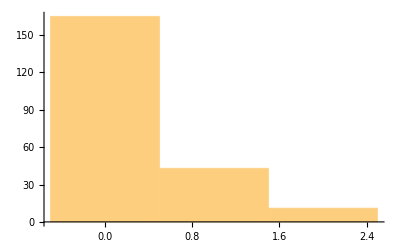

```mathematica
(* Distribution of point counts per chip before selecting and thinning *)
Histogram[allCorrespondingPointCounts]
```

#### Example of a “matched pair” of chips with maximal correspondingPointCount

```mathematica
MaximalBy[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat⟦2,1,All⟧,#["correspondingPointCount"]&,1]
```

{<|chip1→<|imageId→P41_02,segIndex→{2,3,1},primaryCorners→{{584.148,20.4231},{584.148,16.7564},{584.148,13.0897},{584.148,9.42308},{588.482,9.42308},{592.815,9.42308},{597.148,9.42308},{597.148,13.0897},{597.148,16.7564},{597.148,20.4231},{592.815,20.4231},{588.482,20.4231}},img→-Graphics-,rowRange→{108,119},columnRange→{585,598},chipTakeCorners→{{584.148,20.4231},{584.148,16.7564},{584.148,13.0897},{584.148,9.42308},{588.482,9.42308},{592.815,9.42308},{597.148,9.42308},{597.148,13.0897},{597.148,16.7564},{597.148,20.4231},{592.815,20.4231},{588.482,20.4231}},chip2segTF→TransformationFunction[(1 | 0 | 584
0 | 1 | 9
0 | 0 | 1)],imgLowHigh→{0.0371623,0.219145}|>,chip2→<|imageId→P41_01,segIndex→{2,3,1},secondaryCorners→{{245.289,104.874},{245.116,101.005},{245.209,96.9534},{245.788,92.5715},{248.624,93.4669},{252.313,93.7849},{256.347,93.8691},{256.308,97.8855},{256.42,101.797},{256.663,105.618},{252.559,105.582},{248.71,105.373}},img→-Graphics-,rowRange→{21,38},columnRange→{244,259},chipTakeCorners→{{243.694,101.375},{243.81,96.311},{244.533,90.8336},{248.078,91.9529},{252.69,92.3504},{257.733,92.4557},{257.683,97.4762},{257.823,102.366},{258.127,107.142},{252.997,107.097},{248.186,106.835},{243.909,106.212}},chip2segTF→TransformationFunction[(1 | 0 | 243
0 | 1 | 90
0 | 0 | 1)],imgLowHigh→{0.00188613,0.19194}|>,correspondingPointsImageScale1→4.5,correspondingPoints→{{{3.4557,5.61913},{9.57675,4.42809}},{{4.56624,8.98545},{10.1157,8.29629}}},cPts→{{{15.5506,25.2861},{43.0954,19.9264}},{{13.0439,26.4327},{42.37,21.6488}}},correspondingPointCount→2,segCorrespondingPoints→{{{587.456,14.6191},{593.577,13.4281}},{{247.566,98.9854},{253.116,98.2963}}},ffCorrespondingPoints→{{{724.381,587.456},{725.572,593.577}},{{640.015,247.566},{640.704,253.116}}},mpbdbdbpsfIndex→{{Key[P41_02],Key[P41_01],11,1},{Key[P41_02],Key[P41_01],11,2}}|>}

#### correspondingPointCount between datatakes prior to chip selection

```mathematica
preSelectPointCountsByDatatakeByDatatakeBy=Map[Total[#⟦All,"correspondingPointCount"⟧]&,matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,{2}]
```

<|P41_01→<|P41_01→0,P41_02→0,P41_03→0,P41_04→0,P41_05→0|>,P41_02→<|P41_01→9,P41_02→6,P41_03→7,P41_04→11,P41_05→11|>,P41_03→<|P41_01→0,P41_02→0,P41_03→0,P41_04→0,P41_05→0|>,P41_04→<|P41_01→0,P41_02→1,P41_03→2,P41_04→1,P41_05→1|>,P41_05→<|P41_01→2,P41_02→4,P41_03→4,P41_04→4,P41_05→2|>|>

```mathematica
Values[Values[preSelectPointCountsByDatatakeByDatatakeBy]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
9 | 6 | 7 | 11 | 11
0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 1 | 1
2 | 4 | 4 | 4 | 2)

```mathematica
({{0, 0, 0, 0, 0}, {7, 9, 14, 6, 5}, {0, 0, 0, 0, 0}, {0, 2, 4, 1, 3}, {1, 10, 10, 6, 3}})(**)
```

{{0,0,0,0,0},{7,9,14,6,5},{0,0,0,0,0},{0,2,4,1,3},{1,10,10,6,3}}

```mathematica
Total[Flatten[Values[Values[preSelectPointCountsByDatatakeByDatatakeBy]]]]
```

65

### Select Chip Pairs

```mathematica
(* Selecting chip pairs with "correspondingPointCount" >=6 .
Idea being that the perspective TransformationClass constraint used in ImageCorrespondingPoints is less likely to be wacky/degenerate, and correspondingPoints are more likely to be valid.
Could also add additional criteria based on FindGeometricTransform of points. *)matchedPairsWithCorrespondingPointsMultiBiased=Map[Select[#,#["correspondingPointCount"]≥correspondingPointCountThreshold&]&,matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,{2}];
```

```mathematica
selectedChipPairCounts=Map[Length,matchedPairsWithCorrespondingPointsMultiBiased,{2}] (* counts of chip pairs with "correspondingPointCount" >= selection threshold  *)
```

<|P41_01→<|P41_01→0,P41_02→0,P41_03→0,P41_04→0,P41_05→0|>,P41_02→<|P41_01→7,P41_02→4,P41_03→7,P41_04→8,P41_05→8|>,P41_03→<|P41_01→0,P41_02→0,P41_03→0,P41_04→0,P41_05→0|>,P41_04→<|P41_01→0,P41_02→1,P41_03→2,P41_04→1,P41_05→1|>,P41_05→<|P41_01→2,P41_02→4,P41_03→4,P41_04→4,P41_05→1|>|>

```mathematica
Values[Values[selectedChipPairCounts]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
7 | 4 | 7 | 8 | 8
0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 1 | 1
2 | 4 | 4 | 4 | 1)

```mathematica
correspondingPointCountByChipPairBiased=matchedPairsWithCorrespondingPointsMultiBiased⟦All,All,All,"correspondingPointCount"⟧;
```

```mathematica
correspondingPointCountByChipPairBiasedFlat=Flatten[Values[Values[correspondingPointCountByChipPairBiased]]];
```

```mathematica
totalCorrespondingPointCountByChipPairBiasedFlat=Total[correspondingPointCountByChipPairBiasedFlat] (* Total correspondingPointCount before chip level debias/thinning *)
```

65

### Debias/Thin Chip Pairs (* only when optimizing *)

```mathematica
(* Debias the chip pairs *)
(* only keep the strongest (largest feature matching strenght) keypoint *)
(* BlockRandom leftover from version that selected points at random. *)

(*BlockRandom[SeedRandom[23879];matchedPairsWithCorrespondingPointsMultiFull=Map[keepStrongestChipPairCorrespondingPoints[#,1 (* 1 to just keep strongest point *)]&,matchedPairsWithCorrespondingPointsMultiBiased,{3}];
]*)
```

```mathematica
matchedPairsWithCorrespondingPointsMultiFull=matchedPairsWithCorrespondingPointsMultiBiased; (* All points, no debias/thinning XXX*)
```

### Merge Matched Pairs with common Segment Indices

```mathematica
matchedPairsWithCorrespondingPointsMulti=matchedPairsWithCorrespondingPointsMultiFull; (*  Thined chips *)
```

```mathematica
matchedPairsGatheredBySegIDsMulti=Map[GatherBy[#,#⟦{"chip1","chip2"},"segIndex"⟧&]&,matchedPairsWithCorrespondingPointsMulti,{2}];
```

```mathematica
(* merge common segment pairs, just retains seegment relative and full frame relative CorrespondingPoints, *)
segmentPairsCorrespondingPointsMulit=Map[mergeMatchedPairsWithCommonSegIndices,matchedPairsGatheredBySegIDsMulti,{3}];
```

```mathematica
segmentPairsCorrespondingPointsMulitPreliminary=segmentPairsCorrespondingPointsMulit;
```

```mathematica
correspondingPointCountsMulti=Map[Length[#⟦"ffCorrespondingPoints",1⟧]&,segmentPairsCorrespondingPointsMulit,{3}]
```

<|P41_01→<|P41_01→{},P41_02→{},P41_03→{},P41_04→{},P41_05→{}|>,P41_02→<|P41_01→{1,1,2,2,1,1,1},P41_02→{1,1,4},P41_03→{2,2,1,1,1},P41_04→{1,1,1,2,1,4,1},P41_05→{1,1,1,2,3,3}|>,P41_03→<|P41_01→{},P41_02→{},P41_03→{},P41_04→{},P41_05→{}|>,P41_04→<|P41_01→{},P41_02→{1},P41_03→{1,1},P41_04→{1},P41_05→{1}|>,P41_05→<|P41_01→{1,1},P41_02→{1,1,1,1},P41_03→{1,1,1,1},P41_04→{1,1,1,1},P41_05→{2}|>|>

```mathematica
(* Segment to Segment correspondingPointCounts *)
correspondingPointCountsMultiValues=Flatten[Values[Values[correspondingPointCountsMulti]]];
```

```mathematica
{Total[correspondingPointCountsMultiValues],totalCorrespondingPointCountByChipPairBiasedFlat} (* Comparision of number of points after and before thinning. If there is no chip level thinning these should be same. *)
```

{65,65}

### Filter by Corresponding Points Distances

#### Review distribution of distances to nearest corresponding point

```mathematica
(*segCorrespondingPointDistances=Map[
Map[
Nearest[#-> "Distance",#,2]⟦All,2⟧&
,#["segCorrespondingPoints"]
]&
,segmentPairsCorrespondingPointsMulit,{3}];*)
```

```mathematica
segCorrespondingPointDistances=Map[
Map[
If[Length[#]>=2,Nearest[#-> "Distance",#,2]⟦All,2⟧
,{}]&
,#["segCorrespondingPoints"]
]&
,segmentPairsCorrespondingPointsMulit,{3}];
```

```mathematica
primarySegCorrespondingPointDistancesFlat=Flatten[Values[Values[segCorrespondingPointDistances⟦All,All,All,1⟧]],3
];
```

```mathematica
secondarySegCorrespondingPointDistancesFlat=Flatten[Values[Values[segCorrespondingPointDistances⟦All,All,All,2⟧]],3
];
```

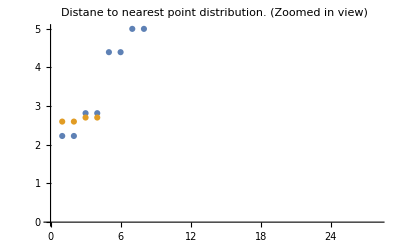

```mathematica
ListPlot[sortedDistancs=Sort/@{primarySegCorrespondingPointDistancesFlat,secondarySegCorrespondingPointDistancesFlat},PlotRange->{0,5}(*All*)
,PlotLabel->"Distane to nearest point distribution. (Zoomed in view)"] (* Used for picking correspondingPointDistanceThreshold value*)
```

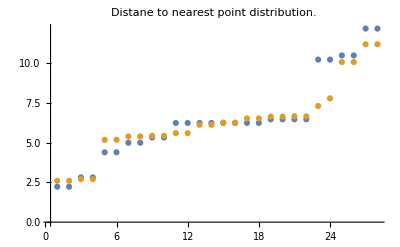

```mathematica
ListPlot[sortedDistancs,PlotRange->(*{0,5}*)All
,PlotLabel->"Distane to nearest point distribution."]
```

```mathematica
correspondingPointDistanceThreshold
```

2.

#### Remove Corresponding Points too close to neighbors

```mathematica
(* Filters out points that are closer than correspondingPointDistanceThreshold pixels to another point.  XXX This is possibly too agressive, would be better filter out points that if they were to be added to a chip accumulating points, they would be closer than correspondingPointDistanceThreshold. Currently if A is close to B and B is close to C then A,B,C are removed even though may only need to remove B to avoid any points being too close. *)
correspondingPointDistanceFilter[segmentPair_]:=Block[
{},
pickVector=MapThread[And,
Map[#≥correspondingPointDistanceThreshold&,
Map[
Nearest[#-> "Distance",#,2]⟦All,2⟧&
,segmentPair["segCorrespondingPoints"]
]
,{2}]
];(* pickVector True at positions where nearest corresponding point is ≥ correspondingPointDistanceThreshold pixels away *)
MapAt[Pick[#,pickVector]&,segmentPair,{{Key["segCorrespondingPoints"],1;;2}
,{Key["ffCorrespondingPoints"],1;;2}
,{Key["mpbdbdbpsfIndex"]}
}]
]
```

```mathematica
(* Filters out points that are closer than correspondingPointDistanceThreshold pixels to another point.  XXX This is possibly too agressive, would be better filter out points that if they were to be added to a chip accumulating points, they would be closer than correspondingPointDistanceThreshold. Currently if A is close to B and B is close to C then A,B,C are removed even though may only need to remove B to avoid any points being too close. *)
correspondingPointDistanceFilter[segmentPair_]:=Block[
{},
pickVector=MapThread[And,
Map[#≥correspondingPointDistanceThreshold&,
Map[
If[Length[#]>=2,Nearest[#-> "Distance",#,2]⟦All,2⟧
,{9999.}]&(* 9999. large value if only 1 point in segment to keep that point *)
,segmentPair["segCorrespondingPoints"]
]
,{2}]
];(* pickVector True at positions where nearest corresponding point is ≥ correspondingPointDistanceThreshold pixels away *)
MapAt[Pick[#,pickVector]&,segmentPair,{{Key["segCorrespondingPoints"],1;;2}
,{Key["ffCorrespondingPoints"],1;;2}
,{Key["mpbdbdbpsfIndex"]}
}]
]
```

```mathematica
segmentPairsCorrespondingPointsMulitRural=Map[correspondingPointDistanceFilter,segmentPairsCorrespondingPointsMulitPreliminary,{3}];(* Rural -> neighbors aren't too close *)
```

```mathematica
Total[Flatten[Values[Values[
Map[Length[#⟦"ffCorrespondingPoints",1⟧]&,segmentPairsCorrespondingPointsMulitRural,{3}]]]]]
```

65

### Setup to produce errorMetricAssociations

```mathematica
(* Optimization setup perofrmed to allow spread20RMSWeightedXYSumNoLimb to be run to produce errorMetricAssociations *)
```

```mathematica
optimizationSetup1
```

```mathematica
optimizationSingleOffsetsSetup
```

{dx,dy,dz,sa[1],sa[2],sa[3],sa[4],sa[5]}

```mathematica
optimizationSetup2
```

### Test spread20RMSWeightedXYSum

```mathematica
solution3={0.35291035315493585,{dx->6.723629124590102,dy->7.32396283119316,dz->50.828971363648826,sa[1]->-0.0032205786404103376,sa[2]->0.0012300867246229957,sa[3]->0.005259506390945292,sa[4]->0.0016704771457566076,sa[5]->0.00788925845786546}};(* Reference fit *)
```

```mathematica
debiasedSegmentPairsCorrespondingPointsMulti=segmentPairsCorrespondingPointsMulitRural;
```

```mathematica
spread20RMSWeightedXYSum@@(optModelParams=points2ModelParams[modelParamsFlat={paramsToOptimize}/.solution3[[2]]] );{controlPointsErrorPixels,limbFitErrorPixels} (* Generate errorMetricAssociations using preliminary optimization spacecraft positions *)
```

{0.50988,0.303717}

### Initial Position Tuning Optimization via NMinimize

```mathematica
debaisedCorrespondingPointCountsMulti=.
```

```mathematica
debiasedSegmentPairsCorrespondingPointsMulti=segmentPairsCorrespondingPointsMulitRural;
```

```mathematica
{perClusterOptimizationParameters,perClusterConstraints}={{},{}};
```

```mathematica
dim=Length[paramsToOptimize];
Print["dim ",dim];
Print["paramsToOptimize ",paramsToOptimize]
Print["perClusterOptimizationParameters ",perClusterOptimizationParameters];
Print["perClusterConstraints ",perClusterConstraints];
Print["perFileConstraints ",perFileConstraints];
```

dim 8

paramsToOptimize {dx,dy,dz,sa[1],sa[2],sa[3],sa[4],sa[5]}

perClusterOptimizationParameters {}

perClusterConstraints {}

perFileConstraints {-0.08<sa[1]<0.08,-0.08<sa[2]<0.08,-0.08<sa[3]<0.08,-0.08<sa[4]<0.08,-0.08<sa[5]<0.08}

```mathematica
lastStepCount=0;
lastEvalCount=0;
stepCount=0;
evalCount=0;
(*tunedPositionShiftsForOpt=tunedPositionShiftsLimbFit;
Print["tunedPositionShiftsForOpt =",tunedPositionShiftsForOpt];
initialPoints={Flatten[Values[Values/@tunedPositionShiftsForOpt⟦{"P34_01","P34_02"},{"dt","dx","dy","dz"}⟧]]
};*)
Print["initialPoints = ", initialPoints];
totalCorrespondingPointCount=Total[Flatten[Values[Values[
Map[Length[#⟦"ffCorrespondingPoints",1⟧]&,debiasedSegmentPairsCorrespondingPointsMulti,{3}]]]]];Print["totalCorrespondingPointCount ",totalCorrespondingPointCount];
Print["Start Time ",lastTime=(optStartTime=Now)];
AbsoluteTiming[
BlockRandom[SeedRandom[7654];
solnkGanymede1=NMinimize(*NMaximize*)[
(* function and constraints *)
Join[{
cs=( (*spread20RMSWeightedXYSumNoLimb*)spread20RMSWeightedXYSum[First[paramsToOptimize]
,parmsTable
])
(* constraints *)
(* camera model constraints *)

(*
(*,hFovLens*.95 < hFovTune < hFovLens*(2-.95)*)
,2/hFovLens*.95 < xfl < 2/hFovLens*(2-.95)
(*,(1/30<xdegPerPixel<1/24)*)
,(.001-.0007<xifdAdjustment<.001+.0007)
,-182.°(*-179.8°*)< α < -178.°
(*,88.°< β < 92.°
,-2.°< γ < 2.°*)
(*,-179.9°< α < 179.9°*)
(*,-179.9°< β < 179.9°
,-179.9°< γ < 179.9°*)
,-2°< β < 2°
,-2°< γ < 2°

,(-.04< a[1] < .04)
,(-.01< a[2] < .01)
(*,(-.01< b[1] < .01)
,(-.01< b[2] < .01)*)
,(-.2 607< a[4] < .2 607)
,(-.2 607< a[5] < .2 607)
,(.9 < cr[1] < 1.1)
,(.9 < cb[1] < 1.1)
,(-.01 < cr[3] < .01)
,(-.01 < cb[3] < .01)
*)

(*(* these are latest *)
,-182.°(*-179.8°*)< α < -178.°
,-2°< β < 2°
,-2°< γ < 2°*)

(*,-200.<dx<200.,-200.<dy<200.,-200.<dz<200.*)(* single position optimization constraints *)
},(*{}*)perClusterConstraints,perFileConstraints]

(* opt params *)
,paramsToOptimize


(* options *)
(*,Method->{"NelderMead"}*)
,Method->{"NelderMead"
(*,"PostProcess"-> False*)
(*,"ReflectRatio"->1,"ExpandRatio"-> 1+2/dim,"ContractRatio"-> 3/4-1/(2 dim),"ShrinkRatio"-> 1-1/dim*)(* These parameters are supposed to help when working with a large number of dimensions. They are mentiond at https://mathematica.stackexchange.com/questions/4700/shaving-the-last-50-ms-off-nminimize/4877#4877 *)
(*,"ReflectRatio"->2.,"ExpandRatio"-> 2.,"ContractRatio"-> .95,"ShrinkRatio"-> .95 (* from example in tutorial/ConstrainedOptimizationGlobalNumerical  *)*)
,"InitialPoints"-> initialPoints
} 
,StepMonitor:> 
(stepCount++;If[(msgTime=DateDifference[lastTime,curTime=Now,"Minute"])> logMessagePeriod||Mod[stepCount,500]==1
,
lastSoln=paramsToOptimize;
Print[{"StepRate=",(stepCount-lastStepCount)/msgTime
,"EvalRate=",(evalCount-lastEvalCount)/msgTime
,"Steps Evals" ,stepCount,evalCount," SPREAD",cs
,paramsToOptString
,paramsToOptimize
,lastTime=curTime,{"Elapsed time", DateDifference[optStartTime,curTime,"Minute"]}
}
];
(*Print[Stack[_]];*)
lastStepCount=stepCount;
lastEvalCount=evalCount;
]
)
,EvaluationMonitor :> evalCount++
(*,AccuracyGoal->6+1
,PrecisionGoal->4+1*)
,MaxIterations->4 12000
]
]
]
```

initialPoints = {{0,0,0,0,0,0,0,0}}

totalCorrespondingPointCount 65

Start Time Wed 27 Apr 2022 17:01:07GMT-7.

{StepRate=,61.238 per minute,EvalRate=,551.142 per minute,Steps Evals,1,9, SPREAD,1.35024,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{0.,0.,0.,0.,0.,0.,0.,0.},Wed 27 Apr 2022 17:01:08GMT-7.,{Elapsed time,0.0163297 min}}

{StepRate=,255.844 per minute,EvalRate=,419.004 per minute,Steps Evals,266,443, SPREAD,0.358437,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{0.0161835,0.0253653,0.0955863,-0.00426357,0.000339211,0.00497251,0.00132005,0.00795373},Wed 27 Apr 2022 17:02:10GMT-7.,{Elapsed time,1.05212 min}}

{StepRate=,5.80754 per minute,EvalRate=,1.93585 per minute,Steps Evals,275,446, SPREAD,0.357642,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{-0.0205687,-0.153138,1.51105,-0.00426324,0.000339126,0.00497247,0.00132007,0.00795404},Wed 27 Apr 2022 17:03:43GMT-7.,{Elapsed time,2.60183 min}}

{StepRate=,1.69272 per minute,EvalRate=,1.69272 per minute,Steps Evals,277,448, SPREAD,0.357642,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{-0.0205685,-0.153138,1.51105,-0.00426324,0.000339126,0.00497247,0.00132007,0.00795404},Wed 27 Apr 2022 17:04:54GMT-7.,{Elapsed time,3.78336 min}}

{227.199,{0.357642,{dx→-0.0205685,dy→-0.153138,dz→1.51105,sa[1]→-0.00426324,sa[2]→0.000339126,sa[3]→0.00497247,sa[4]→0.00132007,sa[5]→0.00795404}}}

```mathematica
{549.096575,{0.35291035315493585,{dx->6.723629124590102,dy->7.32396283119316,dz->50.828971363648826,sa[1]->-0.0032205786404103376,sa[2]->0.0012300867246229957,sa[3]->0.005259506390945292,sa[4]->0.0016704771457566076,sa[5]->0.00788925845786546}}};(* RootMeanSquare[{controlPointsErrorPixels,.25 limbFitErrorPixels}] 3 outlier rejection spread20RMSWeightedXYSum 81 points *)
```

```mathematica
{263.855338,{0.4196309368072408,{dx->-0.011127035483878587,dy->-0.06425528610861868,dz->0.06865458170466407,sa[1]->-0.005492656103858918,sa[2]->-0.0005893041102733808,sa[3]->0.00372862706707321,sa[4]->0.00021173716853184262,sa[5]->0.007018406031605489}}};(* 3 outlier rejection spread20RMSWeightedXYSum 81 points *)
```

```mathematica
{198.7009,{0.48891161809803446,{dx->-11.67442649066723,dy->51.78084225628438,dz->45.78592174736689,sa[1]->-0.0011246038421916357,sa[2]->0.0032360916685913368,sa[3]->0.00719582361011886,sa[4]->0.0035062945346324374,sa[5]->0.009486232821625654}}};(* 3 outlier rejection spread20RMSWeightedXYSumNoLimb 81 points *)
```

```mathematica
{142.534377,{0.5118410786411564,{dx->10.285164518134703,dy->5.711611824726786,dz->52.64644809308185,sa[1]->-0.001900247615235899,sa[2]->0.0024672612232042334,sa[3]->0.0064525355214087934,sa[4]->0.0026413610920492637,sa[5]->0.008919799139652584}}};(* 2 outlier rejection spread20RMSWeightedXYSumNoLimb 81 points *)
```

#### Previous Optimization Results

```mathematica
{143.102671,{0.7326873236238568,{dx->-0.6255631231987538,dy->6.178789719025525,dz->64.81779836116883,sa[1]->-0.00658159051029572,sa[2]->-0.0021836630479183006,sa[3]->0.0020374384110284135,sa[4]->-0.0015431659678786169,sa[5]->0.005281087613499873}}}(* spread20RMSWeightedXYSumNoLimb 81 points *)
```

{143.103,{0.732687,{dx→-0.625563,dy→6.17879,dz→64.8178,sa[1]→-0.00658159,sa[2]→-0.00218366,sa[3]→0.00203744,sa[4]→-0.00154317,sa[5]→0.00528109}}}

```mathematica
{234.23564,{0.40634969733051596,{dx->14.775266644000043,dy->5.406906485935093,dz->39.84757476175924,sa[1]->-0.005927976191297877,sa[2]->-0.0007389168082483725,sa[3]->0.003777773025228299,sa[4]->0.00037096159734254126,sa[5]->0.0070176104411266505}}}(* NO "PostProcess"-> False, NO ReflectRatio... *)
```

{234.236,{0.40635,{dx→14.7753,dy→5.40691,dz→39.8476,sa[1]→-0.00592798,sa[2]→-0.000738917,sa[3]→0.00377777,sa[4]→0.000370962,sa[5]→0.00701761}}}

```mathematica
{67.554648,{0.4869368216133568,{dx->-7.279707765898364,dy->24.59711856596851,dz->45.79001693463747,sa[1]->-0.001968119311252789,sa[2]->0.0027574041893734646,sa[3]->0.007018186689021305,sa[4]->0.0033615682085025088,sa[5]->0.00937934387930398}}}(* NO "PostProcess"-> False, NO ReflectRatio... , spread20RMSWeightedXYSumNoLimb *)
```

{67.5546,{0.486937,{dx→-7.27971,dy→24.5971,dz→45.79,sa[1]→-0.00196812,sa[2]→0.0027574,sa[3]→0.00701819,sa[4]→0.00336157,sa[5]→0.00937934}}}

```mathematica
{17.733158,{0.48700932525106133,{dx->-3.432592637447984,dy->24.763410797442525,dz->45.76684734366477,sa[1]->-0.001968119311252789,sa[2]->0.0027574041893734646,sa[3]->0.007018186689021305,sa[4]->0.0033615682085025088,sa[5]->0.00937934387930398}}} (* NO ReflectRatio... , spread20RMSWeightedXYSumNoLimb *)
```

{17.7332,{0.487009,{dx→-3.43259,dy→24.7634,dz→45.7668,sa[1]→-0.00196812,sa[2]→0.0027574,sa[3]→0.00701819,sa[4]→0.00336157,sa[5]→0.00937934}}}

```mathematica
{12.399135,{0.5164522539616382,{dx->-0.06895531271157446,dy->0.10711770657837068,dz->0.06238160363575789,sa[1]->0.0015898458622102172,sa[2]->0.006006750132573244,sa[3]->0.01019879271282768,sa[4]->0.006597886635319107,sa[5]->0.012183762268868276}}}(*spread20RMSWeightedXYSumNoLimb*)
```

{12.3991,{0.516452,{dx→-0.0689553,dy→0.107118,dz→0.0623816,sa[1]→0.00158985,sa[2]→0.00600675,sa[3]→0.0101988,sa[4]→0.00659789,sa[5]→0.0121838}}}

```mathematica
{50.36066,{0.24762110669510365,{dx->0.09777734322928874,dy->-0.18106213346107047,dz->-0.03247472698631834,sa[1]->-0.005559841734937723,sa[2]->-0.0008098748008104575,sa[3]->0.0037588814262441562,sa[4]->0.0003370392413861697,sa[5]->0.00654294962931822}}}(* unCorrectedSegments filterReductionPix=5, edge new Edge limbFilt4 uniform weight*)
```

{50.3607,{0.247621,{dx→0.0977773,dy→-0.181062,dz→-0.0324747,sa[1]→-0.00555984,sa[2]→-0.000809875,sa[3]→0.00375888,sa[4]→0.000337039,sa[5]→0.00654295}}}

```mathematica
{86.880493,{0.2618873858411802,{dx->0.1980536951349383,dy->-0.15577320544999843,dz->0.35828172529393293,sa[1]->-0.005698413159393029,sa[2]->-0.001079534353306557,sa[3]->0.0037937982849380178,sa[4]->0.0003402598429276799,sa[5]->0.0071054062048207765}}};(* NMaximize GradientFilter[#,2]& *)
```

```mathematica
{85.54396,{0.2618873858411802,{dx->0.1980536951349383,dy->-0.15577320544999843,dz->0.35828172529393293,sa[1]->-0.005698413159393029,sa[2]->-0.001079534353306557,sa[3]->0.0037937982849380178,sa[4]->0.0003402598429276799,sa[5]->0.0071054062048207765}}};(* NMaximize 0-GradientFilter[#,2]& *)
```

```mathematica
{48.377742,{0.24762110669510365,{dx->0.09777734322928874,dy->-0.18106213346107047,dz->-0.03247472698631834,sa[1]->-0.005559841734937723,sa[2]->-0.0008098748008104575,sa[3]->0.0037588814262441562,sa[4]->0.0003370392413861697,sa[5]->0.00654294962931822}}};(* unCorrectedSegments filterReductionPix=5, edge new Edge limbFilt4 uniform weight*)
```

```mathematica
{47.991205,{0.2908149687835176,{dx->0.057365954136886076,dy->-0.24104269067955472,dz->-0.2704784061587784,sa[1]->-0.005890552262699589,sa[2]->-0.0008463416362385168,sa[3]->0.003797221458558809,sa[4]->0.00001441027072890283,sa[5]->0.007035228224990624}}} ;(* filterReductionPix=5, edge new Edge limbFilt4 uniform weight *)
```

```mathematica
{68.286422,{0.36174473118236433,{dx->0.10892782145494176,dy->-0.259742969328124,dz->-0.1957027540822506,sa[1]->-0.005512258087481518,sa[2]->-0.0007889216604540035,sa[3]->0.0037653254012991657,sa[4]->0.00006635921771355052,sa[5]->0.006991674497541721}}};(* new Edge limbFilt4 uniform weight *)
```

```mathematica
{46.563513,{0.3420850181851574,{dx->-0.0017671824538300798,dy->-0.11771208504962923,dz->-0.010271060071647265,sa[1]->-0.0055030142767454595,sa[2]->-0.0008016920256347276,sa[3]->0.0038773085986214344,sa[4]->0.00007243417332550651,sa[5]->0.00699606822163636}}};(* new Edge limbFilt4 WeightedData[Values[limbFitResults⟦All,"meanOffsets"⟧],{1./8.,1,1,1,1}]*)
```

```mathematica
{38.859244,{0.8819500054008584,{dx->0.056492625207088906,dy->-0.1646368937420563,dz->-0.15592280982841622,sa[1]->-0.007013463844213856,sa[2]->-0.0008773683143123209,sa[3]->0.0038745091906363096,sa[4]->0.00011042632411759584,sa[5]->0.0066714954997399625}}};(* uniform weight *)
```

#### Check per-datatake Limb Fit

```mathematica
spread20RMSWeightedXYSum@@(optModelParams=points2ModelParams[modelParamsFlat={paramsToOptimize}/.solnkGanymede1[[2]]] );{controlPointsErrorPixels,limbFitErrorPixels}(* need to run to set limbFitResults when optimizing without limb fit, but still wanting to see limbFitResults after optimization *)
```

{0.49992,0.307135}

```mathematica
{0.4932810296855285,0.30371724956657536}(* RootMeanSquare[{controlPointsErrorPixels,.25 limbFitErrorPixels}] 3 outlier rejection spread20RMSWeightedXYSum 81 points *)
```

{0.493281,0.303717}

```mathematica
{0.48891161809803446,0.34936506897071146}(* 3 outlier rejection spread20RMSWeightedXYSumNoLimb 81 points *)
```

{0.488912,0.349365}

```mathematica
{0.5383855554810769,0.24964222379392736}(* 3 outlier rejection spread20RMSWeightedXYSum 81 points *)
```

{0.538386,0.249642}

```mathematica
limbFitResults[[All,{"meanOffsets","totalLimbPts"}]]
```

<|P41_01→<|meanOffsets→0.332013,totalLimbPts→76|>,P41_02→<|meanOffsets→0.272343,totalLimbPts→77|>,P41_03→<|meanOffsets→0.31595,totalLimbPts→78|>,P41_04→<|meanOffsets→0.299714,totalLimbPts→76|>,P41_05→<|meanOffsets→0.312416,totalLimbPts→81|>|>

```mathematica
<|"P41_01"-><|"meanOffsets"->0.3502793246144919,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.28304087800917205,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.27075139784182495,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.2914536959540687,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.31648304571690794,"totalLimbPts"->81|>|>;(* RootMeanSquare[{controlPointsErrorPixels,.25 limbFitErrorPixels}] 3 outlier rejection spread20RMSWeightedXYSum 81 points *)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.3001772753134566,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.22571008356269934,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.22158990225468117,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.23659884431792497,"totalLimbPts"->77|>,"P41_05"-><|"meanOffsets"->0.25587821938097477,"totalLimbPts"->80|>|>;(* 3 outlier rejection spread20RMSWeightedXYSumNoLimb 81 points *)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.4299153949801908,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.40538537850476464,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.2898210614609222,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.30157070755223303,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.29355419570879066,"totalLimbPts"->81|>|>;(* 2 outlier rejection spread20RMSWeightedXYSumNoLimb 81 points *)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.5354201525497513,"totalLimbPts"->78|>,"P41_02"-><|"meanOffsets"->0.446551926917844,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.43012207509548983,"totalLimbPts"->79|>,"P41_04"-><|"meanOffsets"->0.3736499446416641,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.31974408186818815,"totalLimbPts"->82|>|>;(* spread20RMSWeightedXYSumNoLimb 81 points *)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.3442644263544169,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.23270080584802894,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.2421323282715793,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.25626109247458734,"totalLimbPts"->77|>,"P41_05"-><|"meanOffsets"->0.30021425732993523,"totalLimbPts"->80|>|>;(**)
```

#### Previous Optimization Results

```mathematica
<|"P41_01"-><|"meanOffsets"->0.29998665239269795,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.22377122380323697,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.22169870941434056,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.23394079613621885,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.25027364291017873,"totalLimbPts"->80|>|>;(* unCorrectedSegments filterReductionPix=5, edge new Edge limbFilt4 uniform weight*)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.20885377367468258,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.1391694987942646,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.40251011821704036,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.16714998864029584,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.2999724190176269,"totalLimbPts"->81|>|>;(* NMaximize GradientFilter[#,2]& *)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.29998665239269795,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.22377122380323697,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.22169870941434056,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.23394079613621885,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.25027364291017873,"totalLimbPts"->80|>|>;(* unCorrectedSegments filterReductionPix=5, edge new Edge limbFilt4 uniform weight*)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.4415172362239147,"totalLimbPts"->99,"limbSampleSeparationPixels"-><|{1,1,1}->2.8519210733697373,{1,2,1}->2.811897348729517,{2,2,1}->2.859274174196186,{2,3,1}->2.787742402536015,{3,4,1}->2.7998423431171098|>|>,"P41_02"-><|"meanOffsets"->0.3237225444478549,"totalLimbPts"->97,"limbSampleSeparationPixels"-><|{1,2,1}->2.6751549265851717,{2,3,1}->2.647684712802656,{2,4,1}->2.6412109857088137,{3,4,1}->2.6474716669738787,{3,5,1}->2.6473043841727835|>|>,"P41_03"-><|"meanOffsets"->0.3539261634484985,"totalLimbPts"->97,"limbSampleSeparationPixels"-><|{1,1,1}->2.5807504433248196,{1,2,1}->2.5525251737152344,{2,3,1}->2.5348483983003702,{3,4,1}->2.531889268990376,{3,5,1}->2.542168545652123|>|>,"P41_04"-><|"meanOffsets"->0.30127187196017785,"totalLimbPts"->93,"limbSampleSeparationPixels"-><|{1,1,1}->2.446875927987816,{1,2,1}->2.432516680932406,{2,3,1}->2.41252920355579,{3,4,1}->2.4111280660178647|>|>,"P41_05"-><|"meanOffsets"->0.37220159459175417,"totalLimbPts"->108,"limbSampleSeparationPixels"-><|{1,1,1}->2.1914191486564993,{1,2,1}->2.1875667811308537,{2,3,1}->2.1748026144589345,{3,4,1}->2.1716217323063027,{3,5,1}->2.1714446197402757|>|>|>;(* new Edge limbFilt4 uniform weight *)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->0.4409857020205395,"totalLimbPts"->99,"limbSampleSeparationPixels"-><|{1,1,1}->2.8519180903824033,{1,2,1}->2.8118944920233804,{2,2,1}->2.8592704949847993,{2,3,1}->2.78773912094333,{3,4,1}->2.799838304089824|>|>,"P41_02"-><|"meanOffsets"->0.32354679523028684,"totalLimbPts"->97,"limbSampleSeparationPixels"-><|{1,2,1}->2.6751534732480295,{2,3,1}->2.6476822109543576,{2,4,1}->2.6412073652834835,{3,4,1}->2.6474680313639483,{3,5,1}->2.6472997255685176|>|>,"P41_03"-><|"meanOffsets"->0.3533647568214822,"totalLimbPts"->96,"limbSampleSeparationPixels"-><|{1,1,1}->2.5807367990929446,{1,2,1}->2.552347426316994,{2,3,1}->2.534843088117887,{3,4,1}->2.531886967957513,{3,5,1}->2.5421699068312735|>|>,"P41_04"-><|"meanOffsets"->0.300805568718637,"totalLimbPts"->93,"limbSampleSeparationPixels"-><|{1,1,1}->2.446872416694139,{1,2,1}->2.4325132664862332,{2,3,1}->2.412525754849261,{3,4,1}->2.4111246237958035|>|>,"P41_05"-><|"meanOffsets"->0.3719874859622897,"totalLimbPts"->108,"limbSampleSeparationPixels"-><|{1,1,1}->2.191416034828735,{1,2,1}->2.18756367599641,{2,3,1}->2.1747995334693506,{3,4,1}->2.17161865360261,{3,5,1}->2.1714415291586553|>|>|>;(* new Edge WeightedData[Values[limbFitResults⟦All,"meanOffsets"⟧],{1./8.,1,1,1,1}]*)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->1.6205039397648555,"totalLimbPts"->101,"limbSampleSeparationPixels"-><|{1,1,1}->2.8520121172286284,{1,2,1}->2.8119058931855174,{2,2,1}->2.859345907236576,{2,3,1}->2.793707844490915,{3,4,1}->2.799870972626139|>|>,"P41_02"-><|"meanOffsets"->0.675277856879474,"totalLimbPts"->97,"limbSampleSeparationPixels"-><|{1,2,1}->2.6751646479639906,{2,3,1}->2.6476894116285123,{2,4,1}->2.641209383477298,{3,4,1}->2.6474706966985404,{3,5,1}->2.647298299042462|>|>,"P41_03"-><|"meanOffsets"->0.5997010114964118,"totalLimbPts"->96,"limbSampleSeparationPixels"-><|{1,1,1}->2.580739908348823,{1,2,1}->2.5523504159447974,{2,3,1}->2.5348461498660413,{3,4,1}->2.5318899659443934,{3,5,1}->2.542172964159702|>|>,"P41_04"-><|"meanOffsets"->0.4620082153768469,"totalLimbPts"->93,"limbSampleSeparationPixels"-><|{1,1,1}->2.4468729511713434,{1,2,1}->2.4325129990572396,{2,3,1}->2.4125280192931333,{3,4,1}->2.4111283028959525|>|>,"P41_05"-><|"meanOffsets"->0.4837902056493072,"totalLimbPts"->108,"limbSampleSeparationPixels"-><|{1,1,1}->2.1914317703650017,{1,2,1}->2.1875838183162513,{2,3,1}->2.1748085099930563,{3,4,1}->2.1716161069177025,{3,5,1}->2.1714426426821074|>|>|>;(* uniform weight *)
```

```mathematica
solnkGanymede1
```

{0.357642,{dx→-0.0205685,dy→-0.153138,dz→1.51105,sa[1]→-0.00426324,sa[2]→0.000339126,sa[3]→0.00497247,sa[4]→0.00132007,sa[5]→0.00795404}}

### FindMinimum based optimization

```mathematica
lastStepCount=0;
lastEvalCount=0;
stepCount=0;
evalCount=0;
(*tunedPositionShiftsForOpt=tunedPositionShiftsLimbFit;
Print["tunedPositionShiftsForOpt =",tunedPositionShiftsForOpt];
initialPoints={Flatten[Values[Values/@tunedPositionShiftsForOpt⟦{"P34_01","P34_02"},{"dt","dx","dy","dz"}⟧]]
};*)
Print["initialPoints = ", initialPoints];
totalCorrespondingPointCount=Total[Flatten[Values[Values[
Map[Length[#⟦"ffCorrespondingPoints",1⟧]&,debiasedSegmentPairsCorrespondingPointsMulti,{3}]]]]];Print["totalCorrespondingPointCount ",totalCorrespondingPointCount];
Print["Start Time ",lastTime=(optStartTime=Now)];
AbsoluteTiming[
BlockRandom[SeedRandom[7654];
solnkGanymedeFindMinimum=FindMinimum(*FindMaximum*)[(cs= spread20RMSWeightedXYSum(*spread20RMSWeightedXYSumNoLimb*)[First[paramsToOptimize]
,parmsTable
]),(*paramsToOptimize*){paramsToOptimize,initialPoints⟦1⟧}ᵀ
,Method->"PrincipalAxis" 
,StepMonitor:> 
(stepCount++;If[(msgTime=DateDifference[lastTime,curTime=Now,"Minute"])> logMessagePeriod||Mod[stepCount,500]==1
,
lastSoln=paramsToOptimize;
Print[{"StepRate=",(stepCount-lastStepCount)/msgTime
,"EvalRate=",(evalCount-lastEvalCount)/msgTime
,"Steps Evals" ,stepCount,evalCount," SPREAD",cs
,paramsToOptString
,paramsToOptimize
,lastTime=curTime,{"Elapsed time", DateDifference[optStartTime,curTime,"Minute"]}
}
];
(*Print[Stack[_]];*)
lastStepCount=stepCount;
lastEvalCount=evalCount;
]
)
,EvaluationMonitor :> evalCount++]
]
]
```

initialPoints = {{0,0,0,0,0,0,0,0}}

totalCorrespondingPointCount 65

Start Time Wed 27 Apr 2022 17:04:58GMT-7.

{StepRate=,3.7291 per minute,EvalRate=,611.572 per minute,Steps Evals,1,164, SPREAD,0.628665,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{-63.3338,-88.2204,102.595,-0.00512261,-0.00320814,5.34919×10^-6,-0.00351647,0.00255162},Wed 27 Apr 2022 17:05:14GMT-7.,{Elapsed time,0.268161 min}}

{StepRate=,3.17868 per minute,EvalRate=,611.1 per minute,Steps Evals,5,933, SPREAD,0.353236,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{-19.6599,-11.4628,13.6015,-0.00602877,-0.00114886,0.00353986,-0.0000445835,0.00671607},Wed 27 Apr 2022 17:06:29GMT-7.,{Elapsed time,1.52655 min}}

{StepRate=,3.5101 per minute,EvalRate=,611.634 per minute,Steps Evals,9,1630, SPREAD,0.35314,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{-19.2113,-11.1996,13.309,-0.00595273,-0.00111504,0.00355811,-0.0000216795,0.00670344},Wed 27 Apr 2022 17:07:38GMT-7.,{Elapsed time,2.66612 min}}

{StepRate=,3.74146 per minute,EvalRate=,611.728 per minute,Steps Evals,13,2284, SPREAD,0.353133,{dx, dy, dz, sa[1], sa[2], sa[3], sa[4], sa[5]},{-19.1344,-11.2049,13.3224,-0.00594682,-0.00112153,0.00356428,-0.0000339332,0.00669704},Wed 27 Apr 2022 17:08:42GMT-7.,{Elapsed time,3.73522 min}}

{239.501,{0.353133,{dx→-19.1344,dy→-11.2049,dz→13.3224,sa[1]→-0.00594682,sa[2]→-0.00112153,sa[3]→0.00356428,sa[4]→-0.0000339328,sa[5]→0.00669704}}}

```mathematica
{430.350163,{0.35404495330692887,{dx->2.315997778511568,dy->-8.747914759822772,dz->46.659157200182435,sa[1]->-0.003664314789461585,sa[2]->0.0008050797390022853,sa[3]->0.004860270282151245,sa[4]->0.00129633042047811,sa[5]->0.0075555316815457615}}};(* RootMeanSquare[{controlPointsErrorPixels,.25 limbFitErrorPixels}] 3 outlier rejection spread20RMSWeightedXYSum 81 points *)
```

```mathematica
{215.525393,{0.40899442745408643,{dx->-12.143674282743204,dy->-79.59074206685803,dz->11.407481250681345,sa[1]->-0.009161595992166012,sa[2]->-0.004154363105421256,sa[3]->0.00041077931767812844,sa[4]->-0.002896245289519808,sa[5]->0.004013001797924472}}};(*spread20RMSWeightedXYSum*)
```

```mathematica
{114.783788,{0.48683530260219,{dx->-24.18149115593265,dy->13.284897056778714,dz->36.14122172135029,sa[1]->-0.0037318909568724943,sa[2]->0.0011601214845237174,sa[3]->0.005501449640438335,sa[4]->0.0020249417086743125,sa[5]->0.008198081695333327}}};(*spread20RMSWeightedXYSumNoLimb*)
```

```mathematica
{90.526714,{0.24830256290210576,{dx->-6.710483749232426,dy->-14.461597064351615,dz->-31.352739018005398,sa[1]->-0.006755074404097531,sa[2]->-0.001809828997722938,sa[3]->0.0028965100570866125,sa[4]->-0.0003719220730680164,sa[5]->0.005763948456043701}}};(* unCorrectedSegments filterReductionPix=5, edge new Edge limbFilt4 uniform weight*)
```

```mathematica
{97.000417,{0.2619375034592467,{dx->-16.24060370235155,dy->-88.87751276772622,dz->-27.53247288276616,sa[1]->-0.010003719154520306,sa[2]->-0.005274920517150639,sa[3]->-0.00026654013228590506,sa[4]->-0.0034196320326394473,sa[5]->0.0029907856595028}}};(* FindMaximum GradientFilter[#,2]& *)
```

```mathematica
{85.7939,{0.24830256290210576,{dx->-6.710483749232426,dy->-14.461597064351615,dz->-31.352739018005398,sa[1]->-0.006755074404097531,sa[2]->-0.001809828997722938,sa[3]->0.0028965100570866125,sa[4]->-0.0003719220730680164,sa[5]->0.005763948456043701}}};(* unCorrectedSegments filterReductionPix=5, edge new Edge limbFilt4 uniform weight*)
```

```mathematica
{277.335958,{0.23515283934707645,{dx->-24.2661956592955,dy->-9.831823227736159,dz->-21.18049046416466,sa[1]->-0.006882516463672039,sa[2]->-0.0018733142931677588,sa[3]->0.0031146942870210023,sa[4]->-0.0004405761240190863,sa[5]->0.0066360402874042265}}};(* filterReductionPix=5, edge new Edge limbFilt4 uniform weight *)
```

```mathematica
{69.404647,{0.33330627445809985,{dx->-13.213113416827687,dy->-11.106365149353364,dz->-2.337014318701601,sa[1]->-0.006103643610403495,sa[2]->-0.00142526368446755,sa[3]->0.003306373474077835,sa[4]->-0.0004285826825518137,sa[5]->0.006528962639623869}}};(* new Edge limbFilt4 uniform weight *)
```

```mathematica
spread20RMSWeightedXYSum@@(optModelParams=points2ModelParams[modelParamsFlat={paramsToOptimize}/.solnkGanymedeFindMinimum[[2]]] );{controlPointsErrorPixels,limbFitErrorPixels}(* need to run to set limbFitResults when optimizing without limb fit, but still wanting to see limbFitResults after optimization *)
```

{0.493425,0.308209}

```mathematica
{0.4938731141599436,0.32948456799480474}(* RootMeanSquare[{controlPointsErrorPixels,.25 limbFitErrorPixels}] 3 outlier rejection spread20RMSWeightedXYSum 81 points *)
```

{0.493873,0.329485}

```mathematica
limbFitResults[[All,{"meanOffsets","totalLimbPts"}]]
```

<|P41_01→<|meanOffsets→0.400151,totalLimbPts→76|>,P41_02→<|meanOffsets→0.338079,totalLimbPts→77|>,P41_03→<|meanOffsets→0.235665,totalLimbPts→78|>,P41_04→<|meanOffsets→0.262652,totalLimbPts→76|>,P41_05→<|meanOffsets→0.275718,totalLimbPts→81|>|>

```mathematica
<|"P41_01"-><|"meanOffsets"->0.37480993992128214,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.25868205097201585,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.21689057394187564,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.2360639278501223,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.25750335077755154,"totalLimbPts"->80|>|>(**)
```

<|P41_01→<|meanOffsets→0.37481,totalLimbPts→76|>,P41_02→<|meanOffsets→0.258682,totalLimbPts→77|>,P41_03→<|meanOffsets→0.216891,totalLimbPts→78|>,P41_04→<|meanOffsets→0.236064,totalLimbPts→76|>,P41_05→<|meanOffsets→0.257503,totalLimbPts→80|>|>

```mathematica
<|"P41_01"-><|"meanOffsets"->0.20786223501751297,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.13897318789711247,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.40357829267397904,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.16716678019024825,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.2995260459037475,"totalLimbPts"->81|>|>(* FindMaximum GradientFilter[#,2]& *)
```

<|P41_01→<|meanOffsets→0.207862,totalLimbPts→76|>,P41_02→<|meanOffsets→0.138973,totalLimbPts→77|>,P41_03→<|meanOffsets→0.403578,totalLimbPts→78|>,P41_04→<|meanOffsets→0.167167,totalLimbPts→76|>,P41_05→<|meanOffsets→0.299526,totalLimbPts→81|>|>

```mathematica
<|"P41_01"-><|"meanOffsets"->0.29914965326162546,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.220493935090913,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.2192107220299733,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.23903389496263117,"totalLimbPts"->76|>,"P41_05"-><|"meanOffsets"->0.2548964097693471,"totalLimbPts"->81|>|>(* unCorrectedSegments filterReductionPix=5, edge new Edge limbFilt4 uniform weight*)
```

<|P41_01→<|meanOffsets→0.29915,totalLimbPts→76|>,P41_02→<|meanOffsets→0.220494,totalLimbPts→77|>,P41_03→<|meanOffsets→0.219211,totalLimbPts→78|>,P41_04→<|meanOffsets→0.239034,totalLimbPts→76|>,P41_05→<|meanOffsets→0.254896,totalLimbPts→81|>|>

```mathematica
<|"P41_01"-><|"meanOffsets"->0.2677011469218027,"totalLimbPts"->76|>,"P41_02"-><|"meanOffsets"->0.22617804356994314,"totalLimbPts"->77|>,"P41_03"-><|"meanOffsets"->0.21678113356943074,"totalLimbPts"->78|>,"P41_04"-><|"meanOffsets"->0.2094383240411324,"totalLimbPts"->77|>,"P41_05"-><|"meanOffsets"->0.2506100683527665,"totalLimbPts"->81|>|>;(* filterReductionPix=5, edge new Edge limbFilt4 uniform weight *)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->1.6325031506108547,"totalLimbPts"->101,"limbSampleSeparationPixels"-><|{1,1,1}->2.8516122181250623,{1,2,1}->2.8115275372396877,{2,2,1}->2.858986319936188,{2,3,1}->2.7934096332557723,{3,4,1}->2.799640351716317|>|>,"P41_02"-><|"meanOffsets"->0.6758349512118039,"totalLimbPts"->97,"limbSampleSeparationPixels"-><|{1,2,1}->2.6750111259565705,{2,3,1}->2.647534110266201,{2,4,1}->2.641029585480201,{3,4,1}->2.647298134897921,{3,5,1}->2.6471203686268354|>|>,"P41_03"-><|"meanOffsets"->0.5995878082414544,"totalLimbPts"->96,"limbSampleSeparationPixels"-><|{1,1,1}->2.580633762234373,{1,2,1}->2.5522453505635645,{2,3,1}->2.5347437535928465,{3,4,1}->2.531786582578607,{3,5,1}->2.542070219591509|>|>,"P41_04"-><|"meanOffsets"->0.4638615108936304,"totalLimbPts"->93,"limbSampleSeparationPixels"-><|{1,1,1}->2.446821972704835,{1,2,1}->2.432466577658747,{2,3,1}->2.412480502582076,{3,4,1}->2.411081131085835|>|>,"P41_05"-><|"meanOffsets"->0.4837990991125278,"totalLimbPts"->108,"limbSampleSeparationPixels"-><|{1,1,1}->2.191441989389183,{1,2,1}->2.187608592288489,{2,3,1}->2.1748336060836477,{3,4,1}->2.1716411888035507,{3,5,1}->2.1714840545506067|>|>|>;(* old limbFilt3 Edge WeightedData[Values[limbFitResults⟦All,"meanOffsets"⟧],{1./8.,1,1,1,1}]*)
```

```mathematica
<|"P41_01"-><|"meanOffsets"->1.598809524964873,"totalLimbPts"->101,"limbSampleSeparationPixels"-><|{1,1,1}->2.852345265392171,{1,2,1}->2.812215612184947,{2,2,1}->2.859655609028635,{2,3,1}->2.7939490469902992,{3,4,1}->2.80005973083688|>|>,"P41_02"-><|"meanOffsets"->0.6711246607796356,"totalLimbPts"->97,"limbSampleSeparationPixels"-><|{1,2,1}->2.675294304670789,{2,3,1}->2.6478147182875795,{2,4,1}->2.6413431567169705,{3,4,1}->2.6476031695277813,{3,5,1}->2.647426388139827|>|>,"P41_03"-><|"meanOffsets"->0.6055659766684395,"totalLimbPts"->96,"limbSampleSeparationPixels"-><|{1,1,1}->2.5808202888104153,{1,2,1}->2.552422830034735,{2,3,1}->2.5349232149432237,{3,4,1}->2.531963446973383,{3,5,1}->2.5422493111947864|>|>,"P41_04"-><|"meanOffsets"->0.4783862060717037,"totalLimbPts"->93,"limbSampleSeparationPixels"-><|{1,1,1}->2.44690803819323,{1,2,1}->2.4325391951695394,{2,3,1}->2.4125587712739973,{3,4,1}->2.4111585628912673|>|>,"P41_05"-><|"meanOffsets"->0.49552891798386417,"totalLimbPts"->108,"limbSampleSeparationPixels"-><|{1,1,1}->2.1914205760865353,{1,2,1}->2.187555361385635,{2,3,1}->2.174779251203348,{3,4,1}->2.1715870271705797,{3,5,1}->2.1713957558410435|>|>|>;(* uniform weight *)
```

```mathematica
{0.622530672532608,{dx->-2.422767743188159,dy->-26.41969349793497,dz->0.0015976759592944442,sa[1]->-0.008193273512346572,sa[2]->-0.002035238862233306,sa[3]->0.0027476481412609245,sa[4]->-0.0009667470404600006,sa[5]->0.0056879643618545864}};(* old limbFilt3 Edge WeightedData[Values[limbFitResults⟦All,"meanOffsets"⟧],{1./8.,1,1,1,1}]*)
```

```mathematica
{0.8772357300339884,{dx->7.457636139064949,dy->20.782258626588096,dz->-0.15651353987955732,sa[1]->-0.006042947517373023,sa[2]->-0.000029678972024558567,sa[3]->0.004799843044353913,sa[4]->0.0009872844448076735,sa[5]->0.007478283404199291}};(* uniform weight *)
```

### Select Solution

```mathematica
solnkGanymedeFindMinimum
```

{0.353133,{dx→-19.1344,dy→-11.2049,dz→13.3224,sa[1]→-0.00594682,sa[2]→-0.00112153,sa[3]→0.00356428,sa[4]→-0.0000339328,sa[5]→0.00669704}}

```mathematica
spread20RMSWeightedXYSum@@(optModelParams=points2ModelParams[modelParamsFlat={paramsToOptimize}/.solnkGanymedeFindMinimum[[2]]] );{controlPointsErrorPixels,limbFitErrorPixels}
```

{0.493425,0.308209}

```mathematica
solnkGanymede1 (* NMinimize *)
```

{0.357642,{dx→-0.0205685,dy→-0.153138,dz→1.51105,sa[1]→-0.00426324,sa[2]→0.000339126,sa[3]→0.00497247,sa[4]→0.00132007,sa[5]→0.00795404}}

```mathematica
spread20RMSWeightedXYSum@@(optModelParams=points2ModelParams[modelParamsFlat={paramsToOptimize}/.solnkGanymede1[[2]]] );{controlPointsErrorPixels,limbFitErrorPixels}
```

{0.49992,0.307135}

```mathematica
{0.4869368216133568,0.4035420275935553}(* spread20RMSWeightedXYSumNoLimb *)
```

{0.486937,0.403542}

```mathematica
solutionResults={solnkGanymede1,solnkGanymedeFindMinimum};
```

```mathematica
solutionNames={"solnkGanymede1","solnkGanymedeFindMinimum"};
```

```mathematica
solutionOrdering=OrderingBy[solutionResults,#[[1]]&]
```

{2,1}

```mathematica
solutionOrdering={1,2} (* force solnkGanymede1 *)
```

{1,2}

```mathematica
(*solution=First@MinimalBy[{solnkGanymede1,solnkGanymedeFindMinimum},#[[1]]&]*)
```

```mathematica
solution=solutionResults⟦solutionOrdering[[1]]⟧
```

{0.357642,{dx→-0.0205685,dy→-0.153138,dz→1.51105,sa[1]→-0.00426324,sa[2]→0.000339126,sa[3]→0.00497247,sa[4]→0.00132007,sa[5]→0.00795404}}

```mathematica
solutionName=solutionNames⟦solutionOrdering[[1]]⟧
```

solnkGanymede1

```mathematica
Association[solnkGanymedeFindMinimum[[2]]]-Association[solnkGanymede1[[2]]](* Examine differences in values *)
```

<|dx→-19.1138,dy→-11.0517,dz→11.8113,sa[1]→-0.00168357,sa[2]→-0.00146066,sa[3]→-0.00140819,sa[4]→-0.001354,sa[5]→-0.001257|>

```mathematica
(Norm[avRates] 0.0033/Degree)/selectedCameraParams["degPerPixel"] (* The .0033s difference between solutions in start times is about 1 pixels worth of rotation *)
```

1.06411

### Produce errorMetricAssociations

```mathematica
solution3
```

{0.353133,{dx→-19.1344,dy→-11.2049,dz→13.3224,sa[1]→-0.00594682,sa[2]→-0.00112153,sa[3]→0.00356428,sa[4]→-0.0000339328,sa[5]→0.00669704}}

```mathematica
solution3={0.,{dx->0.,dy->0.,dz->0.,sa[1]->0.,sa[2]->0.,sa[3]->0.,sa[4]->0.,sa[5]->0.}}
```

{0.,{dx→0.,dy→0.,dz→0.,sa[1]→0.,sa[2]→0.,sa[3]→0.,sa[4]→0.,sa[5]→0.}}

```mathematica
solution3=solution
```

{0.357642,{dx→-0.0205685,dy→-0.153138,dz→1.51105,sa[1]→-0.00426324,sa[2]→0.000339126,sa[3]→0.00497247,sa[4]→0.00132007,sa[5]→0.00795404}}

```mathematica
(*solution3={0.35291035315493585,{dx->6.723629124590102,dy->7.32396283119316,dz->50.828971363648826,sa[1]->-0.0032205786404103376,sa[2]->0.0012300867246229957,sa[3]->0.005259506390945292,sa[4]->0.0016704771457566076,sa[5]->0.00788925845786546}};*)
```

```mathematica
debiasedSegmentPairsCorrespondingPointsMulti=segmentPairsCorrespondingPointsMulitRural ;(* reset debiasedSegmentPairsCorrespondingPointsMulti which is currently input to optimizaiton to full set *)
```

```mathematica
spread20RMSWeightedXYSum@@(optModelParams=points2ModelParams[modelParamsFlat={paramsToOptimize}/.solution3[[2]]] )(* Generate errorMetricAssociations using preliminary optimization spacecraft positions *)
```

0.357642

```mathematica
{controlPointsErrorPixels,limbFitErrorPixels}
```

{0.49992,0.307135}

```mathematica
RootMeanSquare[{controlPointsErrorPixels,limbFitErrorPixels}](* spread w/o weighting. spread20RMSWeightedXYSum can include weighting between control and limb points *)
```

0.414881

#### Produce tunedPositionShifts for Juno3D

```mathematica
(*MapIndexed[errorMetricLimbFit[#2,optModelParams⟦2⟧]&,debiasedSegmentPairsCorrespondingPointsMulti]*)
```

```mathematica
(*solution3={0.24830256290210576,{dx->-6.710483749232426,dy->-14.461597064351615,dz->-31.352739018005398,sa[1]->-0.006755074404097531,sa[2]->-0.001809828997722938,sa[3]->0.0028965100570866125,sa[4]->-0.0003719220730680164,sa[5]->0.005763948456043701}}*)
```

```mathematica
datatakeIndexAss=<|"P34_01"->1,"P34_02"->2,"P34_03"-> 3,"P34_04"->4|> (* Need to manually define because infoByDatatake⟦All,"datatakeIndex"⟧ isn't available yet. *)
```

<|P34_01→1,P34_02→2,P34_03→3,P34_04→4|>

```mathematica
datatakeIndexAss=<|"P41_01"->1,"P41_02"->2,"P41_03"-> 3,"P41_04"->4,"P41_05"->5|> (* Need to manually define because infoByDatatake⟦All,"datatakeIndex"⟧ isn't available yet. *)
```

<|P41_01→1,P41_02→2,P41_03→3,P41_04→4,P41_05→5|>

```mathematica
tunedPositionShifts=Map[<|"dx"->dx,"dy"->dy,"dz"->dz,"dt"->sa[#],"fit"->fit,"note"->note|>&,datatakeIndexAss(*infoByDatatake⟦All,"datatakeIndex"⟧*)]/.solution3⟦2⟧/.fit->solution3⟦1⟧/.note->"PJ41 Io "<>DateString["ISODateTime"]<>" "<>solutionName;
```

```mathematica
tunedPositionShifts
```

<|P41_01→<|dx→-0.0205685,dy→-0.153138,dz→1.51105,dt→-0.00426324,fit→0.357642,note→PJ41 Io 2022-04-27T18:32:39 solnkGanymede1|>,P41_02→<|dx→-0.0205685,dy→-0.153138,dz→1.51105,dt→0.000339126,fit→0.357642,note→PJ41 Io 2022-04-27T18:32:39 solnkGanymede1|>,P41_03→<|dx→-0.0205685,dy→-0.153138,dz→1.51105,dt→0.00497247,fit→0.357642,note→PJ41 Io 2022-04-27T18:32:39 solnkGanymede1|>,P41_04→<|dx→-0.0205685,dy→-0.153138,dz→1.51105,dt→0.00132007,fit→0.357642,note→PJ41 Io 2022-04-27T18:32:39 solnkGanymede1|>,P41_05→<|dx→-0.0205685,dy→-0.153138,dz→1.51105,dt→0.00795404,fit→0.357642,note→PJ41 Io 2022-04-27T18:32:39 solnkGanymede1|>|>

## Evaluate Corresponding Points

## Distribution of control points across CCD

```mathematica
allPrimaryffCorrespondingPoints=Flatten[Values[Values[debiasedSegmentPairsCorrespondingPointsMulti⟦All,All,All,"ffCorrespondingPoints",1,All,All⟧]],3];
```

```mathematica
allSecondaryffCorrespondingPoints=Flatten[Values[Values[debiasedSegmentPairsCorrespondingPointsMulti⟦All,All,All,"ffCorrespondingPoints",2,All,All⟧]],3];
```

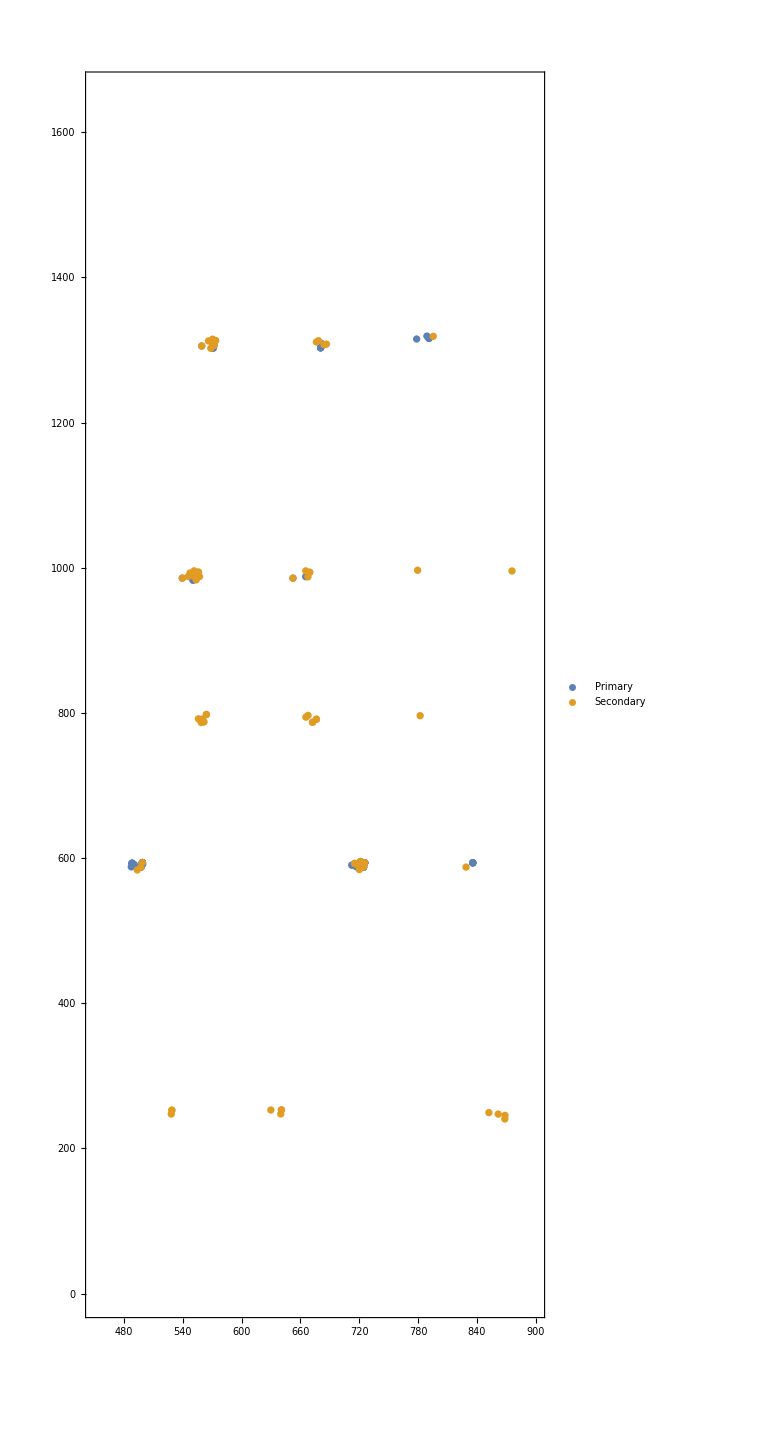

```mathematica
(* Distribution of CorrespondingPoints across CCD filters *)
ListPlot[{allPrimaryffCorrespondingPoints,allSecondaryffCorrespondingPoints},AspectRatio->Automatic,ImageSize->Large,PlotRange->{{450,900},{0,1650}},Frame->True
,PlotLegends->{"Primary","Secondary"}]
```

## Residuals (corresponding/control-point error) Evaluation

Residuals in pixels (from allControlPointsErrorPixels) are not re-projection errors (as in CERES bundle adjustment). Instead they are computed in function errorMetricForPair4[] as the chord distance between the primary and secondary corresponding points projected onto the target surface  divided by the mean of the distances from the spacecraft to the on-target points all divided by the camera angular pixel field of view parameter. This conversion from distance to pixels is performed to allow the values to be combined with limb fit error (which is a direct pixel measurement) when optimizing spacecraft position and timing offset parameters.

```mathematica
{controlPointsErrorPixels,limbFitErrorPixels}
```

{0.493425,0.308209}

```mathematica
limbFitResults[[All,{"meanOffsets","totalLimbPts"}]]
```

<|P41_01→<|meanOffsets→0.400151,totalLimbPts→76|>,P41_02→<|meanOffsets→0.338079,totalLimbPts→77|>,P41_03→<|meanOffsets→0.235665,totalLimbPts→78|>,P41_04→<|meanOffsets→0.262652,totalLimbPts→76|>,P41_05→<|meanOffsets→0.275718,totalLimbPts→81|>|>

```mathematica
stats[(residuals=sortedResiduals=Sort[allControlPointsErrorPixels](*⟦1;;-6-1⟧*))]
```

{0.794268,0.432523,1.40392,{0.0496544,9.50762},9.45797,65}

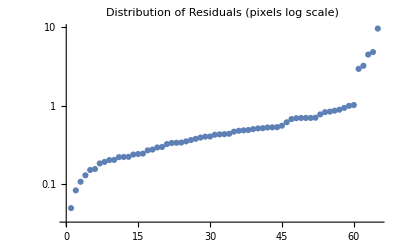

```mathematica
ListLogPlot[sortedResiduals,PlotRange->All
,PlotLabel->"Distribution of Residuals (pixels log scale)"]
```

```mathematica
largeResiduals=sortedResiduals⟦-1 Min[Round[ Length[sortedResiduals]],1000];;-1⟧;
```

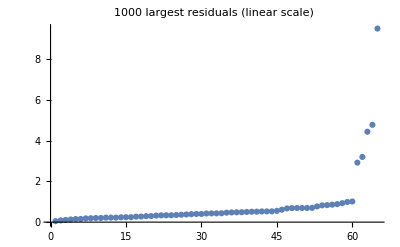

```mathematica
ListPlot[largeResiduals,PlotRange->All
,PlotLabel->"1000 largest residuals (linear scale)"]
```

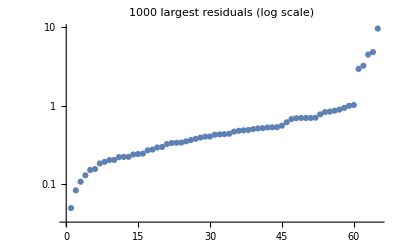

```mathematica
ListLogPlot[largeResiduals,PlotRange->All
,PlotLabel->"1000 largest residuals (log scale)"]
```

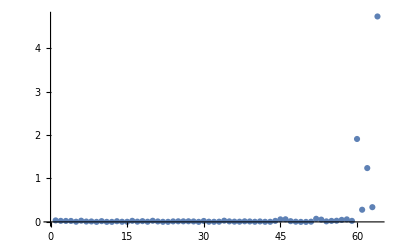

```mathematica
ListPlot[Differences[largeResiduals],PlotRange->All]
```

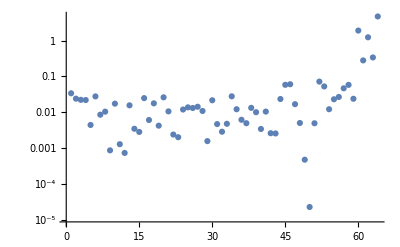

```mathematica
ListLogPlot[Differences[largeResiduals],PlotRange->All]
```

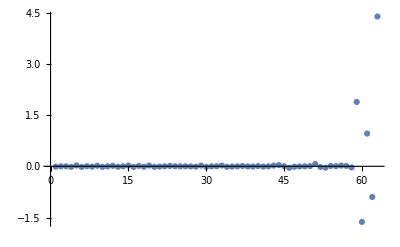

```mathematica
ListPlot[Differences[Differences[largeResiduals(*⟦1;;-20⟧*)]],PlotRange->All]
```

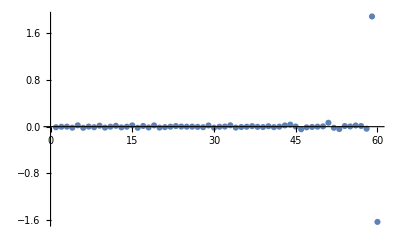

```mathematica
ListPlot[Differences[Differences[largeResiduals⟦1;;-3-1⟧]],PlotRange->All] (* discarding the largest 3 residual *)
```

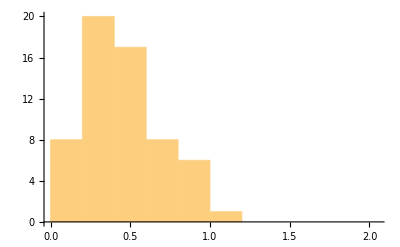

```mathematica
Histogram[sortedResiduals]
```

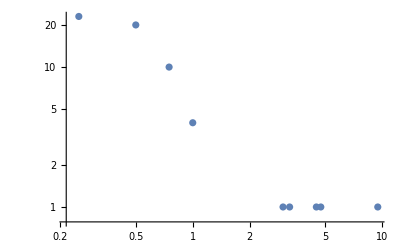

```mathematica
ListLogLogPlot[Tally[Round[sortedResiduals,0.25]]]
```

```mathematica
sortedResiduals⟦-50;;-1⟧ (* 50 largest residuals *)
```

{0.244441,0.269201,0.275258,0.292952,0.297163,0.323208,0.333755,0.336135,0.338139,0.350033,0.36371,0.376831,0.39104,0.401877,0.403436,0.425009,0.429669,0.432523,0.437275,0.46507,0.477184,0.483334,0.488267,0.501508,0.511514,0.514918,0.525325,0.527915,0.530466,0.553839,0.612142,0.67256,0.689323,0.694327,0.694799,0.694821,0.699737,0.771364,0.82388,0.836,0.858992,0.885714,0.93226,0.990332,1.0141,2.92235,3.20222,4.44084,4.77969,9.50762}

```mathematica
Select[sortedResiduals,#≥3.&]//Length
```

4

```mathematica
Select[sortedResiduals,#≥2.&]//Length
```

5

```mathematica
allPrimaryTargetXYZPoints=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"primaryTargetXYZ"⟧]],3];
```

```mathematica
allSecondaryTargetXYZPoints=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"secondaryTargetXYZ"⟧]],3];
```

```mathematica
allControlPointsErrorPixels//Dimensions
```

{65}

## Residual Outlier Distribution on Target (Ganymede)

#### Globe Display Support

```mathematica
textureWithOutlines=-Graphics-;(* PJ34 Ganymede *)
```

```mathematica
textureWithOutlines=-Graphics-;(* PJ41 Io *)
```

```mathematica
scStartPositionByDatatake=Map[(spkezra["JUNO_SPACECRAFT",#,"IAU_"<>target,"NONE"(*"CN+S"*),target])⟦1;;3⟧&,infoByDatatake⟦All,"adjustedStartTime"⟧]
```

<|P41_01→{-4628.67,-40650.6,100848.},P41_02→{15168.3,-22198.3,104944.},P41_03→{28406.6,-11296.9,107464.},P41_04→{42907.9,-519.92,110042.},P41_05→{72824.8,18330.,114817.}|>

```mathematica
initialViewpoint=scStartPositionByDatatake[[Round[Median[Range[5+0 Length[scStartPositionByDatatake]]]](* middle-ish*)]](*scStartPositionByDatatake["P34_03"]*)(* initial viewpoint set to the location of spacecraft at the start of the listed datatake *)
```

{28406.6,-11296.9,107464.}

#### Residuals in Pixels

```mathematica
allMpbdbdbpsfIndex=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"matchedPair","mpbdbdbpsfIndex"⟧]],3]; (* Indicies of all corresponding points used in errorMetricAssociations production (all non-thined/debisased/filtered) *)
```

```mathematica
Dimensions/@{allControlPointsErrorPixels,allMpbdbdbpsfIndex}
```

{{65},{65,4}}

```mathematica
outlierPixelPositions=Flatten[Position[allControlPointsErrorPixels,n_ /; n>1.(*2.0*)]];
```

```mathematica
outlierPixelPositions//Dimensions
```

{6}

```mathematica
(*allControlPointsErrorPixels[[outlierPixelPositions]]*)
```

```mathematica
outlierPixelLocationXYZPairs=({allPrimaryTargetXYZPoints,allSecondaryTargetXYZPoints}ᵀ)[[outlierPixelPositions]];(* List of primary/secondary pairs of XYZ points on target where pixel residual is large *)
```

```mathematica
body503radii={2631.2,2631.2,2631.2} (* Ganymede *);
```

```mathematica
(*Show[Graphics3D[Sphere[{0,0,0}, .98body503radii⟦1⟧]],(*ListPointPlot3D[{.99 allPrimaryTargetXYZPoints(*,allSecondaryTargetXYZPoints*)},PlotRange->All,ImageSize->Large]
,*)Graphics3D[{Thick,Red,Line[outlierPixelLocationXYZPairs]}],SphericalRegion->True]*)
```

```mathematica
bodyRadii=body503radii (* Ganymede *)
```

{2631.2,2631.2,2631.2}

```mathematica
body501radii={1829.4,1819.4,1815.7};
```

```mathematica
bodyRadii=body501radii (* Io *)
```

{1829.4,1819.4,1815.7}

```mathematica
backgroundSphere[]:=SphericalPlot3D[Norm[rayEllipsoidIntersection[{Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}, .98bodyRadii]],{θ,0,Pi},{ϕ, 0,2Pi}
, Mesh->None
,TextureCoordinateFunction->({#5,1-#4}&)
,PlotStyle->Directive[Specularity[White,10]
,Opacity[.75]
,Texture[textureWithOutlines]]
,Lighting->{"Ambient",White}(*"Neutral"*)
,Axes->False
,RotationAction->"Clip"
,PlotRange->(*2.5*)Max[bodyRadii]{{-1,1},{-1,1},{-1,1}}
(*,ImageSize->Large*)
,PerformanceGoal->"Quality"
(*,MaxRecursion->0*)
,PlotPoints->40 (* default geometry too coarse. Creates wiggles in background texture. *)
]
```

```mathematica
Show[{
backgroundSphere[]
,Graphics3D[{AbsoluteThickness[2.](*Thick*),Cyan,Line[outlierPixelLocationXYZPairs]}]
,ListPointPlot3D[
KeyValueMap[Tooltip[#2,#1]&,
scStartPositionByDatatake]
] (* plots spacecraft locations, but need to increase PlotRange to be visible *)
}
,SphericalRegion->True
(*,ViewAngle-> 15 Degree*)
,ViewPoint-> initialViewpoint
,ImageSize->72 7.75
,PlotLabel-> "Computed pixel offset >2.0 Outlier Locations (cyan)"
,PerformanceGoal->"Quality"
]
```

-Graphics3D-

Note: PDF version of above image many not exactly reproduced what is displayed in Mathematica’s interactive 3D view.

#### Residual in KM

```mathematica
Dimensions/@{allPrimaryTargetXYZPoints,allSecondaryTargetXYZPoints}
```

{{65,3},{65,3}}

```mathematica
sortedAllOnTargetDistances=Sort[allOnTargetDistances];
```

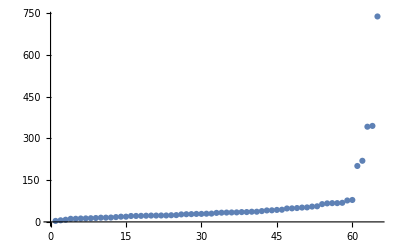

```mathematica
ListPlot[sortedAllOnTargetDistances,PlotRange->All]
```

```mathematica
sortedAllOnTargetDistances[[-50;;-1]]
```

{21.2012,21.4043,21.709,22.2132,22.7476,22.7616,23.0761,23.0901,23.8907,24.3834,26.9076,27.6214,27.9216,28.6698,28.7675,29.4539,29.8007,32.3387,33.1032,33.5329,33.8649,34.1448,35.2659,35.3501,36.5275,36.5512,38.8332,41.1264,41.5877,43.0047,43.7085,48.2048,48.5942,49.7643,51.4219,52.0662,55.0155,56.0242,63.8203,66.4733,67.3624,67.3988,68.5698,76.9033,78.7138,200.842,219.471,341.858,344.737,737.846}

```mathematica
outlierKMPositions=Flatten[Position[allOnTargetDistances,n_ /; n>2.0]];
```

```mathematica
outlierKMPositions//Dimensions
```

{65}

```mathematica
outlierKMLocationXYZPairs=({allPrimaryTargetXYZPoints,allSecondaryTargetXYZPoints}ᵀ)[[outlierKMPositions]];(* List of primary/secondary pairs of XYZ points on target where OnTargetDistances (km) residual is large *)
```

```mathematica
outlierKMLocationXYZPairs//Dimensions
```

{65,2,3}

```mathematica
Show[{
backgroundSphere[]
,Graphics3D[{Thick,Cyan,Line[outlierKMLocationXYZPairs]}]
,ListPointPlot3D[
KeyValueMap[Tooltip[#2,#1]&,
scStartPositionByDatatake]
] (* plots spacecraft locations, but need to increase PlotRange to be visible *)
}
,SphericalRegion->True
(*,ViewAngle-> 15 Degree*)
,ViewPoint-> initialViewpoint
,ImageSize->72 7.75
,PlotLabel-> "On target chord distance >2.0 km Outlier Locations (cyan)"
,PerformanceGoal->"Quality"
]
```

-Graphics3D-

Note: PDF version of above image many not exactly reproduced what is displayed in Mathematica’s interactive 3D view.

```mathematica
(*Show[Graphics3D[Sphere[{0,0,0}, .98body503radii⟦1⟧]],(*ListPointPlot3D[{.99 allPrimaryTargetXYZPoints(*,allSecondaryTargetXYZPoints*)},PlotRange->All,ImageSize->Large]
,*)Graphics3D[{Thick,Red,Line[outlierKMLocationXYZPairs]}],SphericalRegion->True]*)
```

## Outlier Distribution across CCD

```mathematica
(* Distribution of outliers across CCD filters *)
ListPlot[{allPrimaryffCorrespondingPoints[[outlierPixelPositions]],allSecondaryffCorrespondingPoints[[outlierPixelPositions]]},AspectRatio->Automatic,ImageSize->Large,PlotRange->{{450,900},{0,1650}},Frame->True
,PlotLayout->"Row"]
```

-Graphics-

### Linked Outlier on CCD Investigation

Observations:
Outliers occurring near edge of CCD (which is where distortion is greatest)

```mathematica
outlierPixelPositions=Flatten[Position[allControlPointsErrorPixels,n_ /; n>0.5(*3.0*)]];
```

```mathematica
outlierPixelPositions//Dimensions
```

{27}

```mathematica
outlierPixelLocationFFPairs=({allPrimaryffCorrespondingPoints,allSecondaryffCorrespondingPoints}ᵀ)[[outlierPixelPositions]];
```

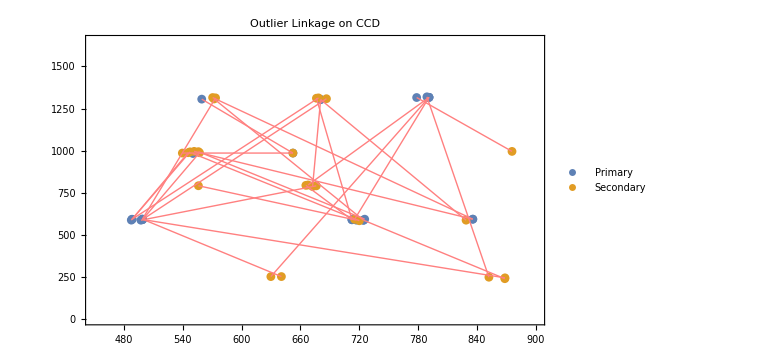

```mathematica
(* Distribution of CorrespondingPoints across CCD filters *)
Show[{ListPlot[{allPrimaryffCorrespondingPoints⟦outlierPixelPositions⟧,allSecondaryffCorrespondingPoints⟦outlierPixelPositions⟧}
(*,AspectRatio->Automatic*)
,PlotRange->{{450,900},{0,1650}}
,ImageSize->Large
,Frame->True
,PlotLegends->{"Primary","Secondary"}
,PlotLabel->"Outlier Linkage on CCD"
]
,Graphics[{Pink,Line[outlierPixelLocationFFPairs]}]
}
]
```

```mathematica
outlierPairMaxY=Map[Max[#⟦{1,2},2⟧]&,outlierPixelLocationFFPairs];
```

```mathematica
stats[outlierPairMaxY]
```

{1090.31,1303.14,260.966,{587.456,1319.18},731.722,27}

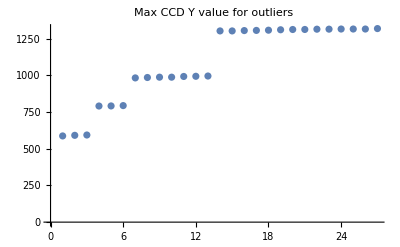

```mathematica
ListPlot[Sort@outlierPairMaxY
,PlotLabel->"Max CCD Y value for outliers"]
```

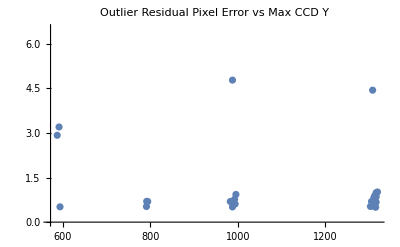

```mathematica
ListPlot[{outlierPairMaxY,allControlPointsErrorPixels⟦outlierPixelPositions⟧}ᵀ
,PlotLabel-> "Outlier Residual Pixel Error vs Max CCD Y"]
```

## Residual vs Emission Angle Distribution

```mathematica
errorMetricAssociations⟦2,1,1⟧//Keys
```

{primaryTargetXYZ,secondaryTargetXYZ,scToPrimaryVec,scToSecondaryVec,primaryScPosition,secondaryScPosition,onTargetDistances,scToPrimaryDistances,scToSecondaryDistances,scTargetMeanDistances,controlPointsErrorPixels,matchedPair,keys,primaryScToTargetMat,secondaryScToTargetMat,primaryEmissionAngle,secondaryEmissionAngle}

```mathematica
allPrimaryEmissionAngles=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"primaryEmissionAngle"⟧]],3];
```

```mathematica
allSecondaryEmissionAngles=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"secondaryEmissionAngle"⟧]],3];
```

```mathematica
allPrimaryEmissionAngles//Dimensions
```

{65}

```mathematica
allSecondaryEmissionAngles//Dimensions
```

{65}

```mathematica
MinMax[allPrimaryEmissionAngles]/Degree
```

{8.17868,49.7387}

```mathematica
MinMax[allSecondaryEmissionAngles]/Degree
```

{14.146,61.1734}

```mathematica
outlierPairsAndEmissionAngles=Select[{allPrimaryTargetXYZPoints,allSecondaryTargetXYZPoints,allPrimaryEmissionAngles,allSecondaryEmissionAngles,allControlPointsErrorPixels}ᵀ,Norm[#⟦1⟧-#⟦2⟧]>0.(*2.0*)&];
```

```mathematica
outlierPairsAndEmissionAngles//Dimensions
```

{65,5}

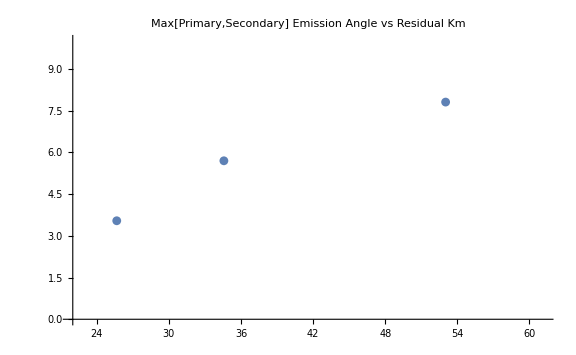

```mathematica
ListPlot[{Max/@outlierPairsAndEmissionAngles[[All,{3,4}]]/Degree,Norm/@(outlierPairsAndEmissionAngles⟦All,1⟧-outlierPairsAndEmissionAngles⟦All,2⟧)
}ᵀ
,PlotLabel->"Max[Primary,Secondary] Emission Angle vs Residual Km"
,PlotRange->{0,10}
,ImageSize->Large]
```

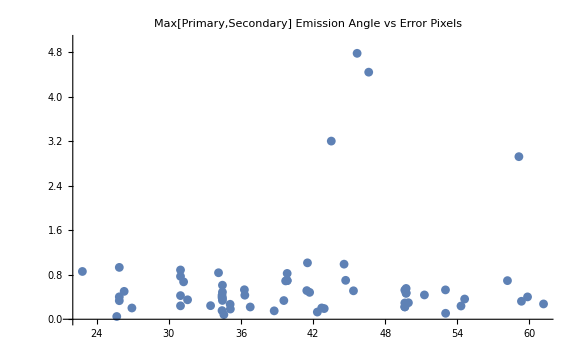

```mathematica
ListPlot[{Max/@outlierPairsAndEmissionAngles[[All,{3,4}]]/Degree,allControlPointsErrorPixels
}ᵀ
,PlotLabel->"Max[Primary,Secondary] Emission Angle vs Error Pixels"
,PlotRange->{0,5}
,ImageSize->Large]
```

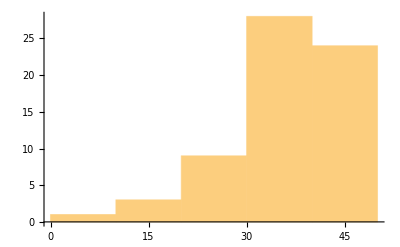

```mathematica
Histogram[allPrimaryEmissionAngles/Degree]
```

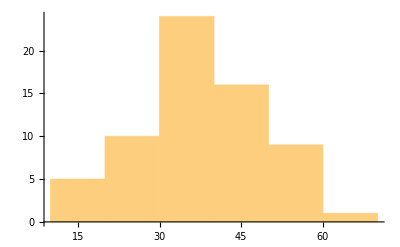

```mathematica
Histogram[allSecondaryEmissionAngles/Degree]
```

## Outlier Chip-level Review

```mathematica
(* Create Associations to allow residual values to be looked up for corresponding points in chips.
Needed because corresponding points by chip are merged by segment (framelet) prior to residual calculations. *)
indexToErrorPixels=AssociationThread[allMpbdbdbpsfIndex-> allControlPointsErrorPixels];
indexToOnTargetDistance=AssociationThread[allMpbdbdbpsfIndex-> allOnTargetDistances];
indexToPrimaryEmissionAngle=AssociationThread[allMpbdbdbpsfIndex-> allPrimaryEmissionAngles];
indexToSecondaryEmissionAngles=AssociationThread[allMpbdbdbpsfIndex-> allSecondaryEmissionAngles];
```

### Review Chips based on correspondingPointCount (not outliers for PJ41 Io )

```mathematica
matchedPairsKeptKeys=DeleteDuplicates[Flatten[
Values[Values[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat⟦All,All,All,"mpbdbdbpsfIndex",All,1;;-2⟧]],3]];
```

```mathematica
matchedPairsKeptList=Extract[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,matchedPairsKeptKeys];
```

```mathematica
matchedPairsKeptKeys//Length
```

54

```mathematica
keyedCorrespondingPointCount=Map[{#1⟦"mpbdbdbpsfIndex",1,1;;-2⟧ (* key to lookup chip pair *)
,#1⟦"correspondingPointCount"⟧ (* max distance between primary and secondary corresponding points *)
}&
,matchedPairsKeptList];
```

```mathematica
selectedKeyedCorrespondingPointCount=Select[keyedCorrespondingPointCount,#[[2]]>1&];
```

```mathematica
Counts[selectedKeyedCorrespondingPointCount⟦All,2⟧]
```

<|2→11|>

```mathematica
selectedKeyedCorrespondingPointCountKeys=DeleteDuplicates[selectedKeyedCorrespondingPointCount⟦All,1⟧]
```

{{Key[P41_02],Key[P41_01],11},{Key[P41_02],Key[P41_01],12},{Key[P41_02],Key[P41_02],14},{Key[P41_02],Key[P41_02],17},{Key[P41_02],Key[P41_04],9},{Key[P41_02],Key[P41_04],12},{Key[P41_02],Key[P41_04],15},{Key[P41_02],Key[P41_05],12},{Key[P41_02],Key[P41_05],17},{Key[P41_02],Key[P41_05],18},{Key[P41_05],Key[P41_05],12}}

```mathematica
Column[Map[reviewOutlierChip,selectedKeyedCorrespondingPointCountKeys⟦1;;UpTo[4(*15*)]⟧]]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
2.75655
1.8689.dx
-2.50677
-0.725361.dy
1.14658
1.72239 Residuals
    idx
1
2.pix
0.323208
0.483334.km
22.2132
33.1032 Emission Angles
    idx
1
2.primar
49.7387
34.4564.secon
59.335
41.7096
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
3.0895
2.64131.dx
-3.04313
-2.40757.dy
0.533314
1.08634 Residuals
    idx
1
2.pix
0.401877
0.203259.km
27.6214
13.9223 Emission Angles
    idx
1
2.primar
49.7387
34.4564.secon
59.8414
42.7154
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
1.77803
0.999945.dx
-1.73146
-0.964729.dy
-0.404261
-0.263035 Residuals
    idx
1
2.pix
0.350033
0.183501.km
23.8907
12.5319 Emission Angles
    idx
1
2.primar
30.9673
34.8761.secon
31.5547
35.114
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
0.526913
0.997137.dx
-0.189862
-0.905029.dy
-0.491518
0.418573 Residuals
    idx
1
2.pix
0.222614
0.0834165.km
15.2469
5.6964 Emission Angles
    idx
1
2.primar
49.6305
34.4227.secon
49.5831
34.5762

### Review Chips with Large Residuals (in pixels)

```mathematica
outlierPositionsInAllControlPointsErrorPixels=Reverse[Ordering[allControlPointsErrorPixels,-15]]
```

{53,31,40,7,2,50,51,24,39,56,60,35,29,18,62}

```mathematica
Dimensions/@{allControlPointsErrorPixels,allMpbdbdbpsfIndex}
```

{{65},{65,4}}

```mathematica
Part[allControlPointsErrorPixels,outlierPositionsInAllControlPointsErrorPixels](* Should be residual values decreasing from largest  *)
```

{9.50762,4.77969,4.44084,3.20222,2.92235,1.0141,0.990332,0.93226,0.885714,0.858992,0.836,0.82388,0.771364,0.699737,0.694821}

```mathematica
outlierMPBDBDBPSFKeysWithDups=Part[allMpbdbdbpsfIndex,outlierPositionsInAllControlPointsErrorPixels][[All,1;;3]](* matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat (chip pair) Keys corresponding to above outliers *)
```

{{Key[P41_05],Key[P41_02],7},{Key[P41_02],Key[P41_04],15},{Key[P41_02],Key[P41_05],17},{Key[P41_02],Key[P41_01],16},{Key[P41_02],Key[P41_01],10},{Key[P41_05],Key[P41_01],3},{Key[P41_05],Key[P41_01],4},{Key[P41_02],Key[P41_04],5},{Key[P41_02],Key[P41_05],14},{Key[P41_05],Key[P41_03],4},{Key[P41_05],Key[P41_04],1},{Key[P41_02],Key[P41_05],8},{Key[P41_02],Key[P41_04],12},{Key[P41_02],Key[P41_03],9},{Key[P41_05],Key[P41_04],11}}

```mathematica
pixelOutlierMPBDBDBPSFKeys=DeleteDuplicates[outlierMPBDBDBPSFKeysWithDups] (* Eliminate chip key duplicates, cases where more than one of the largest outliers is in the same chip pair *)
```

{{Key[P41_05],Key[P41_02],7},{Key[P41_02],Key[P41_04],15},{Key[P41_02],Key[P41_05],17},{Key[P41_02],Key[P41_01],16},{Key[P41_02],Key[P41_01],10},{Key[P41_05],Key[P41_01],3},{Key[P41_05],Key[P41_01],4},{Key[P41_02],Key[P41_04],5},{Key[P41_02],Key[P41_05],14},{Key[P41_05],Key[P41_03],4},{Key[P41_05],Key[P41_04],1},{Key[P41_02],Key[P41_05],8},{Key[P41_02],Key[P41_04],12},{Key[P41_02],Key[P41_03],9},{Key[P41_05],Key[P41_04],11}}

```mathematica
Dimensions/@{outlierMPBDBDBPSFKeysWithDups,pixelOutlierMPBDBDBPSFKeys}
```

{{15,3},{15,3}}

```mathematica
(*Map[showMatchesXForKeys,pixelOutlierMPBDBDBPSFKeys]*)
```

```mathematica
(* Review a single chip pair *)(*reviewOutlierChip[pixelOutlierMPBDBDBPSFKeys⟦2(* change this values to change which chip containing outliers is viewed below *)⟧]*)
```

```mathematica
Column[Map[reviewOutlierChip,pixelOutlierMPBDBDBPSFKeys⟦1;;7⟧]]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
31.0959.dx
26.1609.dy
16.8096 Residuals
    idx
1.pix
9.50762.km
737.846 Emission Angles
    idx
1.primar
42.3505.secon
41.4114
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
14.012
2.95794.dx
-11.2313
2.6829.dy
-8.37812
-1.24557 Residuals
    idx
1
2.pix
4.77969
0.39104.km
341.858
27.9216 Emission Angles
    idx
1
2.primar
40.0326
34.4227.secon
45.6612
31.9375
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
13.7717
2.13084.dx
-11.1061
2.12315.dy
-8.14336
-0.180853 Residuals
    idx
1
2.pix
4.44084
0.221885.km
344.737
17.2292 Emission Angles
    idx
1
2.primar
40.0326
49.6305.secon
46.6264
39.8007
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
10.0358.dx
8.60136.dy
-5.17056 Residuals
    idx
1.pix
3.20222.km
219.471 Emission Angles
    idx
1.primar
40.0326.secon
43.5126
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
9.87827.dx
0.63705.dy
-9.85771 Residuals
    idx
1.pix
2.92235.km
200.842 Emission Angles
    idx
1.primar
49.7387.secon
59.1228
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
7.71712.dx
-4.72752.dy
6.09955 Residuals
    idx
1.pix
1.0141.km
78.7138 Emission Angles
    idx
1.primar
8.17868.secon
41.5309
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
5.07263.dx
-2.56173.dy
4.37826 Residuals
    idx
1.pix
0.990332.km
76.9033 Emission Angles
    idx
1.primar
15.4851.secon
44.5759

### Review chips with Large Corresponding Points Shifts

Identify and review chips with largest distance shift of corresponding points between primary and morphed secondary chips. This is different from the “residuals” metrics which are computed from differences in locations on target.
A number of the largest shifts are associated with chips at the edge of the frame. Not sure yet if this is due to errors in my camera model, or issue with imaging geometry (target position, spacecraft position and pointing).

```mathematica
matchedPairsKeptKeys=DeleteDuplicates[Flatten[
Values[Values[debiasedSegmentPairsCorrespondingPointsMulti⟦All,All,All,"mpbdbdbpsfIndex",All,1;;-2⟧]],3]];
(* matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat has all chip pairs including ones without control points or too few control points to be kept or get filtered out through debiasing. 
So this line extracts all the "mpbdbdbpsfIndex" from debiasedSegmentPairsCorrespondingPointsMulti which is final set of control points. *)
```

```mathematica
matchedPairsKeptList=Extract[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,matchedPairsKeptKeys];
```

```mathematica
matchedPairsKeptList//Dimensions
```

{54}

```mathematica
(*maxControlPointShiftsAssoc=MapIndexed[If[#["correspondingPointCount"]<1
,Nothing
,{#2,Max[Norm/@Subtract@@#1⟦"cPts"⟧]}
]&
,matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,{3}];
keyedMaxControlPointShifts=Flatten[Values[Values[maxControlPointShiftsAssoc]],2];*)
```

```mathematica
keyedMaxControlPointShifts=Map[{#1⟦"mpbdbdbpsfIndex",1,1;;-2⟧ (* key to lookup chip pair *)
,Max[Norm/@Subtract@@#1⟦"cPts"⟧] (* max distance between primary and secondary corresponding points *)
}&
,matchedPairsKeptList];
```

```mathematica
keyedMaxControlPointShifts//Dimensions
```

{54,2}

```mathematica
outlierKeyedMaxControlPointShifts=MaximalBy[keyedMaxControlPointShifts,#⟦2⟧&,10] (* largest shifts *)
```

{{{Key[P41_05],Key[P41_02],7},31.0959},{{Key[P41_02],Key[P41_04],15},14.012},{{Key[P41_02],Key[P41_05],17},13.7717},{{Key[P41_02],Key[P41_01],16},10.0358},{{Key[P41_02],Key[P41_01],10},9.87827},{{Key[P41_05],Key[P41_01],3},7.71712},{{Key[P41_05],Key[P41_02],15},6.41115},{{Key[P41_05],Key[P41_02],9},5.93741},{{Key[P41_02],Key[P41_05],8},5.33604},{{Key[P41_05],Key[P41_01],4},5.07263}}

```mathematica
cPtsOutlierMPBDBDBPSFKeys=DeleteDuplicates[outlierKeyedMaxControlPointShifts⟦All,1⟧](* Probably not possible to have duplicates here, but will mimic pixel outlier process. *)
```

{{Key[P41_05],Key[P41_02],7},{Key[P41_02],Key[P41_04],15},{Key[P41_02],Key[P41_05],17},{Key[P41_02],Key[P41_01],16},{Key[P41_02],Key[P41_01],10},{Key[P41_05],Key[P41_01],3},{Key[P41_05],Key[P41_02],15},{Key[P41_05],Key[P41_02],9},{Key[P41_02],Key[P41_05],8},{Key[P41_05],Key[P41_01],4}}

```mathematica
Dimensions/@{outlierKeyedMaxControlPointShifts,cPtsOutlierMPBDBDBPSFKeys}
```

{{10,2},{10,3}}

```mathematica
(* Review single pair *)(*reviewOutlierChip[cPtsOutlierMPBDBDBPSFKeys⟦1(* change this values to change which chip containing outliers is viewed below *)⟧]*)
```

```mathematica
Column[Map[reviewOutlierChip,cPtsOutlierMPBDBDBPSFKeys⟦1;;5⟧]]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
31.0959.dx
26.1609.dy
16.8096 Residuals
    idx
1.pix
9.50762.km
737.846 Emission Angles
    idx
1.primar
42.3505.secon
41.4114
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
14.012
2.95794.dx
-11.2313
2.6829.dy
-8.37812
-1.24557 Residuals
    idx
1
2.pix
4.77969
0.39104.km
341.858
27.9216 Emission Angles
    idx
1
2.primar
40.0326
34.4227.secon
45.6612
31.9375
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
13.7717
2.13084.dx
-11.1061
2.12315.dy
-8.14336
-0.180853 Residuals
    idx
1
2.pix
4.44084
0.221885.km
344.737
17.2292 Emission Angles
    idx
1
2.primar
40.0326
49.6305.secon
46.6264
39.8007
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
10.0358.dx
8.60136.dy
-5.17056 Residuals
    idx
1.pix
3.20222.km
219.471 Emission Angles
    idx
1.primar
40.0326.secon
43.5126
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
9.87827.dx
0.63705.dy
-9.85771 Residuals
    idx
1.pix
2.92235.km
200.842 Emission Angles
    idx
1.primar
49.7387.secon
59.1228

### Review Chips with Elongated Secondary Polygons

```mathematica
unsquareness[polygonPoints_]:=(Times@@Flatten[Differences/@RegionBounds[#]]/Area[#])&@Polygon[polygonPoints](* Ratio of area of bounding box to area of polygon. Since polygon area is less than bound area, value increases as polygon becomes less square. *)
```

```mathematica
keyedSecondaryChipUnsquareness=Map[{#1⟦"mpbdbdbpsfIndex",1,1;;-2⟧ (* key to lookup chip pair *)
,unsquareness[#1⟦"chip2","secondaryCorners"⟧] 
}&
,matchedPairsKeptList];
```

```mathematica
keyedSecondaryChipUnsquareness⟦1⟧
```

{{Key[P41_02],Key[P41_01],4},1.15088}

```mathematica
sortedKeyedSecondaryChipUnsquareness=SortBy[keyedSecondaryChipUnsquareness,#⟦2⟧&];
```

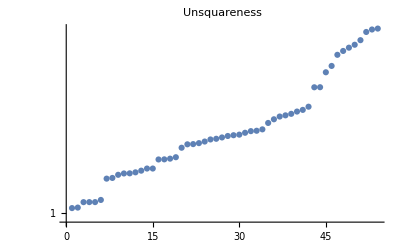

```mathematica
ListLogPlot[sortedKeyedSecondaryChipUnsquareness⟦All,2⟧,PlotRange->All,PlotLabel->"Unsquareness"]
```

```mathematica
outlierKeyedSecondaryChipUnsquareness=MaximalBy[keyedSecondaryChipUnsquareness,#⟦2⟧&,5] (* largest Unsquareness *)
```

{{{Key[P41_05],Key[P41_02],15},1.39525},{{Key[P41_05],Key[P41_01],3},1.39291},{{Key[P41_02],Key[P41_05],18},1.38671},{{Key[P41_02],Key[P41_05],17},1.36634},{{Key[P41_05],Key[P41_02],7},1.35511}}

```mathematica
chipReviewsUnsquareness=Map[reviewOutlierChip,outlierKeyedSecondaryChipUnsquareness⟦All(* change this values to change which chip containing outliers is viewed below *),1⟧];
```

```mathematica
Column[chipReviewsUnsquareness]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
6.41115.dx
-5.89149.dy
2.52849 Residuals
    idx
1.pix
0.297163.km
23.0761 Emission Angles
    idx
1.primar
39.9067.secon
49.9288
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
7.71712.dx
-4.72752.dy
6.09955 Residuals
    idx
1.pix
1.0141.km
78.7138 Emission Angles
    idx
1.primar
8.17868.secon
41.5309
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
3.17488
2.68076.dx
3.04053
2.68003.dy
0.913786
-0.0624752 Residuals
    idx
1
2.pix
0.530466
0.292952.km
41.1264
22.7476 Emission Angles
    idx
1
2.primar
34.4227
49.6305.secon
36.2829
39.4992
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
13.7717
2.13084.dx
-11.1061
2.12315.dy
-8.14336
-0.180853 Residuals
    idx
1
2.pix
4.44084
0.221885.km
344.737
17.2292 Emission Angles
    idx
1
2.primar
40.0326
49.6305.secon
46.6264
39.8007
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
31.0959.dx
26.1609.dy
16.8096 Residuals
    idx
1.pix
9.50762.km
737.846 Emission Angles
    idx
1.primar
42.3505.secon
41.4114

### Review Wide, Narrow, Short, Tall Secondary Chips

```mathematica
polyPointsWidthHeight[polygonPoints_]:=Flatten[Differences/@RegionBounds[Polygon[polygonPoints]]](* returns widht and height of axis aligned bounding box of list of points *)
```

```mathematica
keyedChipDims=Map[{#1⟦"mpbdbdbpsfIndex",1,1;;-2⟧ (* key to lookup chip pair *)
,{polyPointsWidthHeight[#1⟦"chip1","primaryCorners"⟧] ,polyPointsWidthHeight[#1⟦"chip2","secondaryCorners"⟧]}
}&
,matchedPairsKeptList]; (* Returns {{primary width,primary height},{secondary width, secondary height}} *)
```

```mathematica
keyedChipDims⟦1⟧
```

{{Key[P41_02],Key[P41_01],4},{{13.,11.},{12.9533,12.0968}}}

```mathematica
keyedChipDims//Dimensions
```

{54,2}

#### Chip Dimension (width and height) Distribution

```mathematica
chipDimsSorted=Sort/@Transpose[(Flatten/@keyedChipDims⟦All,2⟧)];
```

```mathematica
chipDimsSorted//Dimensions
```

{4,54}

```mathematica
MinMax/@chipDimsSorted
```

{{13.,13.},{11.,11.},{10.7961,16.6111},{8.66537,19.0848}}

```mathematica
ListPlot[chipDimsSorted,PlotRange->All,PlotLabel->"Chip Dimension",ImageSize->Large,PlotLabels->{"Primary Width","Primary Height","Secondary Width","Secondary Height"}]
```

-Graphics-

```mathematica
outlierKeyedSecondaryChipWidest=MaximalBy[keyedChipDims,#⟦2,2,1⟧&,2] (* Widest  *)
```

{{{Key[P41_02],Key[P41_05],18},{{13.,11.},{16.6111,8.71793}}},{{Key[P41_02],Key[P41_05],17},{{13.,11.},{16.5349,8.66537}}}}

```mathematica
outlierKeyedSecondaryChipNarrowest=MinimalBy[keyedChipDims,#⟦2,2,1⟧&,2] (* Narrowest  *)
```

{{{Key[P41_05],Key[P41_02],9},{{13.,11.},{10.7961,18.5294}}},{{Key[P41_05],Key[P41_02],7},{{13.,11.},{10.9824,18.6787}}}}

```mathematica
outlierKeyedSecondaryChipTallest=MaximalBy[keyedChipDims,#⟦2,2,2⟧&,2] (* Tallest  *)
```

{{{Key[P41_05],Key[P41_02],15},{{13.,11.},{11.728,19.0848}}},{{Key[P41_05],Key[P41_02],7},{{13.,11.},{10.9824,18.6787}}}}

```mathematica
outlierKeyedSecondaryChipShortest=MinimalBy[keyedChipDims,#⟦2,2,2⟧&,2] (* Tallest  *)
```

{{{Key[P41_02],Key[P41_05],17},{{13.,11.},{16.5349,8.66537}}},{{Key[P41_02],Key[P41_05],10},{{13.,11.},{15.8469,8.66665}}}}

```mathematica
(*reviewOutlierChip/@Flatten[{outlierKeyedSecondaryChipWidest,outlierKeyedSecondaryChipNarrowest,outlierKeyedSecondaryChipTallest,outlierKeyedSecondaryChipShortest},1]⟦All,1⟧*)
```

#### Widest Secondary Chips

```mathematica
Column[Map[reviewOutlierChip,outlierKeyedSecondaryChipWidest⟦1;;2,1⟧]]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
3.17488
2.68076.dx
3.04053
2.68003.dy
0.913786
-0.0624752 Residuals
    idx
1
2.pix
0.530466
0.292952.km
41.1264
22.7476 Emission Angles
    idx
1
2.primar
34.4227
49.6305.secon
36.2829
39.4992
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
13.7717
2.13084.dx
-11.1061
2.12315.dy
-8.14336
-0.180853 Residuals
    idx
1
2.pix
4.44084
0.221885.km
344.737
17.2292 Emission Angles
    idx
1
2.primar
40.0326
49.6305.secon
46.6264
39.8007

#### Narrowest Secondary Chips

```mathematica
Column[Map[reviewOutlierChip,outlierKeyedSecondaryChipNarrowest⟦1;;2,1⟧]]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
5.93741.dx
-5.64568.dy
1.83826 Residuals
    idx
1.pix
0.275258.km
21.4043 Emission Angles
    idx
1.primar
42.3505.secon
61.1734
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
31.0959.dx
26.1609.dy
16.8096 Residuals
    idx
1.pix
9.50762.km
737.846 Emission Angles
    idx
1.primar
42.3505.secon
41.4114

#### Tallest Secondary Chips

```mathematica
Column[Map[reviewOutlierChip,outlierKeyedSecondaryChipTallest⟦1;;2,1⟧]]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
6.41115.dx
-5.89149.dy
2.52849 Residuals
    idx
1.pix
0.297163.km
23.0761 Emission Angles
    idx
1.primar
39.9067.secon
49.9288
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
31.0959.dx
26.1609.dy
16.8096 Residuals
    idx
1.pix
9.50762.km
737.846 Emission Angles
    idx
1.primar
42.3505.secon
41.4114

#### Shortest Secondary Chips

```mathematica
Column[Map[reviewOutlierChip,outlierKeyedSecondaryChipShortest⟦1;;2,1⟧]]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1
2.norm
13.7717
2.13084.dx
-11.1061
2.12315.dy
-8.14336
-0.180853 Residuals
    idx
1
2.pix
4.44084
0.221885.km
344.737
17.2292 Emission Angles
    idx
1
2.primar
40.0326
49.6305.secon
46.6264
39.8007
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
cPts shifts
    idx
1.norm
0.344576.dx
0.327099.dy
0.108345 Residuals
    idx
1.pix
0.202398.km
15.6719 Emission Angles
    idx
1.primar
25.662.secon
26.9229

## Corresponding Points Per Chip Distribution Review

```mathematica
allCorrespondingPointCounts=Flatten[Values[Values[matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat⟦All,All,All,"correspondingPointCount"⟧]]];
```

```mathematica
Histogram[allCorrespondingPointCounts]
```

-Graphics-

```mathematica
finalCorrespondingPointCounts=Flatten[Values[Values[
Map[
Count[(indexToErrorPixels/@#["mpbdbdbpsfIndex"]),_?NumberQ]&,matchedPairsByDatatakeByDatatakeByPrimarySegmentFlat,{3}]
]]]; (* per chip counts of Corresponding Points not filtered/debiasesd *)
```

```mathematica
Histogram[finalCorrespondingPointCounts]
```

-Graphics-

```mathematica
KeySort[Merge[{Counts[allCorrespondingPointCounts],Counts[finalCorrespondingPointCounts]},{1. #⟦2⟧/#⟦1⟧,#}&]]
```

<|0→{1.,{165,165}},1→{1.,{43,43}},2→{1.,{11,11}}|>

Most (93%) of cells starting with 15 corresponding points and many (61%) of cells with 14 corresponding points are reduced due to reduction by correspondingPointDistanceFilter[]. This increases the the counts of cells with with fewer corresponding points. Note, all the cells with counts 1 to 4 are the result of reduction in cells with 5 or more corresponding points, because all cell with less than 5 corresponding points are de-selected.

```mathematica
KeySort@Counts[{allCorrespondingPointCounts,finalCorrespondingPointCounts}ᵀ]
```

<|{0,0}→165,{1,1}→43,{2,2}→11|>

```mathematica
shiftedFromToCounts=KeySort@Counts[{1,1}+#&/@({allCorrespondingPointCounts,finalCorrespondingPointCounts}ᵀ)](* add one to convert counts to column/row position in table below (also SparseArray can't be indexed from 0) *)
```

<|{1,1}→165,{2,2}→43,{3,3}→11|>

```mathematica
shiftedFromToCountsSA=SparseArray[Normal@shiftedFromToCounts,Automatic,"."]
```

SparseArray[…]

```mathematica
sa//Dimensions
```

{}

```mathematica
columnLabels=-1+Range[Dimensions[shiftedFromToCountsSA]⟦2⟧]
```

{0,1,2}

```mathematica
Grid[Reverse[{{a,b,c},{d,e,f}},2]]
```

c | b | a
f | e | d

```mathematica
shiftedFromToCountsWithColumnLabels=Join[{columnLabels},Normal[shiftedFromToCountsSA]];
```

```mathematica
rowLabels=Join[{" "},-1+Range[Dimensions[shiftedFromToCountsSA]⟦1⟧]]
```

{ ,0,1,2}

```mathematica
shiftedFromToCountsWithRowColumnLabels=MapThread[Join[{#1},#2]&,{rowLabels,Reverse[shiftedFromToCountsWithColumnLabels,2]}];
```

```mathematica
correspondingPointsPerChipGrid=Grid[{{"Table values
are Chip counts","To Corresponding Points
(after de-selection and neighbor thinning)"}
,{"Fom
Corresponding
Points",Grid[shiftedFromToCountsWithRowColumnLabels]}
,{" ","Chips with less than "<>ToString[correspondingPointCountThreshold]<>" initial corresponding points are not used,
so they all map to 0.
Example: Of chips that initially had 12 corresponding points,
  "<>ToString[shiftedFromToCountsWithRowColumnLabels⟦14,5⟧]<>" remained unchanged after thinning,
    "<>ToString[shiftedFromToCountsWithRowColumnLabels⟦14,14⟧]<>" were reduceed to only 3 corresponding points." }
},Frame->True
,ItemSize->Full
];
```

Part::partw: Part 14 of {{ ,2,1,0},{0,.,.,165},{1,.,43,.},{2,11,.,.}} does not exist.

```mathematica
Style[correspondingPointsPerChipGrid,11](* to print without clipping *)
```

Table values
are Chip counts | To Corresponding Points
(after de-selection and neighbor thinning)
Fom
Corresponding
Points |   | 2 | 1 | 0
0 | . | . | 165
1 | . | 43 | .
2 | 11 | . | .
  | Chips with less than 1 initial corresponding points are not used,
so they all map to 0.
Example: Of chips that initially had 12 corresponding points,
  {{ , 2, 1, 0}, {0, ., ., 165}, {1, ., 43, .}, {2, 11, ., .}}[[14,5]] remained unchanged after thinning,
    {{ , 2, 1, 0}, {0, ., ., 165}, {1, ., 43, .}, {2, 11, ., .}}[[14,14]] were reduceed to only 3 corresponding points.

## USGS ISIS Control Network Export

### Notes

Looks like this needs
	infoByDatatake (* produced by keypointsDevO.nb initial Dev sections through “Load Dev” *)
	metaDataByRawFilename (* produced by Juno3Dpj34gany.nb setup*)
	errorMetricAssociations (* produced by keypointsDevO.nb evaluation of spread20RMSWeightedXYSumNoLimb@@... at “RUN THIS ONE” *)

### Evaluate ffCorrespondingPoints ranges to develop mapping to ISIS line/sample function ffToLineSample

```mathematica
filterOffsets (* I've treated these as relative to 1214 high CCD, not 1200 high. *)
```

```mathematica
(*all the ffCorrespondingPoints. Don't completely span ranges of filters because matching doesen't occur on very edges of filters *)(tff=Flatten[Values[Values[errorMetricAssociations⟦All,All,All,"matchedPair","ffCorrespondingPoints",{1,2}⟧]],4])//Dimensions (* 2x because both Primary and Secondary *)
```

```mathematica
MinMax[tff⟦All,2⟧] (* range of ff-y values *)
```

```mathematica
MinMax[tff⟦All,1⟧](* range of ff-x values *)
```

```mathematica
MinMax[Select[tff⟦All,1⟧,#<600&]]-14 (* range of ff-x for first/red filter adjusted by ISIS offset of 14 *)
```

```mathematica
MinMax[Select[tff⟦All,1⟧,750>#>600&]]-14(* range of ff-x for first/green filter adjusted by ISIS offset of 14 *)
```

```mathematica
MinMax[Select[tff⟦All,1⟧,#>750&]]-14(* range of ff-x for first/blue filter adjusted by ISIS offset of 14 *)
```

```mathematica
ListPlot[RandomSample[tff,15000],ImageSize->Large]
```

### Sample Network

```mathematica
(* from as_PJ34_GREEN.pvl *)
"Object = ControlNetwork
  NetworkId    = as_PJ34_GREEN_net
  TargetName   = GANYMEDE
  UserName     = sand
  Created      = 2021-11-19T10:48:40
  LastModified = 2021-11-19T10:48:40
  Description  = \"PJ34 Ganymede GREEN autoseed network\"
  Version      = 5

  Object = ControlPoint
    PointType   = Free
    PointId     = as_PJ34_GREEN_00001
    ChooserName = autoseed
    DateTime    = 2021-11-19T10:48:43

    Group = ControlMeasure
      SerialNumber  = JUNO/JNC/2021-06-07T16:57:20.470/2/GREEN
      MeasureType   = Candidate
      ChooserName   = autoseed
      DateTime      = 2021-11-19T10:48:43
      Sample        = 1131.4881273381
      Line          = 125.93798205931
      AprioriSample = 1131.4881273381
      AprioriLine   = 125.93798205931
    End_Group

    Group = ControlMeasure
      SerialNumber  = JUNO/JNC/2021-06-07T16:57:20.470/3/GREEN
      MeasureType   = Candidate
      ChooserName   = autoseed
      DateTime      = 2021-11-19T10:48:43
      Sample        = 1133.6499327233
      Line          = 11.98462539332
      AprioriSample = 1133.6499327233
      AprioriLine   = 11.98462539332
    End_Group
  End_Object

  Object = ControlPoint
    PointType   = Free
    PointId     = as_PJ34_GREEN_00002
    ChooserName = autoseed
    DateTime    = 2021-11-19T10:48:43

    Group = ControlMeasure
      SerialNumber  = JUNO/JNC/2021-06-07T16:57:20.470/3/GREEN
      MeasureType   = Candidate
      ChooserName   = autoseed
      DateTime      = 2021-11-19T10:48:43
      Sample        = 1485.3792156052
      Line          = 125.30319744054
      AprioriSample = 1485.3792156052
      AprioriLine   = 125.30319744054
    End_Group

    Group = ControlMeasure
      SerialNumber  = JUNO/JNC/2021-06-07T16:57:20.470/4/GREEN
      MeasureType   = Candidate
      ChooserName   = autoseed
      DateTime      = 2021-11-19T10:48:43
      Sample        = 1486.2648312341
      Line          = 13.171807957134
      AprioriSample = 1486.2648312341
      AprioriLine   = 13.171807957134
    End_Group
  End_Object
";
```

### Create ISIS Format Network

```mathematica
controlPointStringTemplate=StringTemplate[
"  Object = ControlPoint
    PointType   = Free
    PointId     = `PointId`
    ChooserName = `ChooserName`
    DateTime    = `DateTime`

    AprioriXYZSource = \"AverageOfMeasures\"
    AprioriX    = `AprioriX`
    AprioriY    = `AprioriY`
    AprioriZ    = `AprioriZ`

    Group = ControlMeasure
      SerialNumber  = `SerialNumber1`
      MeasureType   = Candidate
      ChooserName   = `ChooserName`
      DateTime      = `DateTime`
      Sample        = `Sample1`
      Line          = `Line1`
      AprioriSample = `Sample1`
      AprioriLine   = `Line1`
    End_Group

    Group = ControlMeasure
      SerialNumber  = `SerialNumber2`
      MeasureType   = Candidate
      ChooserName   = `ChooserName`
      DateTime      = `DateTime`
      Sample        = `Sample2`
      Line          = `Line2`
      AprioriSample = `Sample2`
      AprioriLine   = `Line2`
    End_Group
  End_Object
"];
```

```mathematica
cpGenDateTime=DateString["ISODateTime"]
```

```mathematica
(* Construct ISIS cube serial number that looks like 
JUNO/JNC/2021-06-07T16:57:20.470/2/GREEN
*)
errorMetricAssociationToSerialNumber[a_Association,primarySecondaryIndex_(*1 or 2 *)]:=StringJoin[
"JUNO/JNC/"
,metaDataByRawFilename[infoByDatatake[a["keys"]⟦primarySecondaryIndex,1⟧]["fileName"]]["START_TIME"]
,"/"
,IntegerString[a[["matchedPair","segIndicies",primarySecondaryIndex,2]]] (* frame number 1 based*)
,"/"
,{"RED","GREEN","BLUE"}[[a[["matchedPair","segIndicies",primarySecondaryIndex,1]]]]
]
```

```mathematica
controlPointForPair[a_Association,aprioriXYZ_,sampleLine1_,sampleLine2_,pairIndex_]:=Block[{},
controlPointStringTemplate[
<|"AprioriX"->aprioriXYZ⟦1⟧
,"AprioriY"->aprioriXYZ⟦2⟧
,"AprioriZ"->aprioriXYZ⟦3⟧
,"Sample1"->sampleLine1⟦1⟧
,"Line1"->sampleLine1⟦2⟧
,"Sample2"->sampleLine2⟦1⟧
,"Line2"->sampleLine2⟦2⟧
,"ChooserName"->"bsseed"
,"DateTime"->cpGenDateTime
,"PointId"->StringJoin[#⟦1,1⟧,"_",#⟦2,1⟧,"_",IntegerString[#⟦3⟧],"_",IntegerString[pairIndex]]&@a["keys"]
,"SerialNumber1"->errorMetricAssociationToSerialNumber[a,1]
,"SerialNumber2"->errorMetricAssociationToSerialNumber[a,2]
|>
]
]
```

```mathematica
segCoordsToSampleLine[{segX_,segY_}]:={segX,128.-segY}
```

```mathematica
(* For per-filter cubes *)
(* convert a errorMetricAssociation to a list of ISIS Control Network control points. Each control point has two controlmeasures corresponding to primary and secondary segCorrespondingPoints *)
errorMetricAssociationToControlPoints[a_Association]:=Block[
{controlPointString
},
MapThread[
controlPointForPair[a,#1,#2,#3,#4]&
,{Mean[a⟦{"primaryTargetXYZ","secondaryTargetXYZ"}⟧] (* should force to target radius *)
(*,ffToLineSample/@a⟦"matchedPair","ffCorrespondingPoints",1⟧
,ffToLineSample/@a⟦"matchedPair","ffCorrespondingPoints",2⟧
*)(* ISIS control measure coordinates sample/line are raw framelet x/y which are in "segCorrespondingPoints" *)
,segCoordsToSampleLine/@a⟦"matchedPair","segCorrespondingPoints",1⟧ (* XXX need to just flip y *)
,segCoordsToSampleLine/@a⟦"matchedPair","segCorrespondingPoints",2⟧
,Range[Length[a⟦"matchedPair","ffCorrespondingPoints",1⟧]]
}
]
]
```

#### Bits related to producing CCD Full Frame measure coordinates, not used

```mathematica
ffToLineSample=Identity
```

```mathematica
ffToLineSample=.
```

```mathematica
ffToSampleLine=Function[ffxy,{ffxy⟦2⟧,ffxy⟦1⟧-14}] (* -14 for buggy shifted junocam2isis FULLCCD=Yes output *)
```

```mathematica
ffToSampleLine=Function[ffxy,{ffxy⟦2⟧,ffxy⟦1⟧}] (* no shift, for actual locations *)
```

```mathematica
filterCorners
```

```mathematica
Map[ffToSampleLine,filterCorners,{3}] (* 2nd value 1 larger than observed FULLCCD=YES range because filterCorners define region not count of pixels *)
```

```mathematica
(* for FULLCCD cubes *)
(* convert a errorMetricAssociation to a list of ISIS Control Network control points. Each control point has two controlmeasures corresponding to primary and secondary ffCorrespondingPoints *)
(*errorMetricAssociationToControlPoints[a_Association]:=Block[
{controlPointString
},
MapThread[
controlPointForPair[a,#1,#2,#3,#4]&
,{Mean[a⟦{"primaryTargetXYZ","secondaryTargetXYZ"}⟧] (* should force to target radius *)
,ffToSampleLine/@a⟦"matchedPair","ffCorrespondingPoints",1⟧
,ffToSampleLine/@a⟦"matchedPair","ffCorrespondingPoints",2⟧
,Range[Length[a⟦"matchedPair","ffCorrespondingPoints",1⟧]]
}
]
]*)
```

#### Cont...

```mathematica
tmpCP=errorMetricAssociationToControlPoints[errorMetricAssociations⟦1,2,4⟧] ⟦1;;2⟧(* 1,1,1 initial dev *)
```

```mathematica
MemoryInUse[]
```

```mathematica
AbsoluteTiming[
cpStrings=Values[
Values[
Map[errorMetricAssociationToControlPoints,errorMetricAssociations,{3}]
]
];
]
```

```mathematica
MemoryInUse[]
```

```mathematica
controlNetworkHeaderStringTemplate=StringTemplate["Object = ControlNetwork
  NetworkId    = bs_PJ34_RGB_net
  TargetName   = GANYMEDE
  UserName     = sand
  Created      = `DateTime`
  LastModified = `DateTime`
  Description  = \"PJ34 Ganymede RED GREEN BLUE MM network\"
  Version      = 5
"];
```

```mathematica
(*controlNetworkHeaderStringTemplate=StringTemplate["Object = ControlNetwork
  NetworkId    = bs_PJ34_FULLCCD_net
  TargetName   = GANYMEDE
  UserName     = sand
  Created      = `DateTime`
  LastModified = `DateTime`
  Description  = \"PJ34 Ganymede FULLCCD MM network\"
  Version      = 5
"];*)
```

```mathematica
controlNetworkHeaderString=controlNetworkHeaderStringTemplate[<|
"DateTime"->cpGenDateTime|>]
```

```mathematica
controlNetworkTrailerString="End_Object"
```

```mathematica
cnStrings={controlNetworkHeaderString,cpStrings,controlNetworkTrailerString};
```

```mathematica
ByteCount[cnStrings]
```

```mathematica
controlNetworkOutputDirectory
```

```mathematica
cnFilename=File[controlNetworkOutputDirectory<>"/bs_PJ34-"<>cpGenDateTime<>".pvl"]
```

```mathematica
(*AbsoluteTiming[Export[cnFilename,Flatten[cnStrings],"List"]]*)(* SLOW *)
```

```mathematica
AbsoluteTiming[
Export[cnFilename,
StringRiffle[Flatten[cnStrings],"\n"],"String"]
]
```

```mathematica
FileByteCount[cnFilename]
```

## Epilogue

```mathematica
endTime=Now
```

```mathematica
endTime-startTime
```

```mathematica
DateDifference[startTime,endTime,"Minute"]
```

```mathematica
MemoryInUse[]
```

```mathematica
MaxMemoryUsed[]
```

## References

Hansen, C. J., Caplinger, M. A., Ingersoll, A., Ravine, M. A., Jensen, E., Bolton, S., & Orton, G. (2017). Junocam: Juno’s outreach camera. Space Science Reviews, 213(1), 475-506. https://doi.org/10.1007/s11214-014-0079-x

Bolton, S. J., Lunine, J., Stevenson, D., Connerney, J. E. P., Levin, S., Owen, T. C., ... & Thorpe, R. (2017). The juno mission. Space Science Reviews, 213(1), 5-37. https://doi.org/10.1007/s11214-017-0429-6

Laura, Jason, Acosta, Alex, Addair, Travis, Adoram-Kershner, Lauren, Alexander, James, Alexandrov, Oleg, et al. (2022, March 4). Integrated Software for Imagers and Spectrometers (Version 7.0.0_RC1). Zenodo. https://doi.org/10.5281/zenodo.6329951

Acton, C., Bachman, N., Semenov, B., & Wright, E. (2018). A look towards the future in the handling of space science mission geometry. Planetary and Space Science, 150, 9-12. https://doi.org/10.1016/j.pss.2017.02.013

## Software License

MIT License

Copyright (c) 2020 Brian Swift

Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the “Software”), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sublicense, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions:

The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR
IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER
LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.